#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-17);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v23/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v23/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

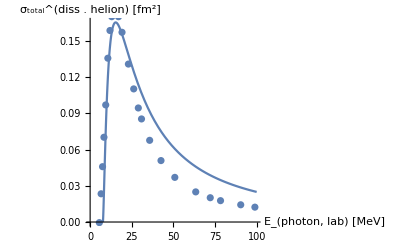

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);


evv=Eigenvalues[evm=(Transpose[invtrafma].norm).invtrafma];
Print["Min[Re] = ",Min[Re[evv]]];
Print["Max[Im] = ",Max[Im[evv]]];
evm=Chop[evm,10^(-6)];
Print[ArrayRules[SparseArray[evm]]];

{trafma,invtrafma}]

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

#### The initial state (helion ground state ^3 He ) -- in bare RGM Basis

B(^3He) = -7.13712

Dim_full^helion = 490

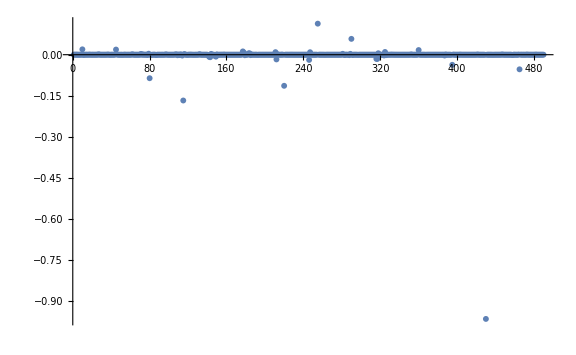
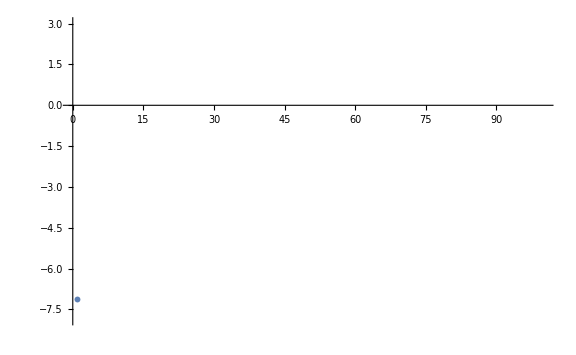
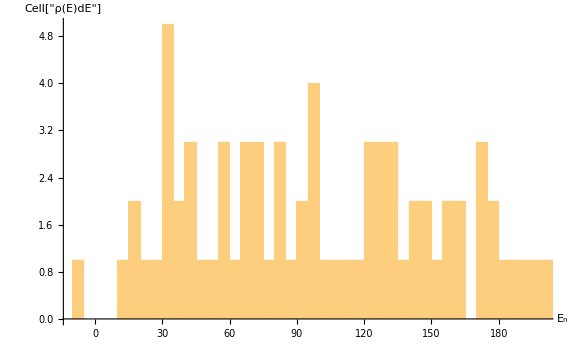
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVbare=Sort[Transpose[Eigensystem[{He3Ham,He3Norm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0bare=orderedEVbare[[1,1]];v0bare=orderedEVbare[[1,2]];

dE=5;
Print["B(^3He) = ",e0bare];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]]]

Grid[{{
ListPlot[Re[v0bare],PlotRange->Full,AxesLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVbare[[All,1]],PlotRange->{{0,100},{1.1 e0bare,3}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVbare[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"45d96bd0-ae25-4b28-924c-9abe19d2b34e"]"}]
}}]
```

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

min/max: {-1.43473×10^-12,187033.}

(min/max) discarded elements: 4 {-1.43473×10^-12,-4.26265×10^-14}

elements < 0: 4

Min[Re] = 0.0000886204

Max[Im] = 2.21276×10^-12

{{1,1}→0.999992,{1,3}→0.138462,{1,5}→-3.66909×10^-6,{1,11}→-1.88956×10^-6,{2,2}→1.01866,{2,3}→1.16575×10^-6,{2,4}→-0.010798,{2,6}→0.116674,{2,7}→-0.0253093,{2,8}→0.042685,{2,9}→0.114018,{2,10}→0.0396045,{2,11}→-0.0000945009,{2,12}→-0.221508,{2,13}→0.01755,{2,14}→0.00921821,{2,15}→-0.0111834,{2,16}→0.0944601,{2,17}→-0.165973,{2,18}→-0.0401515,{2,19}→0.0203846,{2,20}→-0.0028726,{2,21}→-0.00319682,{2,22}→-0.0135332,{2,23}→0.0642508,{2,24}→0.0785617,{2,25}→0.00895973,{2,26}→-0.0124462,{2,27}→-0.0185066,{2,28}→-0.0118553,{2,29}→-0.018984,{2,30}→-0.0013007,{2,31}→0.0843727,{2,32}→0.00972486,{2,33}→0.00756871,{2,34}→-0.0701428,{2,35}→-0.00997232,{2,36}→0.00946947,{2,37}→-0.00219326,{2,38}→0.0339812,{2,39}→0.0128568,{2,40}→0.00631245,{2,41}→0.00731887,{2,42}→0.00623881,{2,43}→0.012688,{2,44}→0.00237151,{2,45}→-0.00849726,{2,46}→0.00975873,{2,47}→-0.0102039,{2,48}→0.000709869,{2,49}→-0.00624062,{2,50}→-0.00600998,{2,51}→-0.000298063,{2,52}→-0.000217511,{2,53}→-0.0106104,{2,54}→0.0264848,{2,55}→-0.0103933,{2,56}→-0.00132425,{2,57}→0.000618444,{2,58}→0.0000127707,{2,59}→-0.00794175,{2,60}→-0.00132165,{2,61}→-0.00112559,{2,62}→-0.00147531,{2,63}→-0.00653731,{2,64}→-0.000814618,{2,66}→0.00503756,{2,68}→0.00378205,{2,69}→0.00625048,{2,71}→-0.00382248,{2,72}→-0.000191403,{2,73}→-0.0062412,{2,74}→0.00141114,{2,75}→-0.00315191,{2,76}→0.00190195,{2,77}→0.0000676866,{2,78}→0.000668369,{2,79}→-0.00620544,{2,80}→0.0000491128,{2,81}→-0.00582681,{2,83}→-0.000587571,{2,84}→0.000332427,{2,85}→0.00162025,{2,87}→-2.99435×10^-6,{2,88}→-0.000444985,{2,89}→0.00145408,{2,94}→0.000239324,{2,96}→0.000961319,{2,97}→0.000260946,{2,101}→-0.000805197,{2,102}→0.000303448,{2,104}→1.05045×10^-6,{2,105}→-0.000460722,{2,106}→-0.0000426736,{2,107}→-0.00115106,{2,109}→-0.000789003,{2,111}→0.0012637,{2,114}→0.000307271,{2,118}→-0.000978485,{2,120}→-0.000347115,{2,122}→-0.000940674,{2,123}→-0.0000738563,{3,1}→0.138462,{3,2}→1.16575×10^-6,{3,3}→0.999998,{3,5}→0.129982,{3,8}→-1.03057×10^-6,{4,2}→-0.010798,{4,4}→2.24669,{4,6}→0.101162,{4,7}→0.22652,{4,8}→0.0578597,{4,9}→0.385385,{4,10}→0.0956573,{4,12}→-0.0769784,{4,13}→-0.0204858,{4,14}→-0.0564392,{4,15}→-0.415029,{4,16}→0.238621,{4,17}→0.0501187,{4,18}→-0.0915328,{4,19}→-0.0952005,{4,20}→0.009822,{4,21}→-0.00952149,{4,22}→-0.201234,{4,23}→0.0345625,{4,24}→-0.0568842,{4,25}→0.0276992,{4,26}→-0.00299499,{4,27}→0.305347,{4,28}→-0.0271532,{4,29}→-0.00740651,{4,30}→0.0996127,{4,31}→0.00767044,{4,32}→-0.0546689,{4,33}→0.0625246,{4,34}→-0.0365335,{4,35}→0.139941,{4,36}→0.0710851,{4,37}→0.0138202,{4,38}→0.027994,{4,39}→-0.0445875,{4,40}→0.446324,{4,41}→0.0143193,{4,42}→-0.000261112,{4,43}→-0.00554629,{4,44}→0.00221526,{4,45}→-0.0144161,{4,46}→-0.00659614,{4,47}→0.335162,{4,48}→0.00307956,{4,49}→0.0128516,{4,50}→0.00843293,{4,51}→-0.0113274,{4,52}→-0.00195034,{4,53}→0.00780863,{4,54}→0.0215522,{4,55}→0.00169202,{4,56}→-0.006209,{4,57}→0.0209713,{4,58}→-0.00707847,{4,59}→-0.00129779,{4,60}→-0.0190218,{4,61}→-0.00417684,{4,62}→0.00585549,{4,63}→0.00650376,{4,64}→-0.000598887,{4,66}→-0.00480452,{4,68}→0.00354754,{4,69}→0.00648899,{4,71}→-0.00390958,{4,72}→0.00946099,{4,73}→-0.00676279,{4,74}→0.00154158,{4,75}→-0.00281332,{4,76}→0.0129217,{4,77}→0.0000730601,{4,78}→-0.00411073,{4,79}→-0.00157613,{4,80}→0.0000639895,{4,81}→-0.00227359,{4,83}→-0.00527694,{4,84}→0.000419961,{4,85}→-0.00157238,{4,87}→-3.16883×10^-6,{4,88}→-0.00125784,{4,89}→0.000937915,{4,94}→0.00202502,{4,95}→-4.48498×10^-6,{4,96}→0.0014651,{4,97}→-0.00074874,{4,98}→-1.68421×10^-6,{4,99}→-1.4528×10^-6,{4,101}→0.00126341,{4,102}→0.000437953,{4,104}→-8.64914×10^-6,{4,105}→-0.000464233,{4,106}→0.000185029,{4,107}→0.00128477,{4,109}→0.00140558,{4,111}→0.000526276,{4,112}→1.81156×10^-6,{4,113}→2.86691×10^-6,{4,114}→-0.00053499,{4,115}→-1.56392×10^-6,{4,117}→-3.82192×10^-6,{4,118}→0.00170071,{4,120}→-0.0000235829,{4,122}→0.000293128,{4,123}→0.0000591147,{4,126}→2.32945×10^-6,{4,133}→2.10114×10^-6,{4,135}→-3.41347×10^-6,{4,139}→1.05327×10^-6,{4,141}→-4.57355×10^-6,{4,148}→-1.82851×10^-6,{4,153}→1.17201×10^-6,{4,158}→-3.36219×10^-6,{4,169}→-1.03053×10^-6,{4,176}→1.20509×10^-6,{4,186}→-1.45881×10^-6,{4,189}→1.2405×10^-6,{4,200}→-1.08457×10^-6,{4,203}→-1.52358×10^-6,{5,1}→-3.66894×10^-6,{5,3}→0.129982,{5,5}→1.,{5,6}→1.4132×10^-6,{5,11}→0.0841854,{6,2}→0.116674,{6,4}→0.101162,{6,5}→1.4132×10^-6,{6,6}→0.899037,{6,7}→-0.0185314,{6,8}→0.616637,{6,9}→0.129669,{6,10}→-0.0784921,{6,11}→-2.34888×10^-6,{6,12}→-0.15167,{6,13}→-0.0393377,{6,14}→-0.031045,{6,15}→0.0566589,{6,16}→0.0544402,{6,17}→-0.0774261,{6,18}→0.0549726,{6,19}→-0.0559169,{6,20}→0.0196677,{6,21}→-0.0192435,{6,22}→-0.0919918,{6,23}→0.00649913,{6,24}→0.0943259,{6,25}→0.0439038,{6,26}→-0.00701792,{6,27}→0.0058582,{6,28}→-0.00465145,{6,29}→-0.0140155,{6,30}→0.0455724,{6,31}→-0.0210556,{6,32}→0.0318096,{6,33}→-0.015142,{6,34}→-0.0433794,{6,35}→-0.0286232,{6,36}→0.0072804,{6,37}→0.0082737,{6,38}→0.0169621,{6,39}→-0.0254372,{6,40}→0.00819347,{6,41}→-0.013934,{6,42}→-0.0155196,{6,43}→0.00786758,{6,44}→-0.00340788,{6,45}→0.00257839,{6,46}→-0.0109568,{6,47}→0.00413962,{6,48}→0.00149645,{6,49}→-0.00471804,{6,50}→-0.00231435,{6,51}→-0.00159444,{6,52}→0.000734828,{6,53}→0.00208976,{6,54}→-0.00449449,{6,55}→0.0010664,{6,56}→-0.00159074,{6,57}→0.00113822,{6,58}→-0.0000129427,{6,59}→0.00252287,{6,60}→-0.00911942,{6,61}→-0.00649739,{6,62}→-0.00290584,{6,63}→-0.00271834,{6,64}→0.00084462,{6,66}→0.000333807,{6,68}→-0.00565169,{6,69}→-0.00043659,{6,71}→0.000199742,{6,72}→0.00514336,{6,73}→-0.0000926723,{6,74}→0.0000401968,{6,75}→0.00143052,{6,76}→0.00245871,{6,77}→3.17973×10^-6,{6,78}→0.00256498,{6,79}→0.00157846,{6,80}→5.4342×10^-6,{6,81}→-0.00125022,{6,83}→0.000729714,{6,84}→0.0000300799,{6,85}→-0.00197504,{6,87}→1.67211×10^-6,{6,88}→-0.000897212,{6,89}→0.00135829,{6,94}→-0.00214276,{6,96}→0.000938383,{6,97}→0.000774193,{6,98}→1.44435×10^-6,{6,99}→2.82147×10^-6,{6,101}→0.000144052,{6,102}→-0.000219284,{6,105}→0.000771413,{6,106}→0.000065528,{6,107}→0.0014812,{6,109}→0.000680721,{6,111}→-0.000950775,{6,114}→-0.000123385,{6,118}→0.000356591,{6,120}→0.000135225,{6,122}→0.00035543,{6,123}→0.0000260888,{7,2}→-0.0253093,{7,4}→0.22652,{7,6}→-0.0185314,{7,7}→1.19875,{7,8}→0.0455962,{7,9}→0.406586,{7,10}→-0.0878136,{7,12}→0.782661,{7,13}→0.00673897,{7,14}→-0.0254353,{7,15}→0.0104378,{7,16}→0.0593093,{7,17}→-0.0148174,{7,18}→0.0460732,{7,19}→-0.0750777,{7,20}→-0.00115303,{7,21}→-0.00500652,{7,22}→-0.031183,{7,23}→-0.0170654,{7,24}→0.00447949,{7,25}→0.0136764,{7,26}→-0.000995495,{7,27}→0.0471933,{7,28}→-0.00974749,{7,29}→-0.0174954,{7,30}→0.028084,{7,31}→-0.00579523,{7,32}→0.0163532,{7,33}→0.0138119,{7,34}→-0.0312586,{7,35}→-0.0163907,{7,36}→0.0178145,{7,37}→0.0100214,{7,38}→-0.00252389,{7,39}→-0.044565,{7,40}→0.00808721,{7,41}→-0.00701725,{7,42}→-0.0130911,{7,43}→0.000246645,{7,44}→-0.00711084,{7,45}→0.00262255,{7,46}→-0.0171478,{7,47}→-0.0103771,{7,48}→0.000664223,{7,49}→-0.00193973,{7,50}→-0.00759455,{7,51}→-7.62264×10^-6,{7,52}→0.000390394,{7,53}→0.00369418,{7,54}→-0.0120248,{7,55}→-0.00324409,{7,56}→0.00162944,{7,57}→0.00364766,{7,58}→-0.0000107785,{7,59}→0.00411292,{7,60}→-0.000257792,{7,61}→0.00242852,{7,62}→0.00555295,{7,63}→0.00292628,{7,64}→0.0001313,{7,66}→-0.00560074,{7,68}→0.000460904,{7,69}→-0.0027249,{7,71}→0.00169351,{7,72}→0.0021933,{7,73}→0.00299967,{7,74}→-0.000682759,{7,75}→-0.00491779,{7,76}→-0.00128861,{7,77}→-0.0000375663,{7,78}→0.00217785,{7,79}→0.00452725,{7,80}→-0.0000303705,{7,81}→0.00196977,{7,83}→-0.00098265,{7,84}→-0.000223033,{7,85}→-0.00177598,{7,87}→2.64911×10^-6,{7,88}→-0.00117262,{7,89}→0.000261293,{7,94}→0.000723238,{7,96}→-0.000573414,{7,97}→0.0000501607,{7,101}→0.00203067,{7,102}→0.000481067,{7,105}→0.00132775,{7,106}→-0.000092159,{7,107}→0.000112883,{7,109}→-0.000672225,{7,111}→-0.000783369,{7,114}→0.000330616,{7,118}→-0.000921755,{7,120}→-0.000202528,{7,122}→-0.000601517,{7,123}→-0.000050658,{8,2}→0.042685,{8,3}→-1.03049×10^-6,{8,4}→0.0578597,{8,6}→0.616637,{8,7}→0.0455962,{8,8}→0.972189,{8,9}→0.00946259,{8,10}→-0.0182187,{8,12}→-0.0509248,{8,13}→-0.087069,{8,14}→0.0384974,{8,15}→-0.0398711,{8,16}→-0.0351932,{8,17}→-0.0233202,{8,18}→-0.0100926,{8,19}→-0.0554163,{8,20}→0.0312055,{8,21}→0.523669,{8,22}→0.0368579,{8,23}→0.0129524,{8,24}→-0.0119853,{8,25}→0.00792419,{8,26}→-0.0000204047,{8,27}→0.0243308,{8,28}→0.00584267,{8,29}→-0.00474153,{8,30}→-0.00232985,{8,31}→0.000993627,{8,32}→0.000459205,{8,33}→0.0177842,{8,34}→0.0231631,{8,35}→0.0195904,{8,36}→-0.0162921,{8,37}→0.0049449,{8,38}→-0.0252862,{8,39}→-0.0275355,{8,40}→-0.009124,{8,41}→0.010134,{8,42}→-0.00711218,{8,43}→-0.00925987,{8,44}→-0.00466902,{8,45}→0.00112613,{8,46}→-0.0106135,{8,47}→-0.00458814,{8,48}→-0.000611377,{8,49}→-0.00399951,{8,50}→-0.00226615,{8,51}→-0.00229099,{8,52}→-0.000491241,{8,53}→0.00181141,{8,54}→-0.0043657,{8,55}→-0.00446571,{8,56}→0.00164631,{8,57}→0.00301814,{8,58}→2.95371×10^-6,{8,59}→-0.0000250345,{8,60}→0.00334747,{8,61}→0.00251516,{8,62}→-0.000879002,{8,63}→-0.00291135,{8,64}→0.00024336,{8,66}→0.00403707,{8,68}→-0.00122323,{8,69}→-0.00354434,{8,71}→0.00217756,{8,72}→-0.00203721,{8,73}→0.00361479,{8,74}→-0.000811687,{8,75}→-0.00258189,{8,76}→-0.00021623,{8,77}→-0.0000381413,{8,78}→0.000999992,{8,79}→0.00156904,{8,80}→-0.0000270628,{8,81}→0.000261089,{8,83}→-0.0000564703,{8,84}→-0.00016604,{8,85}→0.00166404,{8,88}→-0.00121967,{8,89}→0.000064827,{8,94}→0.00110429,{8,96}→-0.0000562281,{8,97}→0.000188398,{8,99}→-1.46207×10^-6,{8,101}→-0.0000904158,{8,102}→-0.000417959,{8,105}→0.000189282,{8,106}→0.0000422623,{8,107}→-0.000179845,{8,109}→0.000518798,{8,111}→0.00009211,{8,114}→-0.000349956,{8,118}→0.00118507,{8,120}→0.0000952643,{8,122}→0.000454786,{8,123}→0.0000568861,{9,2}→0.114018,{9,4}→0.385385,{9,6}→0.129669,{9,7}→0.406586,{9,8}→0.00946259,{9,9}→0.741874,{9,10}→0.139409,{9,12}→0.100666,{9,13}→0.0186883,{9,14}→-0.00688697,{9,15}→0.0619564,{9,16}→-0.087842,{9,17}→0.0262386,{9,18}→0.0458571,{9,19}→-0.0736936,{9,20}→-0.00723426,{9,21}→-0.0001961,{9,22}→-0.00538528,{9,23}→-0.0501863,{9,24}→-0.0556556,{9,25}→0.0182157,{9,26}→0.00471998,{9,27}→0.021281,{9,28}→-0.413253,{9,29}→0.033189,{9,30}→0.0195859,{9,31}→-0.000829042,{9,32}→-0.034244,{9,33}→-0.0274769,{9,34}→0.0158085,{9,35}→-0.00602853,{9,36}→-0.00258299,{9,37}→0.00824705,{9,38}→-0.0512418,{9,39}→-0.0191052,{9,40}→0.0167949,{9,41}→-0.0192873,{9,42}→-0.00521399,{9,43}→-0.0139327,{9,44}→-0.0153288,{9,45}→0.00259781,{9,46}→-0.0192657,{9,47}→0.000516551,{9,48}→-0.00071468,{9,49}→-0.00192361,{9,50}→0.000647928,{9,51}→-0.00726702,{9,52}→0.000749837,{9,53}→-0.00337643,{9,54}→-0.00612158,{9,55}→-0.00481952,{9,56}→0.001823,{9,57}→-0.000580815,{9,58}→-7.09119×10^-6,{9,59}→-0.00375,{9,60}→-0.00274488,{9,61}→0.00344393,{9,62}→0.0044404,{9,63}→0.000965382,{9,64}→0.000221964,{9,66}→-0.0000397302,{9,68}→0.00122173,{9,69}→-0.00443423,{9,71}→0.0027516,{9,72}→0.00159751,{9,73}→0.00476065,{9,74}→-0.00108245,{9,75}→-0.0021075,{9,76}→-0.00133856,{9,77}→-0.0000566549,{9,78}→-8.60373×10^-6,{9,79}→0.00160429,{9,80}→-0.0000416998,{9,81}→0.000414601,{9,83}→0.000436273,{9,84}→-0.000281471,{9,85}→-0.000118996,{9,87}→3.49754×10^-6,{9,88}→-0.00170897,{9,89}→-0.000225431,{9,94}→0.00192694,{9,96}→-0.000248971,{9,97}→0.000258391,{9,101}→0.000225706,{9,102}→-0.000468117,{9,104}→-1.22571×10^-6,{9,105}→-0.000866251,{9,106}→-0.0000404736,{9,107}→-0.00006912,{9,109}→-0.0000738364,{9,111}→-0.000476081,{9,114}→-0.0000670536,{9,118}→0.000486616,{9,120}→-0.00027189,{9,122}→-0.000443206,{10,2}→0.0396045,{10,4}→0.0956573,{10,6}→-0.0784921,{10,7}→-0.0878136,{10,8}→-0.0182187,{10,9}→0.139409,{10,10}→0.914319,{10,12}→-0.175024,{10,13}→-0.00637782,{10,14}→-0.111868,{10,15}→-0.0138504,{10,16}→0.328018,{10,17}→-0.0763901,{10,18}→0.0112554,{10,19}→0.288795,{10,20}→0.0039883,{10,21}→0.00129724,{10,22}→-0.0115538,{10,23}→0.000192254,{10,24}→0.0131826,{10,25}→-0.0106908,{10,26}→-0.00936478,{10,27}→-0.0166417,{10,28}→0.00446278,{10,29}→-0.0572305,{10,30}→0.0259255,{10,31}→0.0256314,{10,32}→0.0168508,{10,33}→0.0487756,{10,34}→0.0124097,{10,35}→0.0463469,{10,36}→-0.0151434,{10,37}→0.00915672,{10,38}→0.0149545,{10,39}→0.0170035,{10,40}→-0.0182801,{10,41}→0.00949597,{10,42}→-0.00252896,{10,43}→0.0422004,{10,44}→0.00815084,{10,45}→0.0033679,{10,46}→0.0114399,{10,47}→-0.0113389,{10,48}→0.000959969,{10,49}→0.00201302,{10,50}→0.000235946,{10,51}→0.0105225,{10,52}→-0.000723525,{10,53}→-0.00225498,{10,54}→0.00451899,{10,55}→-0.00925673,{10,56}→-0.00248443,{10,57}→0.00421418,{10,58}→3.583×10^-6,{10,59}→0.00299319,{10,60}→0.00315185,{10,61}→-0.00832602,{10,62}→-0.000864608,{10,63}→-0.00122409,{10,64}→-0.000202159,{10,66}→-0.00265361,{10,68}→0.000449207,{10,69}→0.00872704,{10,71}→-0.0054246,{10,72}→-0.0014453,{10,73}→-0.00958366,{10,74}→0.00219681,{10,75}→-0.00119386,{10,76}→-0.00142792,{10,77}→0.000111334,{10,78}→-0.0004365,{10,79}→0.000524993,{10,80}→0.0000864559,{10,81}→0.00105356,{10,83}→-0.00178077,{10,84}→0.000582685,{10,85}→-0.0000173228,{10,87}→-5.04802×10^-6,{10,88}→-0.000227517,{10,89}→0.000881997,{10,94}→-0.000127317,{10,96}→-0.000396283,{10,97}→-0.000652411,{10,98}→1.15022×10^-6,{10,99}→1.57397×10^-6,{10,101}→0.00129585,{10,102}→0.000906333,{10,105}→0.0016203,{10,106}→0.000116447,{10,107}→-0.000144953,{10,109}→0.000576819,{10,111}→-0.0000238179,{10,114}→0.0000710578,{10,118}→-0.000514771,{10,120}→0.000169523,{10,122}→0.000215268,{10,123}→-0.0000125933,{11,1}→-1.88935×10^-6,{11,2}→-0.0000945009,{11,5}→0.0841854,{11,6}→-2.34889×10^-6,{11,11}→1.,{11,12}→-1.90833×10^-6,{11,17}→-1.38647×10^-6,{12,2}→-0.221508,{12,4}→-0.0769784,{12,6}→-0.15167,{12,7}→0.782661,{12,8}→-0.0509248,{12,9}→0.100666,{12,10}→-0.175024,{12,11}→-1.90829×10^-6,{12,12}→0.839189,{12,13}→-0.0451625,{12,14}→-0.0417675,{12,15}→-0.0198867,{12,16}→-0.071326,{12,17}→-0.0126828,{12,18}→0.0147047,{12,19}→-0.0236293,{12,20}→0.0163472,{12,21}→0.00315279,{12,22}→0.0293932,{12,23}→-0.00356952,{12,24}→0.0741689,{12,25}→0.0281751,{12,26}→-0.401709,{12,27}→-0.0016255,{12,28}→0.0145576,{12,29}→-0.0302055,{12,30}→0.000868896,{12,31}→0.00831634,{12,32}→0.0225813,{12,33}→0.0220607,{12,34}→-0.0250548,{12,35}→-0.0120754,{12,36}→-0.0166549,{12,37}→0.00501527,{12,38}→0.014163,{12,39}→-0.00408563,{12,40}→-0.0337151,{12,41}→0.00141577,{12,42}→0.00116835,{12,43}→0.0114099,{12,44}→0.000513721,{12,45}→0.00306438,{12,46}→0.000948127,{12,47}→-0.0185381,{12,48}→0.000379757,{12,49}→0.00166285,{12,50}→-0.00139705,{12,51}→0.00356369,{12,52}→0.0000903905,{12,53}→-9.96969×10^-6,{12,54}→-0.00778557,{12,55}→-0.00428461,{12,56}→-0.000073287,{12,57}→0.00625778,{12,58}→-0.0000105537,{12,59}→0.00057161,{12,60}→0.00702375,{12,61}→-0.00163371,{12,62}→0.000310597,{12,63}→-0.00182719,{12,64}→-8.38874×10^-6,{12,66}→-0.0012109,{12,68}→-0.000720175,{12,69}→0.00164413,{12,71}→-0.00103071,{12,72}→-0.0000924554,{12,73}→-0.00185459,{12,74}→0.000426636,{12,75}→-0.000123482,{12,76}→-0.000383287,{12,77}→0.0000232268,{12,78}→0.00267753,{12,79}→0.00195575,{12,80}→0.0000175365,{12,81}→0.00039243,{12,83}→-0.00200519,{12,84}→0.00011777,{12,85}→0.000267367,{12,87}→-2.0405×10^-6,{12,88}→0.0000376726,{12,89}→-0.000378278,{12,94}→-0.000711639,{12,96}→-0.000688236,{12,97}→-0.00021376,{12,101}→0.00117869,{12,102}→0.0000523771,{12,105}→0.00166079,{12,106}→0.0000337693,{12,107}→0.00063506,{12,109}→0.00018692,{12,111}→-0.000156875,{12,114}→0.0000318307,{12,118}→-0.000274302,{12,120}→0.000233472,{12,122}→0.0004182,{12,123}→8.27812×10^-6,{13,2}→0.01755,{13,4}→-0.0204858,{13,6}→-0.0393377,{13,7}→0.00673897,{13,8}→-0.087069,{13,9}→0.0186883,{13,10}→-0.00637782,{13,12}→-0.0451625,{13,13}→0.978909,{13,14}→0.0210882,{13,15}→-0.0451887,{13,16}→-0.0199719,{13,17}→-0.0301679,{13,18}→0.00779829,{13,19}→-0.00584552,{13,20}→0.903331,{13,21}→0.00932913,{13,22}→0.0383083,{13,23}→0.0103472,{13,24}→-0.0025327,{13,25}→-0.0098589,{13,26}→0.226265,{13,27}→-0.00767722,{13,28}→0.00363601,{13,29}→-0.000994883,{13,30}→-0.00295668,{13,31}→0.00139434,{13,32}→0.0011309,{13,33}→0.0195905,{13,34}→-0.00404722,{13,35}→0.0115735,{13,36}→-0.00989722,{13,37}→-0.000140878,{13,38}→-0.00650252,{13,39}→0.00797914,{13,40}→-0.0184274,{13,41}→0.00486385,{13,42}→0.0149692,{13,43}→-0.00309014,{13,44}→-0.00287968,{13,45}→0.0030749,{13,46}→0.00179811,{13,47}→-0.00624697,{13,48}→-0.000183001,{13,49}→-0.0021737,{13,50}→-0.00371631,{13,51}→0.00117166,{13,52}→-0.000254184,{13,53}→0.00160192,{13,54}→-0.00027637,{13,55}→-0.00323142,{13,56}→0.000786362,{13,57}→0.00154888,{13,59}→0.00114772,{13,60}→0.00498856,{13,61}→0.00222743,{13,62}→-0.00111305,{13,63}→-0.00154872,{13,64}→-0.000205019,{13,66}→0.00390586,{13,68}→0.000939633,{13,69}→-0.000347944,{13,71}→0.000229807,{13,72}→-0.0022392,{13,73}→0.000494293,{13,74}→-0.000115555,{13,75}→-0.000956139,{13,76}→-0.000445936,{13,77}→-5.87468×10^-6,{13,78}→0.000616238,{13,79}→0.000114627,{13,80}→-5.40609×10^-6,{13,81}→-0.00104025,{13,83}→0.00032277,{13,84}→-0.0000207697,{13,85}→0.00172444,{13,88}→0.000214314,{13,89}→0.000085381,{13,94}→0.000630732,{13,96}→0.000306363,{13,97}→-0.000106382,{13,101}→-0.0000238512,{13,102}→-0.000190148,{13,105}→0.000287802,{13,106}→-0.0000122398,{13,107}→0.0000359294,{13,109}→-0.000203043,{13,111}→0.000700817,{13,114}→-0.0000305753,{13,118}→0.000051525,{13,120}→0.0000628559,{13,122}→0.000139181,{13,123}→7.20927×10^-6,{14,2}→0.00921821,{14,4}→-0.0564392,{14,6}→-0.031045,{14,7}→-0.0254353,{14,8}→0.0384974,{14,9}→-0.00688697,{14,10}→-0.111868,{14,12}→-0.0417675,{14,13}→0.0210882,{14,14}→1.04911,{14,15}→-0.0144162,{14,16}→-0.0269983,{14,17}→0.00197203,{14,18}→0.0549375,{14,19}→0.065022,{14,20}→-0.00585147,{14,21}→-0.00330377,{14,22}→-0.0181911,{14,23}→-0.431912,{14,24}→0.0288664,{14,25}→-0.0128856,{14,26}→-0.00293755,{14,27}→-0.000445393,{14,28}→0.00448978,{14,29}→-0.013196,{14,30}→-0.0121588,{14,31}→-0.00275533,{14,32}→0.00444416,{14,33}→-0.00850993,{14,34}→-0.002201,{14,35}→-0.0256684,{14,36}→0.0132518,{14,37}→0.489892,{14,38}→-0.00283851,{14,39}→-0.00553816,{14,40}→0.0154516,{14,41}→-0.00221402,{14,42}→0.00404817,{14,43}→0.00486062,{14,44}→-0.00127334,{14,45}→0.00512805,{14,46}→-0.00363556,{14,47}→-0.00834876,{14,48}→-0.000356103,{14,49}→-0.0000853093,{14,50}→0.00038966,{14,51}→-0.000798946,{14,52}→0.000261444,{14,53}→0.00350422,{14,54}→-0.00525959,{14,55}→0.000698897,{14,56}→-0.00109995,{14,57}→0.000990076,{14,58}→-3.44495×10^-6,{14,59}→0.00381163,{14,60}→-0.000251968,{14,61}→0.0019215,{14,62}→0.000198052,{14,63}→0.0000479231,{14,64}→-0.000698869,{14,66}→-0.00135705,{14,68}→0.00195729,{14,69}→0.00306704,{14,71}→-0.00185658,{14,72}→0.00242765,{14,73}→-0.00296698,{14,74}→0.000669474,{14,75}→-0.000297545,{14,76}→-0.00014032,{14,77}→0.0000338698,{14,78}→0.00194902,{14,79}→-0.000456906,{14,80}→0.0000251909,{14,81}→-0.000846468,{14,83}→0.000202575,{14,84}→0.000176833,{14,85}→0.000798611,{14,87}→-1.95197×10^-6,{14,88}→0.000962077,{14,89}→-0.00064467,{14,94}→-0.000716386,{14,96}→-0.0000896207,{14,97}→0.0000150142,{14,101}→0.000405728,{14,102}→0.0000784181,{14,105}→-0.000161886,{14,106}→0.0000440864,{14,107}→0.000994386,{14,109}→0.000315844,{14,111}→0.0000721883,{14,114}→-0.0000520796,{14,118}→-0.0000302614,{14,120}→0.000273935,{14,122}→0.000551059,{14,123}→0.0000207466,{15,2}→-0.0111834,{15,4}→-0.415029,{15,6}→0.0566589,{15,7}→0.0104378,{15,8}→-0.0398711,{15,9}→0.0619564,{15,10}→-0.0138504,{15,12}→-0.0198867,{15,13}→-0.0451887,{15,14}→-0.0144162,{15,15}→1.00229,{15,16}→-0.0159466,{15,17}→0.0260446,{15,18}→-0.0119892,{15,19}→-0.036133,{15,20}→0.0153273,{15,21}→0.00118854,{15,22}→0.0684491,{15,23}→0.0310739,{15,24}→0.0163589,{15,25}→0.00288593,{15,26}→0.000324357,{15,27}→-0.277055,{15,28}→0.00420742,{15,29}→-0.0210127,{15,30}→-0.0320759,{15,31}→-0.00379005,{15,32}→0.0128271,{15,33}→0.0194819,{15,34}→-0.0120997,{15,35}→0.00557134,{15,36}→-0.0244922,{15,37}→0.00519178,{15,38}→0.01605,{15,39}→-0.00114647,{15,40}→-0.280934,{15,41}→0.00437839,{15,42}→0.00872721,{15,43}→-0.00041598,{15,44}→0.00353736,{15,45}→0.00347357,{15,46}→0.00819224,{15,47}→-0.20223,{15,48}→-0.00035754,{15,49}→-0.000382557,{15,50}→-0.00766744,{15,51}→0.0015174,{15,52}→-0.000132249,{15,53}→0.00155027,{15,54}→-0.00276916,{15,55}→-0.0017652,{15,56}→-0.000429389,{15,57}→-0.00434178,{15,58}→0.00411896,{15,59}→0.00448518,{15,60}→0.00736295,{15,61}→-0.000825742,{15,62}→-0.00211338,{15,63}→-0.000402003,{15,64}→-0.0000321785,{15,66}→0.00314686,{15,68}→-0.000323072,{15,69}→0.000807965,{15,71}→-0.000492121,{15,72}→-0.00148972,{15,73}→-0.000823063,{15,74}→0.000183381,{15,75}→0.00121874,{15,76}→-0.00136186,{15,77}→6.99703×10^-6,{15,78}→0.000104114,{15,79}→0.00054039,{15,80}→6.0275×10^-6,{15,81}→0.000219727,{15,83}→0.000210292,{15,84}→0.0000452229,{15,85}→0.000720574,{15,88}→0.00012287,{15,89}→0.000146726,{15,94}→0.000180974,{15,96}→-0.000152722,{15,97}→0.00033276,{15,101}→-0.00042223,{15,102}→0.000082038,{15,105}→0.000620937,{15,106}→-0.0000147956,{15,107}→-0.00065983,{15,109}→-0.000261807,{15,111}→0.000452459,{15,114}→0.0000869399,{15,118}→-0.000400051,{15,120}→0.000128414,{15,122}→0.000176253,{15,123}→-5.45492×10^-6,{16,2}→0.0944601,{16,4}→0.238621,{16,6}→0.0544402,{16,7}→0.0593093,{16,8}→-0.0351932,{16,9}→-0.087842,{16,10}→0.328018,{16,12}→-0.071326,{16,13}→-0.0199719,{16,14}→-0.0269983,{16,15}→-0.0159466,{16,16}→0.981156,{16,17}→-0.0288426,{16,18}→-0.0181773,{16,19}→0.0255736,{16,20}→0.00709656,{16,21}→0.00220983,{16,22}→-0.0311033,{16,23}→-0.00632282,{16,24}→-0.0126549,{16,25}→-0.0098024,{16,26}→-0.00309487,{16,27}→0.0110195,{16,28}→0.840695,{16,29}→0.00190614,{16,30}→0.0129917,{16,31}→0.0119157,{16,32}→0.00386838,{16,33}→-0.00246162,{16,34}→0.00551358,{16,35}→-0.00634624,{16,36}→0.007282,{16,37}→-0.0018144,{16,38}→-0.0208685,{16,39}→-0.00241219,{16,40}→0.0131965,{16,41}→-0.00635464,{16,42}→-0.0116521,{16,43}→0.00406435,{16,44}→-0.005883,{16,45}→-0.00107527,{16,46}→-0.0020746,{16,47}→0.00269638,{16,48}→-0.000176068,{16,49}→-0.00448226,{16,50}→0.00175127,{16,51}→0.00204993,{16,52}→0.000269518,{16,53}→-0.000419213,{16,54}→0.00535407,{16,55}→0.00178147,{16,56}→0.000872762,{16,57}→0.00123416,{16,59}→0.00136755,{16,60}→-0.00249625,{16,61}→0.00149125,{16,62}→-0.00173134,{16,63}→-0.000113486,{16,64}→-0.000100956,{16,66}→-0.00088817,{16,68}→0.0000606251,{16,69}→-0.00034712,{16,71}→0.000227147,{16,72}→0.000390688,{16,73}→0.000477945,{16,74}→-0.000113118,{16,75}→-0.000766536,{16,76}→0.000501628,{16,77}→-7.97638×10^-6,{16,78}→0.000331309,{16,79}→-0.000317508,{16,80}→-7.0752×10^-6,{16,81}→0.000594056,{16,83}→0.00041421,{16,84}→-0.000054432,{16,85}→-0.000682506,{16,87}→1.16325×10^-6,{16,88}→-0.000409995,{16,89}→0.000160352,{16,94}→-0.00015827,{16,96}→-0.000331554,{16,97}→-0.000277547,{16,101}→0.000450257,{16,102}→0.000228698,{16,105}→0.000504196,{16,106}→-0.000039374,{16,107}→-0.0000903738,{16,109}→-0.000247272,{16,111}→-0.000906222,{16,114}→0.00022781,{16,118}→-0.000626179,{16,120}→-0.000178893,{16,122}→-0.000495998,{16,123}→-0.000038697,{17,2}→-0.165973,{17,4}→0.0501187,{17,6}→-0.0774261,{17,7}→-0.0148174,{17,8}→-0.0233202,{17,9}→0.0262386,{17,10}→-0.0763901,{17,11}→-1.38647×10^-6,{17,12}→-0.0126828,{17,13}→-0.0301679,{17,14}→0.00197203,{17,15}→0.0260446,{17,16}→-0.0288426,{17,17}→0.965683,{17,18}→0.0374524,{17,19}→0.0682653,{17,20}→0.0100448,{17,21}→0.0011293,{17,22}→-0.0397154,{17,23}→-0.745228,{17,24}→-0.379791,{17,25}→0.0196346,{17,26}→0.000201414,{17,27}→0.00415562,{17,28}→0.00550195,{17,29}→0.0233942,{17,30}→0.0087834,{17,31}→0.00518117,{17,32}→-0.000672602,{17,33}→-0.00572428,{17,34}→-0.00315638,{17,35}→-0.0163229,{17,36}→0.014902,{17,37}→-0.0082824,{17,38}→-0.00509188,{17,39}→0.00049093,{17,40}→0.00638373,{17,41}→-0.0119941,{17,42}→-0.00580611,{17,43}→-0.00770603,{17,44}→-0.00235697,{17,45}→-0.00207439,{17,46}→-0.00487887,{17,47}→-0.00483007,{17,48}→0.0000850102,{17,49}→-0.00194045,{17,50}→0.0017507,{17,51}→-0.000141,{17,52}→0.000549049,{17,53}→0.000295257,{17,54}→0.00166185,{17,55}→0.00195905,{17,56}→0.00190677,{17,57}→0.0015147,{17,58}→-4.61058×10^-6,{17,59}→0.000567415,{17,60}→-0.00251199,{17,61}→0.00368846,{17,62}→0.000879521,{17,63}→-0.000141145,{17,64}→0.0000386768,{17,66}→-0.00242168,{17,68}→-0.0000946001,{17,69}→-0.00309752,{17,71}→0.0019254,{17,72}→0.000242221,{17,73}→0.00337918,{17,74}→-0.000772572,{17,75}→0.0000753001,{17,76}→0.00162867,{17,77}→-0.0000412545,{17,78}→0.000219429,{17,79}→-0.000055889,{17,80}→-0.0000313119,{17,81}→0.0000931159,{17,83}→-0.0000990496,{17,84}→-0.000194548,{17,85}→0.00123818,{17,87}→3.76061×10^-6,{17,88}→0.000826014,{17,89}→-0.000640646,{17,94}→-0.000471811,{17,96}→0.000406024,{17,97}→0.000249722,{17,99}→1.7765×10^-6,{17,101}→-0.000382875,{17,102}→-0.000508052,{17,105}→-0.00028411,{17,106}→-0.0000367511,{17,107}→0.000822203,{17,109}→-0.0000890188,{17,111}→-0.000784117,{17,114}→0.0000517661,{17,118}→-0.0000520545,{17,120}→-0.0000653388,{17,122}→-0.000134034,{17,123}→-4.41666×10^-6,{18,2}→-0.0401515,{18,4}→-0.0915328,{18,6}→0.0549726,{18,7}→0.0460732,{18,8}→-0.0100926,{18,9}→0.0458571,{18,10}→0.0112554,{18,12}→0.0147047,{18,13}→0.00779829,{18,14}→0.0549375,{18,15}→-0.0119892,{18,16}→-0.0181773,{18,17}→0.0374524,{18,18}→1.0314,{18,19}→0.0310436,{18,20}→-0.00322714,{18,21}→0.00160365,{18,22}→-0.0192348,{18,23}→-0.00756182,{18,24}→-0.567395,{18,25}→0.550537,{18,26}→0.000662377,{18,27}→-0.0215725,{18,28}→0.00400824,{18,29}→0.0042876,{18,30}→-0.0113791,{18,31}→0.0110479,{18,32}→-0.00342373,{18,33}→-0.00762427,{18,34}→0.00914011,{18,35}→0.0000894201,{18,36}→0.012092,{18,37}→-0.00626357,{18,38}→-0.0127985,{18,39}→0.00599251,{18,40}→-0.00176855,{18,41}→0.0000541833,{18,42}→0.00564304,{18,43}→-0.00135241,{18,44}→-0.00224751,{18,45}→0.000337562,{18,46}→0.000963922,{18,47}→-0.00390396,{18,48}→-0.00058081,{18,49}→-0.00346392,{18,50}→0.00195826,{18,51}→-0.000745925,{18,52}→-0.0000281394,{18,53}→-0.000539273,{18,54}→-0.00121276,{18,55}→0.00160743,{18,56}→-0.000170849,{18,57}→-0.000577576,{18,58}→1.07982×10^-6,{18,59}→-0.00068976,{18,60}→0.000325028,{18,61}→0.00132916,{18,62}→0.00134126,{18,63}→0.000408711,{18,64}→-0.000289297,{18,66}→0.0011765,{18,68}→0.000766095,{18,69}→0.000820847,{18,71}→-0.000487486,{18,72}→-0.000147915,{18,73}→-0.000731488,{18,74}→0.000162304,{18,75}→0.000475902,{18,76}→0.000674721,{18,77}→8.2895×10^-6,{18,78}→0.000423007,{18,79}→-0.000810148,{18,80}→5.93878×10^-6,{18,81}→-0.00023809,{18,83}→-0.0000959913,{18,84}→0.0000468672,{18,85}→0.000818339,{18,88}→0.000789765,{18,89}→-0.000639063,{18,94}→-0.0000486531,{18,96}→0.000370574,{18,97}→-6.14557×10^-6,{18,101}→-0.00010133,{18,102}→-0.000363483,{18,105}→-0.000583995,{18,106}→9.74809×10^-6,{18,107}→0.000471383,{18,109}→0.0000659404,{18,111}→0.000180236,{18,114}→-0.0000411931,{18,118}→0.000100856,{18,120}→0.0000397266,{18,122}→0.000101165,{18,123}→6.83679×10^-6,{19,2}→0.0203846,{19,4}→-0.0952005,{19,6}→-0.0559169,{19,7}→-0.0750777,{19,8}→-0.0554163,{19,9}→-0.0736936,{19,10}→0.288795,{19,12}→-0.0236293,{19,13}→-0.00584552,{19,14}→0.065022,{19,15}→-0.036133,{19,16}→0.0255736,{19,17}→0.0682653,{19,18}→0.0310436,{19,19}→0.988809,{19,20}→0.000747802,{19,21}→0.0066379,{19,22}→0.0110123,{19,23}→0.0117172,{19,24}→0.0267447,{19,25}→0.00381878,{19,26}→-0.00124618,{19,27}→-0.00986299,{19,28}→-0.00581867,{19,29}→0.0109418,{19,30}→-0.0235178,{19,31}→-0.00275491,{19,32}→-0.0166412,{19,33}→-0.0112223,{19,34}→0.00986404,{19,35}→-0.0173375,{19,36}→-0.00261225,{19,37}→0.821466,{19,38}→0.00366038,{19,39}→-0.0106318,{19,40}→-0.00570477,{19,41}→-0.0110631,{19,42}→0.00602871,{19,43}→-0.013339,{19,44}→0.00316463,{19,45}→0.00199308,{19,46}→-0.00451446,{19,47}→-0.00272189,{19,48}→-0.000496123,{19,49}→0.000982493,{19,50}→0.00188358,{19,51}→-0.00202709,{19,52}→0.000547069,{19,53}→0.00331634,{19,54}→-0.00648973,{19,55}→0.00293495,{19,56}→0.00113432,{19,57}→0.00121179,{19,58}→-6.80817×10^-6,{19,59}→0.00331247,{19,60}→0.000627644,{19,61}→0.00409624,{19,62}→0.00027288,{19,63}→-0.000582635,{19,64}→-0.000104735,{19,66}→0.000829104,{19,68}→0.00121171,{19,69}→-0.0025908,{19,71}→0.00161197,{19,72}→0.00115971,{19,73}→0.00281435,{19,74}→-0.000641867,{19,75}→0.00106161,{19,76}→0.00108611,{19,77}→-0.0000302126,{19,78}→0.00123693,{19,79}→-0.000918544,{19,80}→-0.0000228881,{19,81}→-0.00126143,{19,83}→-0.000120794,{19,84}→-0.000139267,{19,85}→0.000552519,{19,87}→1.2277×10^-6,{19,88}→0.000617713,{19,89}→-0.00130201,{19,94}→-0.000437742,{19,96}→0.000140782,{19,97}→0.000114927,{19,101}→0.000192936,{19,102}→-0.00017635,{19,105}→-0.000318284,{19,106}→0.0000401997,{19,107}→0.000617303,{19,109}→0.000457352,{19,111}→0.00015981,{19,114}→-0.00030165,{19,118}→0.00088699,{19,120}→0.000297858,{19,122}→0.000807417,{19,123}→0.0000624917,{20,2}→-0.0028726,{20,4}→0.009822,{20,6}→0.0196677,{20,7}→-0.00115303,{20,8}→0.0312055,{20,9}→-0.00723426,{20,10}→0.0039883,{20,12}→0.0163472,{20,13}→0.903331,{20,14}→-0.00585147,{20,15}→0.0153273,{20,16}→0.00709656,{20,17}→0.0100448,{20,18}→-0.00322714,{20,19}→0.000747802,{20,20}→0.998843,{20,21}→0.24067,{20,22}→-0.0131588,{20,23}→-0.00319416,{20,24}→-0.000177494,{20,25}→0.00347177,{20,26}→0.000701449,{20,27}→0.00341196,{20,28}→-0.00131461,{20,29}→0.000602992,{20,30}→0.00104212,{20,31}→-0.000624723,{20,32}→-0.000626265,{20,33}→-0.00681721,{20,34}→0.00240394,{20,35}→-0.00343147,{20,36}→0.00325617,{20,37}→0.000133255,{20,38}→0.00144171,{20,39}→-0.00359934,{20,40}→0.0067591,{20,41}→-0.00147233,{20,42}→-0.00558793,{20,43}→0.000697931,{20,44}→0.000889257,{20,45}→-0.00110354,{20,46}→-0.000965318,{20,47}→0.00237089,{20,48}→0.0000450661,{20,49}→0.000625152,{20,50}→0.00128471,{20,51}→-0.000537294,{20,52}→0.0000759434,{20,53}→-0.0005181,{20,54}→0.0000841788,{20,55}→0.00108701,{20,56}→-0.000238429,{20,57}→-0.000549943,{20,59}→-0.000418238,{20,60}→-0.00179854,{20,61}→-0.000721385,{20,62}→0.000347514,{20,63}→0.000476825,{20,64}→0.0000825894,{20,66}→-0.0012457,{20,68}→-0.000379005,{20,69}→1.2999×10^-6,{20,71}→-6.4798×10^-6,{20,72}→0.000749348,{20,73}→-0.0000506697,{20,74}→0.0000129444,{20,75}→0.000279297,{20,76}→0.000167395,{20,78}→-0.000222836,{20,79}→-0.0000247874,{20,81}→0.000366418,{20,83}→-0.000086364,{20,84}→1.44799×10^-6,{20,85}→-0.000571396,{20,88}→-0.000113352,{20,89}→-0.0000201208,{20,94}→-0.000190311,{20,96}→-0.0000980548,{20,97}→0.0000484838,{20,101}→-0.0000134576,{20,102}→0.0000532743,{20,105}→-0.00011948,{20,106}→5.54287×10^-6,{20,107}→-0.0000228297,{20,109}→0.0000886196,{20,111}→-0.000246263,{20,118}→0.000023304,{20,120}→-0.0000218987,{20,122}→-0.0000394745,{21,2}→-0.00319682,{21,4}→-0.00952149,{21,6}→-0.0192435,{21,7}→-0.00500652,{21,8}→0.523669,{21,9}→-0.000196099,{21,10}→0.00129724,{21,12}→0.00315279,{21,13}→0.00932913,{21,14}→-0.00330377,{21,15}→0.00118854,{21,16}→0.00220983,{21,17}→0.0011293,{21,18}→0.00160365,{21,19}→0.0066379,{21,20}→0.24067,{21,21}→1.00133,{21,22}→-0.00104615,{21,23}→-0.00094538,{21,24}→0.00108405,{21,25}→-0.00183334,{21,26}→-0.000119168,{21,27}→-0.00359691,{21,28}→-0.000358842,{21,29}→0.000434507,{21,30}→-0.000191258,{21,31}→0.000152716,{21,32}→-0.0000499746,{21,33}→-0.000548882,{21,34}→-0.00306113,{21,35}→-0.00148628,{21,36}→0.00118183,{21,37}→-0.000643225,{21,38}→0.00262861,{21,39}→0.00412001,{21,40}→-0.000444642,{21,41}→-0.00081739,{21,42}→0.00208195,{21,43}→0.000936296,{21,44}→0.000386442,{21,45}→0.0000887822,{21,46}→0.00151341,{21,47}→-0.0000248237,{21,48}→0.0000555228,{21,49}→0.000377251,{21,50}→0.0000103268,{21,51}→0.00040097,{21,52}→0.0000387485,{21,53}→-0.000118364,{21,54}→0.000497475,{21,55}→0.0002858,{21,56}→-0.000135524,{21,57}→-0.000232398,{21,59}→0.0000779581,{21,60}→0.0000469789,{21,61}→-0.000113199,{21,62}→0.000054638,{21,63}→0.000260514,{21,64}→-0.0000508318,{21,66}→-0.000230962,{21,68}→0.000255338,{21,69}→0.000424771,{21,71}→-0.000259429,{21,72}→0.0000574879,{21,73}→-0.000420152,{21,74}→0.000093925,{21,75}→0.00023678,{21,76}→-0.0000256337,{21,77}→4.38346×10^-6,{21,78}→-0.0000796135,{21,79}→-0.000182042,{21,80}→3.00024×10^-6,{21,81}→-0.000096335,{21,83}→0.0000141681,{21,84}→0.0000193552,{21,85}→-0.0000681676,{21,88}→0.000172626,{21,89}→-0.0000126803,{21,94}→-0.0000801952,{21,96}→0.0000189324,{21,97}→-0.0000375331,{21,101}→0.0000170829,{21,102}→0.0000402735,{21,105}→2.75676×10^-6,{21,106}→-6.51081×10^-6,{21,107}→0.0000189598,{21,109}→-0.0000837119,{21,111}→0.0000444928,{21,114}→0.0000426886,{21,118}→-0.00014866,{21,120}→-7.09602×10^-6,{21,122}→-0.0000471548,{21,123}→-6.73807×10^-6,{22,2}→-0.0135332,{22,4}→-0.201234,{22,6}→-0.0919918,{22,7}→-0.031183,{22,8}→0.0368579,{22,9}→-0.00538528,{22,10}→-0.0115538,{22,12}→0.0293932,{22,13}→0.0383083,{22,14}→-0.0181911,{22,15}→0.0684491,{22,16}→-0.0311033,{22,17}→-0.0397154,{22,18}→-0.0192348,{22,19}→0.0110123,{22,20}→-0.0131588,{22,21}→-0.00104615,{22,22}→1.01752,{22,23}→-0.00150313,{22,24}→0.0221004,{22,25}→0.0117774,{22,26}→0.000352159,{22,27}→-0.309919,{22,28}→0.00472956,{22,29}→-0.00185521,{22,30}→-0.00408365,{22,31}→-0.007183,{22,32}→0.0141782,{22,33}→0.00913778,{22,34}→-0.0157719,{22,35}→-0.0109399,{22,36}→-0.00344642,{22,37}→-0.000424727,{22,38}→0.0138134,{22,39}→0.000876332,{22,40}→-0.277445,{22,41}→0.0079869,{22,42}→-0.00117743,{22,43}→-0.0000189824,{22,44}→0.00165846,{22,45}→-0.0012975,{22,46}→0.000090046,{22,47}→-0.221263,{22,48}→0.000244572,{22,49}→0.00427053,{22,50}→-0.00585479,{22,51}→-0.0000205612,{22,52}→-0.000176999,{22,53}→-0.00171905,{22,54}→-0.000761838,{22,55}→-0.00145781,{22,56}→0.000371472,{22,57}→-0.00125507,{22,58}→0.00452161,{22,59}→-0.000718609,{22,60}→0.00211012,{22,61}→-0.000113434,{22,62}→-0.000188945,{22,63}→-0.000248406,{22,64}→0.0000922917,{22,66}→-0.00229699,{22,68}→-0.000401253,{22,69}→-0.000464865,{22,71}→0.000296735,{22,72}→-0.0015657,{22,73}→0.000493555,{22,74}→-0.000116237,{22,75}→-0.000412197,{22,76}→-0.00117994,{22,77}→-4.67341×10^-6,{22,78}→0.000597017,{22,79}→0.00157688,{22,80}→-5.70573×10^-6,{22,81}→0.000367134,{22,83}→0.0000392416,{22,84}→-0.0000412411,{22,85}→-0.000150183,{22,87}→-1.39294×10^-6,{22,88}→-0.000375359,{22,89}→0.000330057,{22,94}→-0.0000593059,{22,96}→-0.000239638,{22,97}→-0.0000531492,{22,98}→-1.27975×10^-6,{22,99}→-2.80367×10^-6,{22,101}→-0.000289217,{22,102}→-0.0000394091,{22,104}→-1.31086×10^-6,{22,105}→0.000207103,{22,106}→-0.00003181,{22,107}→-0.000286688,{22,109}→-0.000294582,{22,111}→0.0000795728,{22,114}→0.000101266,{22,115}→-1.40147×10^-6,{22,118}→-0.000286589,{22,120}→-0.0000855138,{22,122}→-0.000235585,{22,123}→-0.0000183527,{22,126}→1.00915×10^-6,{22,141}→-1.16929×10^-6,{23,2}→0.0642508,{23,4}→0.0345625,{23,6}→0.00649913,{23,7}→-0.0170654,{23,8}→0.0129524,{23,9}→-0.0501863,{23,10}→0.000192254,{23,12}→-0.00356952,{23,13}→0.0103472,{23,14}→-0.431912,{23,15}→0.0310739,{23,16}→-0.00632282,{23,17}→-0.745228,{23,18}→-0.00756182,{23,19}→0.0117172,{23,20}→-0.00319416,{23,21}→-0.00094538,{23,22}→-0.00150313,{23,23}→0.991471,{23,24}→0.00629314,{23,25}→0.00156458,{23,26}→-0.000547506,{23,27}→0.0282632,{23,28}→-0.000365887,{23,29}→0.00173071,{23,30}→0.000504694,{23,31}→-0.00206741,{23,32}→0.00812206,{23,33}→-0.00560313,{23,34}→-0.0060745,{23,35}→-0.0131727,{23,36}→0.000749438,{23,37}→-0.00047212,{23,38}→0.00364943,{23,39}→0.00337124,{23,40}→0.00957913,{23,41}→-0.00401352,{23,42}→-0.00434469,{23,43}→0.00263018,{23,44}→0.0000977783,{23,45}→-0.000823761,{23,46}→-0.00053796,{23,47}→0.00547775,{23,48}→0.0000929221,{23,49}→-0.00119282,{23,50}→-0.000539717,{23,51}→0.00140723,{23,52}→0.00026776,{23,53}→0.000594988,{23,54}→0.00121618,{23,55}→0.00142346,{23,56}→0.000376931,{23,57}→-0.00131948,{23,58}→-4.09569×10^-6,{23,59}→-0.000791196,{23,60}→-0.00128439,{23,61}→0.0010354,{23,62}→-0.000360628,{23,63}→0.000773789,{23,64}→-0.000129411,{23,66}→-0.000655033,{23,68}→-0.000207352,{23,69}→0.000187865,{23,71}→-0.000110581,{23,72}→-0.000227933,{23,73}→-0.000167393,{23,74}→0.0000385274,{23,75}→-0.000334386,{23,76}→-0.00034361,{23,77}→2.04304×10^-6,{23,78}→-0.000121043,{23,79}→0.000109285,{23,80}→1.79739×10^-6,{23,81}→-9.55266×10^-6,{23,83}→0.000678786,{23,84}→8.53647×10^-6,{23,85}→-0.000404639,{23,88}→0.0000574577,{23,89}→0.000252669,{23,94}→-0.000388904,{23,96}→-0.000266278,{23,97}→-0.000315482,{23,101}→-0.0000518671,{23,102}→0.0000726157,{23,105}→0.000114721,{23,106}→0.0000125499,{23,107}→-0.000140915,{23,109}→0.000165735,{23,111}→-0.000365027,{23,114}→-7.62399×10^-6,{23,118}→1.04619×10^-6,{23,120}→0.0000613511,{23,122}→0.000127582,{23,123}→5.65622×10^-6,{24,2}→0.0785617,{24,4}→-0.0568842,{24,6}→0.0943259,{24,7}→0.00447949,{24,8}→-0.0119853,{24,9}→-0.0556556,{24,10}→0.0131826,{24,12}→0.0741689,{24,13}→-0.0025327,{24,14}→0.0288664,{24,15}→0.0163589,{24,16}→-0.0126549,{24,17}→-0.379791,{24,18}→-0.567395,{24,19}→0.0267447,{24,20}→-0.000177494,{24,21}→0.00108405,{24,22}→0.0221004,{24,23}→0.00629314,{24,24}→0.97319,{24,25}→0.00118459,{24,26}→0.00405673,{24,27}→0.00222063,{24,28}→0.000421565,{24,29}→0.00556138,{24,30}→-0.0115896,{24,31}→0.00718222,{24,32}→-0.0127537,{24,33}→0.00252714,{24,34}→0.0134133,{24,35}→0.00906736,{24,36}→0.00212656,{24,37}→-0.00444463,{24,38}→-0.00506256,{24,39}→0.00116405,{24,40}→-0.001414,{24,41}→0.00157372,{24,42}→0.00588223,{24,43}→-0.00390227,{24,44}→0.00101945,{24,45}→0.001926,{24,46}→-0.00101771,{24,47}→0.00465101,{24,48}→-0.00040261,{24,49}→-0.00136759,{24,50}→-0.000509542,{24,51}→-0.00194165,{24,52}→-0.000129481,{24,53}→-0.00125243,{24,54}→0.00289848,{24,55}→0.000210991,{24,56}→0.0000400039,{24,57}→-0.00183289,{24,58}→3.10191×10^-6,{24,59}→-0.000983427,{24,60}→0.000945609,{24,61}→0.00142061,{24,62}→0.000374737,{24,63}→0.0000924937,{24,64}→-0.00020383,{24,66}→0.00203009,{24,68}→0.00114699,{24,69}→0.000161423,{24,71}→-0.0000848205,{24,72}→-0.00144346,{24,73}→-0.0000812404,{24,74}→0.0000182288,{24,75}→-0.000533667,{24,76}→-0.000584485,{24,78}→-0.000947009,{24,79}→-0.000246363,{24,80}→1.43079×10^-6,{24,81}→-0.000420692,{24,83}→0.000439915,{24,84}→0.0000194824,{24,85}→0.00107535,{24,88}→-0.000268662,{24,89}→-0.000295134,{24,94}→0.000743398,{24,96}→0.000193598,{24,97}→0.000395258,{24,101}→-0.000588285,{24,102}→-0.000041087,{24,105}→-0.000538415,{24,106}→0.0000197528,{24,107}→-0.000584133,{24,109}→0.000146783,{24,111}→0.000471981,{24,114}→-0.0001516,{24,118}→0.000529398,{24,120}→-0.0000537713,{24,123}→0.0000155232,{25,2}→0.00895973,{25,4}→0.0276992,{25,6}→0.0439038,{25,7}→0.0136764,{25,8}→0.00792419,{25,9}→0.0182157,{25,10}→-0.0106908,{25,12}→0.0281751,{25,13}→-0.0098589,{25,14}→-0.0128856,{25,15}→0.00288593,{25,16}→-0.0098024,{25,17}→0.0196346,{25,18}→0.550537,{25,19}→0.00381878,{25,20}→0.00347177,{25,21}→-0.00183334,{25,22}→0.0117774,{25,23}→0.00156458,{25,24}→0.00118459,{25,25}→1.00558,{25,26}→0.0018333,{25,27}→-0.0122855,{25,28}→0.00206296,{25,29}→-0.0104594,{25,30}→0.000430392,{25,31}→0.000982,{25,32}→0.00103632,{25,33}→0.0038862,{25,34}→-0.244193,{25,35}→0.00785608,{25,36}→-0.00324225,{25,37}→0.000155382,{25,38}→-0.000687907,{25,39}→-0.00398408,{25,40}→-0.0105824,{25,41}→0.000479335,{25,42}→0.00597578,{25,43}→0.00289542,{25,44}→-0.000750808,{25,45}→0.00130244,{25,46}→0.000968995,{25,47}→0.00419694,{25,48}→3.16132×10^-6,{25,49}→-0.00267149,{25,50}→-0.000471754,{25,51}→0.000484412,{25,52}→-0.0000752934,{25,53}→-0.000176187,{25,54}→0.000357495,{25,55}→0.000786694,{25,56}→-0.00057765,{25,57}→0.00130582,{25,58}→-1.18753×10^-6,{25,59}→-0.00104488,{25,60}→0.00100816,{25,61}→-0.000776642,{25,62}→-0.000529168,{25,63}→-0.000373265,{25,64}→-0.000106172,{25,66}→0.000575319,{25,68}→-0.000583802,{25,69}→0.00134442,{25,71}→-0.00082648,{25,72}→-0.000862461,{25,73}→-0.00140839,{25,74}→0.000320161,{25,75}→0.0000310203,{25,76}→-0.000671301,{25,77}→0.0000162695,{25,78}→-0.000164175,{25,79}→0.0000890211,{25,80}→0.0000122995,{25,81}→0.000202269,{25,83}→-0.000145181,{25,84}→0.0000787239,{25,85}→-0.000130734,{25,87}→-1.34408×10^-6,{25,88}→-0.000252473,{25,89}→0.000486946,{25,94}→0.0000464073,{25,96}→-0.00021371,{25,97}→0.000197218,{25,101}→0.000197148,{25,102}→-0.0000679472,{25,105}→0.00014168,{25,106}→7.13394×10^-6,{25,107}→-0.000138413,{25,109}→-0.0000296065,{25,111}→0.000234484,{25,114}→0.0000202242,{25,118}→-0.0000988433,{25,120}→-2.67021×10^-6,{25,122}→-0.0000307029,{25,123}→-5.33845×10^-6,{26,2}→-0.0124462,{26,4}→-0.00299499,{26,6}→-0.00701792,{26,7}→-0.000995495,{26,8}→-0.0000204047,{26,9}→0.00471998,{26,10}→-0.00936478,{26,12}→-0.401709,{26,13}→0.226265,{26,14}→-0.00293755,{26,15}→0.000324357,{26,16}→-0.00309487,{26,17}→0.000201414,{26,18}→0.000662377,{26,19}→-0.00124618,{26,20}→0.000701449,{26,21}→-0.000119168,{26,22}→0.000352159,{26,23}→-0.000547506,{26,24}→0.00405673,{26,25}→0.0018333,{26,26}→0.99966,{26,27}→0.000241425,{26,28}→0.000649102,{26,29}→-0.00162314,{26,30}→0.0001983,{26,31}→0.000391711,{26,32}→0.00120847,{26,33}→0.000619792,{26,34}→-0.00129515,{26,35}→-0.00103525,{26,36}→-0.00055296,{26,37}→0.000294225,{26,38}→0.000950109,{26,39}→-0.000548921,{26,40}→-0.0012342,{26,41}→-0.0000895625,{26,42}→-0.000411968,{26,43}→0.000705878,{26,44}→0.0000979764,{26,45}→0.0000779249,{26,46}→-0.00003916,{26,47}→-0.000828573,{26,48}→0.0000273753,{26,49}→0.000150999,{26,50}→0.0000202994,{26,51}→0.000156058,{26,52}→0.0000135006,{26,53}→-0.0000412093,{26,54}→-0.000434772,{26,55}→-0.000139348,{26,56}→-0.0000241072,{26,57}→0.000296219,{26,59}→4.99777×10^-6,{26,60}→0.000225771,{26,61}→-0.000149034,{26,62}→0.000062983,{26,63}→-0.0000441039,{26,64}→5.89174×10^-6,{26,66}→-0.000195355,{26,68}→-0.0000650219,{26,69}→0.0000931774,{26,71}→-0.000058782,{26,72}→0.0000674618,{26,73}→-0.000108201,{26,74}→0.0000249569,{26,75}→0.0000116254,{26,76}→-0.0000101995,{26,77}→1.34372×10^-6,{26,78}→0.000129537,{26,79}→0.000111053,{26,80}→1.03859×10^-6,{26,81}→0.0000565146,{26,83}→-0.000119282,{26,84}→6.46333×10^-6,{26,85}→-0.0000416223,{26,88}→-6.75193×10^-6,{26,89}→-0.0000223384,{26,94}→-0.0000554946,{26,96}→-0.0000473662,{26,97}→-8.22714×10^-6,{26,101}→0.0000684392,{26,102}→9.64978×10^-6,{26,105}→0.0000832006,{26,106}→1.95361×10^-6,{26,107}→0.0000332177,{26,109}→0.0000144196,{26,111}→-0.0000311524,{26,114}→3.45676×10^-6,{26,118}→-0.0000186113,{26,120}→0.0000101279,{26,122}→0.0000167316,{27,2}→-0.0185066,{27,4}→0.305347,{27,6}→0.0058582,{27,7}→0.0471933,{27,8}→0.0243308,{27,9}→0.021281,{27,10}→-0.0166417,{27,12}→-0.0016255,{27,13}→-0.00767722,{27,14}→-0.000445393,{27,15}→-0.277055,{27,16}→0.0110195,{27,17}→0.00415562,{27,18}→-0.0215725,{27,19}→-0.00986299,{27,20}→0.00341196,{27,21}→-0.00359691,{27,22}→-0.309919,{27,23}→0.0282632,{27,24}→0.00222063,{27,25}→-0.0122855,{27,26}→0.000241425,{27,27}→1.02268,{27,28}→-0.00104953,{27,29}→0.072489,{27,30}→-0.0150644,{27,31}→-0.00541117,{27,32}→-0.450773,{27,33}→0.0107554,{27,34}→0.00527072,{27,35}→-0.00576931,{27,36}→-0.00749523,{27,37}→0.00145944,{27,38}→0.0072382,{27,39}→-0.0261434,{27,40}→-0.00676582,{27,41}→-0.509136,{27,42}→-0.0212663,{27,43}→0.00551221,{27,44}→0.00348489,{27,45}→0.00665999,{27,46}→0.00290147,{27,47}→0.00147294,{27,48}→-0.000182562,{27,49}→0.0225744,{27,50}→-0.000098891,{27,51}→0.00135282,{27,52}→-0.000376892,{27,53}→-0.000833545,{27,54}→0.0199826,{27,55}→-0.000349862,{27,56}→-0.0000165718,{27,57}→-0.00199838,{27,58}→4.61769×10^-6,{27,59}→0.00115549,{27,60}→0.0024256,{27,61}→-0.00153251,{27,62}→-0.000888066,{27,63}→-0.000558641,{27,64}→0.000202471,{27,65}→0.000194928,{27,66}→0.000083394,{27,68}→-0.000179574,{27,69}→-0.0000462497,{27,71}→0.0000196756,{27,72}→-0.000332981,{27,73}→-0.0000713992,{27,74}→0.0000205772,{27,75}→-0.000124851,{27,76}→-0.00127301,{27,78}→0.0000268364,{27,79}→0.000854449,{27,80}→1.42382×10^-6,{27,81}→0.000572028,{27,83}→-0.0000987953,{27,84}→4.42928×10^-6,{27,85}→-0.000486016,{27,87}→1.00809×10^-6,{27,88}→0.0000640089,{27,89}→0.000113544,{27,94}→0.000077019,{27,96}→-0.00042968,{27,97}→2.60715×10^-6,{27,99}→1.11351×10^-6,{27,101}→-0.000262261,{27,102}→0.000182703,{27,104}→-1.14148×10^-6,{27,105}→0.0002574,{27,106}→-3.27134×10^-6,{27,107}→-0.000564544,{27,109}→-0.0000760823,{27,111}→0.000197661,{27,114}→9.08262×10^-6,{27,118}→-0.0000272115,{27,120}→-0.0000252137,{27,122}→-0.0000589798,{27,123}→-3.63024×10^-6,{28,2}→-0.0118553,{28,4}→-0.0271532,{28,6}→-0.00465145,{28,7}→-0.00974749,{28,8}→0.00584267,{28,9}→-0.413253,{28,10}→0.00446278,{28,12}→0.0145576,{28,13}→0.00363602,{28,14}→0.00448978,{28,15}→0.00420742,{28,16}→0.840695,{28,17}→0.00550195,{28,18}→0.00400824,{28,19}→-0.00581867,{28,20}→-0.00131461,{28,21}→-0.000358841,{28,22}→0.00472956,{28,23}→-0.000365887,{28,24}→0.000421565,{28,25}→0.00206296,{28,26}→0.000649101,{28,27}→-0.00104953,{28,28}→1.00005,{28,29}→0.000834862,{28,30}→-0.0015969,{28,31}→-0.00199225,{28,32}→-0.00157744,{28,33}→-0.000560048,{28,34}→-0.000508983,{28,35}→0.000614809,{28,36}→-0.00112476,{28,37}→0.000464935,{28,38}→0.00181039,{28,39}→-0.000225877,{28,40}→-0.00151769,{28,41}→0.000432078,{28,42}→0.00167738,{28,43}→-0.00118934,{28,44}→0.000465698,{28,45}→0.000221812,{28,46}→-0.000247998,{28,47}→-0.000358453,{28,48}→4.4587×10^-6,{28,49}→0.000635624,{28,50}→-0.000259861,{28,51}→-0.000559255,{28,52}→-0.0000186757,{28,53}→-0.0000140537,{28,54}→-0.0010193,{28,55}→-0.000365952,{28,56}→-0.0000756371,{28,57}→-0.000225111,{28,59}→-0.000325367,{28,60}→0.000300701,{28,61}→-0.000102822,{28,62}→0.000393642,{28,63}→0.0000502148,{28,64}→0.0000226018,{28,66}→0.000146443,{28,68}→0.000020909,{28,69}→-0.000103811,{28,71}→0.0000626338,{28,72}→-0.0000110787,{28,73}→0.000096075,{28,74}→-0.0000212337,{28,75}→0.0000661029,{28,76}→-0.000108083,{28,78}→-0.0000491582,{28,79}→0.0000919298,{28,81}→-0.0000848953,{28,83}→-0.0000451651,{28,84}→-1.70992×10^-6,{28,85}→0.000102174,{28,88}→0.0000186029,{28,89}→-0.0000344379,{28,94}→0.0000769277,{28,96}→0.0000464234,{28,97}→0.0000529784,{28,101}→-0.0000690538,{28,102}→-0.0000518811,{28,105}→-0.000108125,{28,106}→4.46893×10^-6,{28,107}→0.0000127626,{28,109}→0.0000334635,{28,111}→0.000127976,{28,114}→-0.0000373015,{28,118}→0.000111996,{28,120}→0.0000196419,{28,122}→0.000063866,{28,123}→6.01522×10^-6,{29,2}→-0.018984,{29,4}→-0.00740651,{29,6}→-0.0140155,{29,7}→-0.0174954,{29,8}→-0.00474153,{29,9}→0.033189,{29,10}→-0.0572305,{29,12}→-0.0302055,{29,13}→-0.000994883,{29,14}→-0.013196,{29,15}→-0.0210127,{29,16}→0.00190614,{29,17}→0.0233942,{29,18}→0.0042876,{29,19}→0.0109418,{29,20}→0.000602992,{29,21}→0.000434507,{29,22}→-0.00185521,{29,23}→0.00173071,{29,24}→0.00556138,{29,25}→-0.0104594,{29,26}→-0.00162314,{29,27}→0.072489,{29,28}→0.000834862,{29,29}→0.992627,{29,30}→-0.00545292,{29,31}→0.004466,{29,32}→-0.00192273,{29,33}→0.00239061,{29,34}→0.00507064,{29,35}→0.00197873,{29,36}→0.0000774762,{29,37}→-0.000579125,{29,38}→0.00859602,{29,39}→0.00469246,{29,40}→0.0634094,{29,41}→0.000442078,{29,42}→-0.000395944,{29,43}→0.00591074,{29,44}→0.00419647,{29,45}→0.00128371,{29,46}→0.00235898,{29,47}→0.0530791,{29,48}→0.0000520262,{29,49}→0.0000938714,{29,50}→0.00336339,{29,51}→0.00233137,{29,52}→-0.0000351046,{29,53}→0.00103336,{29,54}→0.000281494,{29,55}→0.0011212,{29,56}→-0.000222525,{29,57}→0.00148462,{29,58}→-0.00110408,{29,59}→0.00112893,{29,60}→0.000647442,{29,61}→-0.000180449,{29,62}→-0.000356396,{29,63}→0.000109403,{29,64}→-0.000141074,{29,66}→-0.000584195,{29,68}→0.000509836,{29,69}→0.00130646,{29,71}→-0.000784936,{29,72}→0.000382274,{29,73}→-0.00140061,{29,74}→0.000311841,{29,75}→0.000760786,{29,76}→0.000254214,{29,77}→0.0000119881,{29,78}→-0.000172515,{29,79}→-0.000781628,{29,80}→0.0000115405,{29,81}→-0.0000493728,{29,83}→-0.000301765,{29,84}→0.000089825,{29,85}→-0.0000291181,{29,87}→2.71291×10^-6,{29,88}→0.000577713,{29,89}→-0.000169463,{29,94}→-0.000313245,{29,95}→-3.25925×10^-6,{29,96}→-0.000218498,{29,97}→-0.00019087,{29,101}→0.000287324,{29,102}→0.000321696,{29,105}→0.000177945,{29,106}→0.000031942,{29,107}→0.0000557786,{29,109}→0.000253035,{29,111}→-0.000156426,{29,114}→-0.0000354531,{29,118}→0.0000236088,{29,120}→0.000132829,{29,122}→0.000275502,{29,123}→0.0000116301,{29,133}→1.43442×10^-6,{30,2}→-0.0013007,{30,4}→0.0996127,{30,6}→0.0455724,{30,7}→0.028084,{30,8}→-0.00232985,{30,9}→0.0195859,{30,10}→0.0259255,{30,12}→0.000868896,{30,13}→-0.00295668,{30,14}→-0.0121588,{30,15}→-0.0320759,{30,16}→0.0129917,{30,17}→0.0087834,{30,18}→-0.0113791,{30,19}→-0.0235178,{30,20}→0.00104212,{30,21}→-0.000191258,{30,22}→-0.00408365,{30,23}→0.000504694,{30,24}→-0.0115896,{30,25}→0.000430392,{30,26}→0.0001983,{30,27}→-0.0150644,{30,28}→-0.0015969,{30,29}→-0.00545292,{30,30}→1.00472,{30,31}→-0.600975,{30,32}→-0.00329914,{30,33}→0.401507,{30,34}→0.00104693,{30,35}→0.0154486,{30,36}→0.00239875,{30,37}→0.00326405,{30,38}→-0.00354788,{30,39}→0.00037629,{30,40}→-0.00215324,{30,41}→0.000372623,{30,42}→-0.00127695,{30,43}→0.00339356,{30,44}→-0.00104758,{30,45}→-0.00180713,{30,46}→0.000995979,{30,47}→0.00103247,{30,48}→-0.181248,{30,49}→-0.000280841,{30,50}→0.00159138,{30,51}→-0.000826012,{30,52}→-0.000153437,{30,53}→0.0000519939,{30,54}→-0.000216516,{30,55}→-0.000678348,{30,56}→-0.00112264,{30,57}→0.0011441,{30,58}→1.811×10^-6,{30,59}→-0.000719705,{30,60}→-0.000351498,{30,61}→-0.00165077,{30,62}→0.000492046,{30,63}→0.000493249,{30,64}→-0.000055955,{30,66}→-0.000157997,{30,68}→-0.000249716,{30,69}→0.0015384,{30,71}→-0.000946896,{30,72}→0.000358563,{30,73}→-0.0016087,{30,74}→0.000365738,{30,75}→-0.00010514,{30,76}→0.000354402,{30,77}→0.000017761,{30,78}→-0.000338944,{30,79}→0.000116939,{30,80}→0.0000134988,{30,81}→0.000588884,{30,83}→-0.000407028,{30,84}→0.0000850547,{30,85}→-0.000368408,{30,88}→-0.000273783,{30,89}→0.000175337,{30,94}→0.0000725329,{30,96}→-0.000109475,{30,97}→0.0000636977,{30,101}→0.000335499,{30,102}→0.0000955318,{30,105}→0.000146414,{30,106}→2.84348×10^-6,{30,107}→-0.000046766,{30,109}→-0.000044758,{30,111}→-5.14625×10^-6,{30,114}→0.0000672219,{30,118}→-0.000230563,{30,120}→-0.0000407481,{30,122}→-0.000136486,{30,123}→-0.0000136736,{31,2}→0.0843727,{31,4}→0.00767044,{31,6}→-0.0210556,{31,7}→-0.00579523,{31,8}→0.000993627,{31,9}→-0.000829042,{31,10}→0.0256314,{31,12}→0.00831634,{31,13}→0.00139434,{31,14}→-0.00275533,{31,15}→-0.00379005,{31,16}→0.0119157,{31,17}→0.00518117,{31,18}→0.0110479,{31,19}→-0.00275491,{31,20}→-0.000624723,{31,21}→0.000152716,{31,22}→-0.007183,{31,23}→-0.00206741,{31,24}→0.00718222,{31,25}→0.000982,{31,26}→0.000391711,{31,27}→-0.00541117,{31,28}→-0.00199225,{31,29}→0.004466,{31,30}→-0.600975,{31,31}→0.991947,{31,32}→0.00270408,{31,33}→-0.00817241,{31,34}→0.00130834,{31,35}→0.000983572,{31,36}→0.000910445,{31,37}→0.00037712,{31,38}→0.338055,{31,39}→0.00336216,{31,40}→-0.00140134,{31,41}→-0.00548712,{31,42}→0.00232723,{31,43}→-0.00141232,{31,44}→0.000260943,{31,45}→-0.000549787,{31,46}→-0.000511325,{31,47}→0.0030001,{31,48}→0.0000514844,{31,49}→-0.000030709,{31,50}→0.000732822,{31,51}→0.000232959,{31,52}→0.000189535,{31,53}→0.0010298,{31,54}→-0.000433112,{31,55}→0.0015389,{31,56}→0.000176502,{31,57}→-0.00100761,{31,58}→-3.85675×10^-6,{31,59}→0.000974047,{31,60}→-0.000659781,{31,61}→0.00032275,{31,62}→-0.000291118,{31,63}→0.000183081,{31,64}→0.0000534718,{31,66}→-0.000777343,{31,68}→-0.00105168,{31,69}→-0.000633336,{31,71}→0.000389367,{31,72}→0.0000833673,{31,73}→0.000679238,{31,74}→-0.00015638,{31,75}→0.000878651,{31,76}→0.000558659,{31,77}→-7.39343×10^-6,{31,78}→-0.0000700321,{31,79}→-0.000161119,{31,80}→-6.36201×10^-6,{31,81}→0.00041643,{31,83}→0.000156287,{31,84}→-0.0000468676,{31,85}→-0.000309875,{31,88}→0.00019171,{31,89}→0.000147999,{31,94}→-0.000292876,{31,96}→0.0000449867,{31,97}→0.000156678,{31,101}→-0.000051253,{31,102}→-0.000129041,{31,105}→-0.0000946182,{31,106}→-0.0000162911,{31,107}→0.000360212,{31,109}→-0.000101715,{31,111}→-0.000142231,{31,114}→0.0000460149,{31,118}→-0.000126119,{31,120}→-0.0000222098,{31,122}→-0.0000701197,{31,123}→-6.21028×10^-6,{32,2}→0.00972486,{32,4}→-0.0546689,{32,6}→0.0318096,{32,7}→0.0163532,{32,8}→0.000459205,{32,9}→-0.034244,{32,10}→0.0168508,{32,12}→0.0225813,{32,13}→0.0011309,{32,14}→0.00444416,{32,15}→0.0128271,{32,16}→0.00386838,{32,17}→-0.000672602,{32,18}→-0.00342373,{32,19}→-0.0166412,{32,20}→-0.000626265,{32,21}→-0.0000499746,{32,22}→0.0141782,{32,23}→0.00812206,{32,24}→-0.0127537,{32,25}→0.00103632,{32,26}→0.00120847,{32,27}→-0.450773,{32,28}→-0.00157744,{32,29}→-0.00192273,{32,30}→-0.00329914,{32,31}→0.00270408,{32,32}→0.995333,{32,33}→0.00301637,{32,34}→-0.00349181,{32,35}→-0.001749,{32,36}→-0.00305698,{32,37}→0.00179384,{32,38}→-0.00643267,{32,39}→-0.00187121,{32,40}→-0.378274,{32,41}→0.0046361,{32,42}→0.00213928,{32,43}→-0.00103956,{32,44}→-0.00274635,{32,45}→-0.000302181,{32,46}→0.00105948,{32,47}→-0.297129,{32,48}→-0.000213577,{32,49}→-0.00215636,{32,50}→-0.00112464,{32,51}→-0.0010582,{32,52}→-0.000144685,{32,53}→0.000660787,{32,54}→-0.000374865,{32,55}→-0.00125173,{32,56}→-0.000582903,{32,57}→-0.000355819,{32,58}→0.00612143,{32,59}→0.0000948418,{32,60}→0.00119451,{32,61}→-8.06442×10^-6,{32,62}→0.000246197,{32,63}→-0.000841709,{32,64}→-0.000153261,{32,66}→0.00100192,{32,68}→0.000768267,{32,69}→0.000901847,{32,71}→-0.000542821,{32,72}→-0.000147521,{32,73}→-0.00087552,{32,74}→0.000197902,{32,75}→-0.000991346,{32,76}→-0.000976452,{32,77}→8.97798×10^-6,{32,78}→-0.0000113896,{32,79}→0.000201326,{32,80}→7.2422×10^-6,{32,81}→-0.00037036,{32,83}→0.000160019,{32,84}→0.0000495469,{32,85}→0.000269135,{32,88}→-0.00028865,{32,89}→-0.0000479499,{32,94}→0.000664732,{32,96}→-0.000141546,{32,97}→0.000137602,{32,101}→-0.0000401433,{32,102}→-0.0000893549,{32,105}→-0.00027643,{32,106}→2.43969×10^-6,{32,107}→-0.000235026,{32,109}→-0.0000433021,{32,111}→0.000344382,{32,114}→-0.0000137917,{32,118}→0.0000303709,{32,120}→-0.0000139188,{32,122}→-0.0000253847,{33,2}→0.00756871,{33,4}→0.0625246,{33,6}→-0.015142,{33,7}→0.0138119,{33,8}→0.0177842,{33,9}→-0.0274769,{33,10}→0.0487756,{33,12}→0.0220607,{33,13}→0.0195905,{33,14}→-0.00850993,{33,15}→0.0194819,{33,16}→-0.00246162,{33,17}→-0.00572428,{33,18}→-0.00762427,{33,19}→-0.0112223,{33,20}→-0.00681721,{33,21}→-0.000548882,{33,22}→0.00913778,{33,23}→-0.00560313,{33,24}→0.00252714,{33,25}→0.0038862,{33,26}→0.000619792,{33,27}→0.0107554,{33,28}→-0.000560048,{33,29}→0.00239061,{33,30}→0.401507,{33,31}→-0.00817241,{33,32}→0.00301637,{33,33}→0.996435,{33,34}→-0.00560736,{33,35}→0.378054,{33,36}→-0.00471928,{33,37}→0.00156721,{33,38}→-0.00658301,{33,39}→0.000431157,{33,40}→0.000227368,{33,41}→0.000462546,{33,42}→-0.00197975,{33,43}→0.000239075,{33,44}→-0.00364371,{33,45}→0.0000922314,{33,46}→-0.00186421,{33,47}→0.00323417,{33,48}→-0.000104986,{33,49}→0.000941261,{33,50}→-0.00256131,{33,51}→-0.0000363581,{33,52}→0.0000318439,{33,53}→-0.00069355,{33,54}→0.000258518,{33,55}→0.000170859,{33,56}→0.000280765,{33,57}→-0.00167342,{33,59}→-0.000400795,{33,60}→-0.000578531,{33,61}→-0.000639803,{33,62}→0.000471792,{33,63}→-0.000305963,{33,64}→0.000215474,{33,66}→9.88607×10^-6,{33,68}→-0.000252362,{33,69}→-0.000871291,{33,71}→0.000519254,{33,72}→-0.000523001,{33,73}→0.000811993,{33,74}→-0.000181888,{33,75}→-0.00010396,{33,76}→-0.000169937,{33,77}→-7.94629×10^-6,{33,78}→0.000133784,{33,79}→0.000758513,{33,80}→-6.68722×10^-6,{33,81}→0.0000265036,{33,83}→0.00021138,{33,84}→-0.0000449245,{33,85}→-0.00043863,{33,88}→-0.000290905,{33,89}→-0.0000327897,{33,94}→-0.0000486397,{33,96}→0.0000969909,{33,97}→-6.3824×10^-6,{33,101}→-0.0000839236,{33,102}→-0.000155907,{33,105}→-0.0000289869,{33,106}→-3.24868×10^-6,{33,107}→-0.000119621,{33,109}→-9.21997×10^-6,{33,111}→0.0000385928,{33,114}→-0.0000269758,{33,118}→0.000125801,{33,120}→-0.0000428007,{33,122}→-0.0000600805,{33,123}→1.61891×10^-6,{34,2}→-0.0701428,{34,4}→-0.0365335,{34,6}→-0.0433794,{34,7}→-0.0312586,{34,8}→0.0231631,{34,9}→0.0158085,{34,10}→0.0124097,{34,12}→-0.0250548,{34,13}→-0.00404722,{34,14}→-0.002201,{34,15}→-0.0120997,{34,16}→0.00551358,{34,17}→-0.00315638,{34,18}→0.00914011,{34,19}→0.00986404,{34,20}→0.00240394,{34,21}→-0.00306113,{34,22}→-0.0157719,{34,23}→-0.0060745,{34,24}→0.0134133,{34,25}→-0.244193,{34,26}→-0.00129515,{34,27}→0.00527072,{34,28}→-0.000508983,{34,29}→0.00507064,{34,30}→0.00104693,{34,31}→0.00130834,{34,32}→-0.00349181,{34,33}→-0.00560736,{34,34}→1.00113,{34,35}→-0.010574,{34,36}→0.00427832,{34,37}→-0.00113479,{34,38}→0.00162259,{34,39}→-0.00518078,{34,40}→0.00903966,{34,41}→-0.00564623,{34,42}→-0.00459632,{34,43}→-0.0034271,{34,44}→-0.518837,{34,45}→0.000788961,{34,46}→-0.00359799,{34,47}→-0.00353817,{34,48}→0.0000490743,{34,49}→0.000119463,{34,50}→-0.000164077,{34,51}→-0.00113221,{34,52}→0.000280565,{34,53}→0.0008976,{34,54}→-0.000372282,{34,55}→0.000129491,{34,56}→0.000418793,{34,57}→-0.0012529,{34,58}→-1.79314×10^-6,{34,59}→0.000672641,{34,60}→-0.00212901,{34,61}→0.000591896,{34,62}→0.000143014,{34,63}→-0.000197971,{34,64}→0.00015093,{34,66}→-0.000626176,{34,68}→0.0000642435,{34,69}→-0.0015655,{34,71}→0.000967183,{34,72}→0.00228854,{34,73}→0.00165698,{34,74}→-0.000379141,{34,75}→0.00107645,{34,76}→0.00051315,{34,77}→-0.0000188338,{34,78}→0.000444071,{34,79}→-0.000615455,{34,80}→-0.0000145974,{34,81}→-0.0000109508,{34,83}→-0.0000276275,{34,84}→-0.000104586,{34,85}→-0.000294168,{34,88}→0.000431149,{34,89}→-0.000118199,{34,94}→-0.000249187,{34,96}→0.000299055,{34,97}→0.0000858474,{34,101}→-0.000324145,{34,102}→-0.0000899316,{34,105}→-0.000158795,{34,106}→-0.0000256802,{34,107}→0.000517757,{34,109}→-0.000102984,{34,111}→-0.000402582,{34,114}→0.0000574022,{34,118}→-0.000134366,{34,120}→-0.0000271041,{34,122}→-0.000078516,{34,123}→-5.98254×10^-6,{35,2}→-0.00997232,{35,4}→0.139941,{35,6}→-0.0286232,{35,7}→-0.0163907,{35,8}→0.0195904,{35,9}→-0.00602853,{35,10}→0.0463469,{35,12}→-0.0120754,{35,13}→0.0115735,{35,14}→-0.0256684,{35,15}→0.00557134,{35,16}→-0.00634624,{35,17}→-0.0163229,{35,18}→0.0000894201,{35,19}→-0.0173375,{35,20}→-0.00343147,{35,21}→-0.00148628,{35,22}→-0.0109399,{35,23}→-0.0131727,{35,24}→0.00906736,{35,25}→0.00785608,{35,26}→-0.00103525,{35,27}→-0.00576931,{35,28}→0.000614809,{35,29}→0.00197873,{35,30}→0.0154486,{35,31}→0.000983572,{35,32}→-0.001749,{35,33}→0.378054,{35,34}→-0.010574,{35,35}→1.00117,{35,36}→-0.705428,{35,37}→0.00301309,{35,38}→-0.00616112,{35,39}→-0.00478243,{35,40}→0.00230547,{35,41}→-0.00476936,{35,42}→-0.00404272,{35,43}→0.000521114,{35,44}→-0.00421066,{35,45}→-0.00142957,{35,46}→-0.00271428,{35,47}→0.000477491,{35,48}→0.000234341,{35,49}→-0.00134744,{35,50}→-0.0000887062,{35,51}→-0.000258794,{35,52}→0.110077,{35,53}→-0.000325465,{35,54}→0.000801787,{35,55}→-0.00119282,{35,56}→0.000124619,{35,57}→0.000465324,{35,58}→-1.5775×10^-6,{35,59}→-0.0012153,{35,60}→-0.00179092,{35,61}→-0.000816614,{35,62}→0.000368852,{35,63}→-0.000820574,{35,64}→0.000195865,{35,66}→-0.000708795,{35,68}→-0.000340408,{35,69}→-0.0006267,{35,71}→0.00038046,{35,72}→0.000373168,{35,73}→0.000572279,{35,74}→-0.000126838,{35,75}→-0.000230042,{35,76}→0.000295843,{35,77}→-7.33634×10^-6,{35,78}→0.000225579,{35,79}→0.000193958,{35,80}→-4.31037×10^-6,{35,81}→-0.0000393953,{35,83}→-0.000204493,{35,84}→-0.0000330393,{35,85}→-0.000321558,{35,88}→-0.000586204,{35,89}→0.000237844,{35,94}→0.0000714874,{35,96}→0.000138582,{35,97}→0.0000572867,{35,101}→0.000107258,{35,102}→-0.000189772,{35,105}→-0.0000263716,{35,106}→-5.20636×10^-6,{35,107}→0.000202334,{35,109}→3.04099×10^-6,{35,111}→-0.000213941,{35,114}→0.0000128003,{35,118}→0.0000124206,{35,120}→-0.000068093,{35,122}→-0.000135648,{35,123}→-4.90326×10^-6,{36,2}→0.00946947,{36,4}→0.0710851,{36,6}→0.0072804,{36,7}→0.0178145,{36,8}→-0.0162921,{36,9}→-0.00258299,{36,10}→-0.0151434,{36,12}→-0.0166549,{36,13}→-0.00989722,{36,14}→0.0132518,{36,15}→-0.0244922,{36,16}→0.007282,{36,17}→0.014902,{36,18}→0.012092,{36,19}→-0.00261225,{36,20}→0.00325617,{36,21}→0.00118183,{36,22}→-0.00344642,{36,23}→0.000749438,{36,24}→0.00212656,{36,25}→-0.00324225,{36,26}→-0.00055296,{36,27}→-0.00749523,{36,28}→-0.00112476,{36,29}→0.0000774762,{36,30}→0.00239875,{36,31}→0.000910445,{36,32}→-0.00305698,{36,33}→-0.00471928,{36,34}→0.00427832,{36,35}→-0.705428,{36,36}→1.00318,{36,37}→-0.000269232,{36,38}→-0.00539248,{36,39}→-0.00147085,{36,40}→-0.000812196,{36,41}→0.486063,{36,42}→0.000108217,{36,43}→0.0000460614,{36,44}→-0.00107135,{36,45}→0.00107687,{36,46}→-0.000949068,{36,47}→-0.000480268,{36,48}→-0.000074208,{36,49}→-0.000659536,{36,50}→0.00266848,{36,51}→0.000930523,{36,52}→0.0000774118,{36,53}→0.000280587,{36,54}→-0.000906699,{36,55}→0.000839049,{36,56}→0.000470527,{36,57}→0.00179115,{36,59}→0.000291036,{36,60}→-0.000506183,{36,61}→0.000348722,{36,62}→-0.0000609813,{36,63}→-0.00039183,{36,64}→0.0000771739,{36,66}→0.000669452,{36,68}→-0.000148726,{36,69}→-0.000690455,{36,71}→0.000424969,{36,72}→0.000355511,{36,73}→0.000693125,{36,74}→-0.000156216,{36,75}→0.0000107163,{36,76}→0.000289947,{36,77}→-9.08381×10^-6,{36,78}→0.000212321,{36,79}→-0.000245676,{36,80}→-5.7803×10^-6,{36,81}→0.0000162754,{36,83}→-0.00017858,{36,84}→-0.0000375127,{36,85}→-0.0000135994,{36,87}→1.31831×10^-6,{36,88}→0.000175119,{36,89}→-0.00012956,{36,94}→-0.000102686,{36,96}→0.0000233147,{36,97}→-3.89802×10^-6,{36,101}→0.000321322,{36,105}→0.0000944919,{36,106}→-2.47217×10^-6,{36,107}→0.000191094,{36,109}→-3.72026×10^-6,{36,111}→-0.0000162962,{36,114}→-0.0000137854,{36,118}→0.0000512304,{36,120}→9.96421×10^-6,{36,122}→0.0000329555,{36,123}→3.33126×10^-6,{37,2}→-0.00219326,{37,4}→0.0138202,{37,6}→0.0082737,{37,7}→0.0100214,{37,8}→0.0049449,{37,9}→0.00824705,{37,10}→0.00915672,{37,12}→0.00501527,{37,13}→-0.000140878,{37,14}→0.489892,{37,15}→0.00519178,{37,16}→-0.0018144,{37,17}→-0.0082824,{37,18}→-0.00626357,{37,19}→0.821466,{37,20}→0.000133255,{37,21}→-0.000643225,{37,22}→-0.000424727,{37,23}→-0.00047212,{37,24}→-0.00444463,{37,25}→0.000155382,{37,26}→0.000294225,{37,27}→0.00145944,{37,28}→0.000464935,{37,29}→-0.000579125,{37,30}→0.00326405,{37,31}→0.00037712,{37,32}→0.00179384,{37,33}→0.00156721,{37,34}→-0.00113479,{37,35}→0.00301309,{37,36}→-0.000269232,{37,37}→1.00061,{37,38}→-0.000294631,{37,39}→0.00149898,{37,40}→0.0000847373,{37,41}→0.00135877,{37,42}→-0.000920438,{37,43}→0.00129506,{37,44}→-0.000327516,{37,45}→-0.000479117,{37,46}→0.000672902,{37,47}→0.000774047,{37,48}→0.0000733425,{37,49}→-0.000124617,{37,50}→-0.000246203,{37,51}→0.00026625,{37,52}→-0.0000729521,{37,53}→-0.0005401,{37,54}→0.00100327,{37,55}→-0.00034812,{37,56}→-0.0000769555,{37,57}→-0.000209028,{37,59}→-0.000576372,{37,60}→-0.0000776791,{37,61}→-0.000546643,{37,62}→-0.0000431115,{37,63}→0.0000757542,{37,64}→0.0000432396,{37,66}→-0.0000343177,{37,68}→-0.000233882,{37,69}→0.000152791,{37,71}→-0.0000973618,{37,72}→-0.000246276,{37,73}→-0.000181998,{37,74}→0.0000418181,{37,75}→-0.00011217,{37,76}→-0.000123109,{37,77}→1.85184×10^-6,{37,78}→-0.000234597,{37,79}→0.000128813,{37,80}→1.4224×10^-6,{37,81}→0.000184558,{37,83}→0.000014627,{37,84}→7.45952×10^-6,{37,85}→-0.000105544,{37,88}→-0.000116079,{37,89}→0.000183449,{37,94}→0.0000813606,{37,96}→-0.0000143358,{37,97}→-0.0000158159,{37,101}→-0.000043952,{37,102}→0.0000164399,{37,105}→0.0000427437,{37,106}→-6.81603×10^-6,{37,107}→-0.000119474,{37,109}→-0.0000677303,{37,111}→-0.0000245092,{37,114}→0.0000375845,{37,118}→-0.000101849,{37,120}→-0.0000472307,{37,122}→-0.000119211,{37,123}→-8.21445×10^-6,{38,2}→0.0339812,{38,4}→0.027994,{38,6}→0.0169621,{38,7}→-0.00252389,{38,8}→-0.0252862,{38,9}→-0.0512418,{38,10}→0.0149545,{38,12}→0.014163,{38,13}→-0.00650252,{38,14}→-0.00283851,{38,15}→0.01605,{38,16}→-0.0208685,{38,17}→-0.00509188,{38,18}→-0.0127985,{38,19}→0.00366038,{38,20}→0.00144171,{38,21}→0.00262861,{38,22}→0.0138134,{38,23}→0.00364943,{38,24}→-0.00506256,{38,25}→-0.000687907,{38,26}→0.000950109,{38,27}→0.0072382,{38,28}→0.00181039,{38,29}→0.00859602,{38,30}→-0.00354788,{38,31}→0.338055,{38,32}→-0.00643267,{38,33}→-0.00658301,{38,34}→0.00162259,{38,35}→-0.00616112,{38,36}→-0.00539248,{38,37}→-0.000294631,{38,38}→0.996642,{38,39}→0.0037009,{38,40}→0.000968486,{38,41}→-0.0000678731,{38,42}→-0.00271495,{38,43}→-0.0025804,{38,44}→-0.729606,{38,45}→-0.00052998,{38,46}→0.000909333,{38,47}→0.00223162,{38,48}→-0.12985,{38,49}→0.000314771,{38,50}→0.000833994,{38,51}→-0.000555041,{38,52}→0.0000659132,{38,53}→-0.0015071,{38,54}→0.00139609,{38,55}→-0.00038575,{38,56}→0.00034976,{38,57}→-0.000262158,{38,58}→1.08455×10^-6,{38,59}→-0.00139325,{38,60}→0.000650124,{38,61}→0.000337733,{38,62}→-0.0000575328,{38,63}→-0.000463834,{38,64}→0.0000566099,{38,66}→0.000508798,{38,68}→0.000684706,{38,69}→-0.00063013,{38,71}→0.000388486,{38,72}→-0.000386004,{38,73}→0.00063965,{38,74}→-0.000143226,{38,75}→-0.000282989,{38,76}→-0.000228242,{38,77}→-7.5955×10^-6,{38,78}→-0.000275337,{38,79}→0.0000563934,{38,80}→-4.82489×10^-6,{38,81}→-0.0000891128,{38,83}→0.000145163,{38,84}→-0.0000307771,{38,85}→-0.0000423739,{38,88}→-0.000207022,{38,89}→-0.000200275,{38,94}→0.000295869,{38,96}→-0.000242858,{38,97}→4.27861×10^-6,{38,101}→-0.000123705,{38,102}→0.0000135098,{38,105}→-0.000149667,{38,106}→8.3741×10^-6,{38,107}→-0.000273156,{38,109}→0.0000974367,{38,111}→0.0000698559,{38,114}→-0.0000775632,{38,118}→0.000280504,{38,120}→-0.0000184907,{38,122}→0.0000224721,{38,123}→9.70027×10^-6,{39,2}→0.0128568,{39,4}→-0.0445875,{39,6}→-0.0254372,{39,7}→-0.044565,{39,8}→-0.0275355,{39,9}→-0.0191052,{39,10}→0.0170035,{39,12}→-0.00408563,{39,13}→0.00797914,{39,14}→-0.00553816,{39,15}→-0.00114647,{39,16}→-0.00241219,{39,17}→0.00049093,{39,18}→0.00599251,{39,19}→-0.0106318,{39,20}→-0.00359934,{39,21}→0.00412001,{39,22}→0.000876332,{39,23}→0.00337124,{39,24}→0.00116405,{39,25}→-0.00398408,{39,26}→-0.000548921,{39,27}→-0.0261434,{39,28}→-0.000225877,{39,29}→0.00469246,{39,30}→0.00037629,{39,31}→0.00336216,{39,32}→-0.00187121,{39,33}→0.000431157,{39,34}→-0.00518078,{39,35}→-0.00478243,{39,36}→-0.00147085,{39,37}→0.00149898,{39,38}→0.0037009,{39,39}→0.999865,{39,40}→-0.0204625,{39,41}→-0.00210476,{39,42}→0.00210084,{39,43}→-0.00351693,{39,44}→0.000507657,{39,45}→-0.000373604,{39,46}→0.000934225,{39,47}→-0.0188852,{39,48}→0.0000921058,{39,49}→-0.0000191205,{39,50}→0.000621875,{39,51}→0.00034546,{39,52}→0.000114821,{39,53}→-0.0000326701,{39,54}→0.0000373932,{39,55}→-0.000395019,{39,56}→0.000660798,{39,57}→-0.000329709,{39,58}→0.000342849,{39,59}→-0.00028117,{39,60}→0.0000964446,{39,61}→0.00136516,{39,62}→-0.0000343942,{39,63}→-0.000291488,{39,64}→-0.0000472167,{39,66}→0.0000499313,{39,68}→0.000724145,{39,69}→-0.000746884,{39,71}→0.000466648,{39,72}→0.000158292,{39,73}→0.000827176,{39,74}→-0.000187095,{39,75}→0.000186904,{39,76}→-0.000150227,{39,77}→-0.0000175671,{39,78}→0.0000646481,{39,79}→-0.000311067,{39,80}→-7.39847×10^-6,{39,81}→-0.000190093,{39,83}→-0.0000860099,{39,84}→-0.0000403196,{39,85}→0.000217859,{39,87}→7.27069×10^-6,{39,88}→3.46114×10^-6,{39,89}→-0.000127832,{39,94}→0.000326121,{39,96}→0.000031542,{39,97}→-0.000209871,{39,98}→2.89128×10^-6,{39,99}→7.09412×10^-6,{39,101}→-0.0000442363,{39,102}→-0.0000217561,{39,105}→-0.0000523343,{39,106}→3.8345×10^-6,{39,107}→0.0000260725,{39,109}→0.0000645858,{39,111}→0.0000299631,{39,112}→1.77782×10^-6,{39,114}→-0.0000570228,{39,115}→3.06632×10^-6,{39,117}→-1.5026×10^-6,{39,118}→0.000175239,{39,120}→0.0000508994,{39,122}→0.000143553,{39,123}→0.0000118405,{39,126}→-1.49888×10^-6,{39,137}→1.53844×10^-6,{39,141}→1.0997×10^-6,{40,2}→0.00631245,{40,4}→0.446324,{40,6}→0.00819347,{40,7}→0.00808721,{40,8}→-0.009124,{40,9}→0.0167949,{40,10}→-0.0182801,{40,12}→-0.0337151,{40,13}→-0.0184274,{40,14}→0.0154516,{40,15}→-0.280934,{40,16}→0.0131965,{40,17}→0.00638373,{40,18}→-0.00176855,{40,19}→-0.00570477,{40,20}→0.0067591,{40,21}→-0.000444642,{40,22}→-0.277445,{40,23}→0.00957913,{40,24}→-0.001414,{40,25}→-0.0105824,{40,26}→-0.0012342,{40,27}→-0.00676582,{40,28}→-0.00151769,{40,29}→0.0634094,{40,30}→-0.00215324,{40,31}→-0.00140134,{40,32}→-0.378274,{40,33}→0.000227368,{40,34}→0.00903966,{40,35}→0.00230547,{40,36}→-0.000812196,{40,37}→0.0000847373,{40,38}→0.000968486,{40,39}→-0.0204625,{40,40}→0.996855,{40,41}→0.274161,{40,42}→-0.0151351,{40,43}→0.00408215,{40,44}→0.00200245,{40,45}→0.00487479,{40,46}→0.00105072,{40,47}→-0.00157285,{40,48}→-0.0000383764,{40,49}→0.0170852,{40,50}→0.00408933,{40,51}→0.000242519,{40,52}→-0.0000923486,{40,53}→0.000823719,{40,54}→0.0154366,{40,55}→-0.000111072,{40,56}→-0.000508889,{40,57}→0.000306365,{40,58}→1.32349×10^-6,{40,59}→0.000766903,{40,60}→0.000405637,{40,61}→-0.000983505,{40,62}→-0.000411947,{40,63}→-0.000374647,{40,64}→0.0000210497,{40,65}→0.000161364,{40,66}→0.000728323,{40,68}→-0.000318642,{40,69}→0.000648922,{40,71}→-0.000407231,{40,72}→0.00063041,{40,73}→-0.000759186,{40,74}→0.000176256,{40,75}→0.000158877,{40,76}→0.000218295,{40,77}→9.52377×10^-6,{40,78}→0.000203527,{40,79}→-0.000334458,{40,80}→8.16753×10^-6,{40,81}→-0.000017697,{40,83}→-0.000116915,{40,84}→0.000057018,{40,85}→0.0000771442,{40,88}→0.000226883,{40,89}→-0.00011535,{40,94}→-0.000172994,{40,96}→-0.0000357853,{40,97}→-7.46031×10^-6,{40,101}→0.0000728743,{40,102}→0.0000795317,{40,105}→0.000136206,{40,106}→0.0000324523,{40,107}→0.000126531,{40,109}→0.000251208,{40,111}→0.000077257,{40,114}→-0.0000933952,{40,118}→0.000244263,{40,120}→0.0000934181,{40,122}→0.000241634,{40,123}→0.0000169833,{41,2}→0.00731887,{41,4}→0.0143193,{41,6}→-0.013934,{41,7}→-0.00701725,{41,8}→0.010134,{41,9}→-0.0192873,{41,10}→0.00949597,{41,12}→0.00141577,{41,13}→0.00486385,{41,14}→-0.00221402,{41,15}→0.00437839,{41,16}→-0.00635464,{41,17}→-0.0119941,{41,18}→0.0000541833,{41,19}→-0.0110631,{41,20}→-0.00147233,{41,21}→-0.00081739,{41,22}→0.0079869,{41,23}→-0.00401352,{41,24}→0.00157372,{41,25}→0.000479335,{41,26}→-0.0000895625,{41,27}→-0.509136,{41,28}→0.000432078,{41,29}→0.000442078,{41,30}→0.000372623,{41,31}→-0.00548712,{41,32}→0.0046361,{41,33}→0.000462546,{41,34}→-0.00564623,{41,35}→-0.00476936,{41,36}→0.486063,{41,37}→0.00135877,{41,38}→-0.0000678731,{41,39}→-0.00210476,{41,40}→0.274161,{41,41}→1.00195,{41,42}→-0.000870266,{41,43}→-0.00147968,{41,44}→-0.00125371,{41,45}→-0.000147949,{41,46}→-0.00102142,{41,47}→-0.0168426,{41,48}→0.0000201741,{41,49}→0.000455623,{41,50}→-0.00156582,{41,51}→-0.000207603,{41,52}→0.234786,{41,53}→0.000493303,{41,54}→-0.00147025,{41,55}→-0.000910775,{41,56}→0.000233409,{41,57}→-0.0007852,{41,58}→-0.00933961,{41,59}→0.000113273,{41,60}→0.000236836,{41,61}→0.000290709,{41,62}→0.000119724,{41,63}→0.0000265989,{41,64}→0.0000463763,{41,66}→-0.000104973,{41,68}→-0.00016031,{41,69}→-0.000531534,{41,71}→0.000325743,{41,72}→-0.0000139614,{41,73}→0.000540681,{41,74}→-0.000121528,{41,75}→-0.000280003,{41,76}→-0.000300544,{41,77}→-5.99946×10^-6,{41,78}→0.000291318,{41,79}→0.000377993,{41,80}→-4.23418×10^-6,{41,81}→0.0000236342,{41,83}→0.000199108,{41,84}→-0.0000266176,{41,85}→0.0000932726,{41,88}→-0.0000947561,{41,89}→0.000101917,{41,94}→0.000186771,{41,96}→0.0000163196,{41,97}→-0.0000590822,{41,101}→-0.0000471567,{41,102}→-0.000030988,{41,105}→0.0000133224,{41,106}→3.89801×10^-6,{41,107}→9.55557×10^-6,{41,109}→0.0000508378,{41,111}→0.0000361081,{41,114}→-0.0000423216,{41,118}→0.000131933,{41,120}→0.0000315697,{41,122}→0.0000940185,{41,123}→8.22942×10^-6,{42,2}→0.00623881,{42,4}→-0.000261112,{42,6}→-0.0155196,{42,7}→-0.0130911,{42,8}→-0.00711218,{42,9}→-0.00521399,{42,10}→-0.00252896,{42,12}→0.00116835,{42,13}→0.0149692,{42,14}→0.00404817,{42,15}→0.00872721,{42,16}→-0.0116521,{42,17}→-0.00580611,{42,18}→0.00564304,{42,19}→0.00602871,{42,20}→-0.00558793,{42,21}→0.00208195,{42,22}→-0.00117743,{42,23}→-0.00434469,{42,24}→0.00588223,{42,25}→0.00597578,{42,26}→-0.000411968,{42,27}→-0.0212663,{42,28}→0.00167738,{42,29}→-0.000395944,{42,30}→-0.00127695,{42,31}→0.00232723,{42,32}→0.00213928,{42,33}→-0.00197975,{42,34}→-0.00459632,{42,35}→-0.00404272,{42,36}→0.000108217,{42,37}→-0.000920438,{42,38}→-0.00271495,{42,39}→0.00210084,{42,40}→-0.0151351,{42,41}→-0.000870266,{42,42}→1.00267,{42,43}→0.000849306,{42,44}→-0.00170987,{42,45}→-0.000399903,{42,46}→0.000218503,{42,47}→-0.0124182,{42,48}→-0.0000892883,{42,49}→-0.000480016,{42,50}→-0.000311014,{42,51}→-0.0000984881,{42,52}→0.000063069,{42,53}→-0.000237264,{42,54}→-0.00115782,{42,55}→0.000228565,{42,56}→-0.00017599,{42,57}→0.00028769,{42,58}→0.000234187,{42,59}→-0.000152519,{42,60}→0.000761181,{42,61}→0.000375577,{42,62}→0.000258851,{42,63}→-0.000187616,{42,64}→-0.000153237,{42,66}→-0.000220708,{42,68}→0.0000933923,{42,69}→0.000719454,{42,71}→-0.000435729,{42,72}→-0.0000596715,{42,73}→-0.000691917,{42,74}→0.000154964,{42,75}→0.0000813595,{42,76}→-0.000192662,{42,77}→6.78598×10^-6,{42,78}→0.000323028,{42,79}→0.0000947565,{42,80}→5.25141×10^-6,{42,81}→-0.000048168,{42,83}→-0.000103107,{42,84}→0.0000372516,{42,85}→0.000046476,{42,88}→0.0000132283,{42,89}→-0.00015799,{42,94}→-0.000126833,{42,96}→-0.0000828912,{42,97}→-0.0000187309,{42,101}→0.0000741609,{42,102}→-0.0000590783,{42,105}→6.56332×10^-6,{42,106}→3.22372×10^-6,{42,107}→0.00013303,{42,111}→0.0000172614,{42,114}→0.0000176162,{42,118}→-0.0000818288,{42,120}→0.0000192709,{42,122}→0.0000208281,{42,123}→-1.96829×10^-6,{43,2}→0.012688,{43,4}→-0.00554629,{43,6}→0.00786758,{43,7}→0.000246645,{43,8}→-0.00925987,{43,9}→-0.0139327,{43,10}→0.0422004,{43,12}→0.0114099,{43,13}→-0.00309014,{43,14}→0.00486062,{43,15}→-0.00041598,{43,16}→0.00406435,{43,17}→-0.00770603,{43,18}→-0.00135241,{43,19}→-0.013339,{43,20}→0.000697931,{43,21}→0.000936296,{43,22}→-0.0000189824,{43,23}→0.00263018,{43,24}→-0.00390227,{43,25}→0.00289542,{43,26}→0.000705878,{43,27}→0.00551221,{43,28}→-0.00118934,{43,29}→0.00591074,{43,30}→0.00339356,{43,31}→-0.00141232,{43,32}→-0.00103956,{43,33}→0.000239075,{43,34}→-0.0034271,{43,35}→0.000521114,{43,36}→0.0000460614,{43,37}→0.00129506,{43,38}→-0.0025804,{43,39}→-0.00351693,{43,40}→0.00408215,{43,41}→-0.00147968,{43,42}→0.000849306,{43,43}→0.994487,{43,44}→-0.00162236,{43,45}→-0.000680416,{43,46}→-0.0010997,{43,47}→0.000892435,{43,48}→0.0000292407,{43,49}→0.0000911456,{43,50}→-0.00150837,{43,51}→-0.00129045,{43,52}→0.0000482823,{43,53}→-0.000416356,{43,54}→0.000252771,{43,55}→-0.000723604,{43,56}→0.000412612,{43,57}→-0.000973019,{43,58}→-0.0000325549,{43,59}→-0.000597287,{43,60}→-0.000612875,{43,61}→0.000602967,{43,62}→0.000141339,{43,63}→-0.0000634762,{43,64}→0.000109625,{43,66}→0.000487761,{43,68}→-0.0000621663,{43,69}→-0.00125518,{43,71}→0.000779651,{43,72}→0.0000239532,{43,73}→0.00132727,{43,74}→-0.000304049,{43,75}→-0.000216189,{43,76}→0.00006617,{43,77}→-0.0000120095,{43,78}→6.57376×10^-6,{43,79}→0.000253991,{43,80}→-0.0000116439,{43,81}→-3.11423×10^-6,{43,83}→0.000075067,{43,84}→-0.0000801318,{43,85}→0.0000994576,{43,87}→-2.38023×10^-6,{43,88}→-0.000302299,{43,89}→0.0000638754,{43,94}→0.000320202,{43,96}→0.000189696,{43,97}→0.0000335677,{43,98}→-1.62328×10^-6,{43,99}→-3.85038×10^-6,{43,101}→-0.000194555,{43,102}→-0.000169784,{43,105}→-0.0000873447,{43,106}→-0.000017226,{43,107}→-0.0000218128,{43,109}→-0.000111144,{43,111}→0.0000786967,{43,114}→-8.05023×10^-6,{43,115}→-1.73101×10^-6,{43,118}→0.0000820352,{43,120}→-0.0000578926,{43,122}→-0.0000986442,{43,126}→1.00756×10^-6,{43,141}→-1.0774×10^-6,{44,2}→0.00237151,{44,4}→0.00221526,{44,6}→-0.00340788,{44,7}→-0.00711084,{44,8}→-0.00466902,{44,9}→-0.0153288,{44,10}→0.00815084,{44,12}→0.000513721,{44,13}→-0.00287968,{44,14}→-0.00127334,{44,15}→0.00353736,{44,16}→-0.005883,{44,17}→-0.00235697,{44,18}→-0.00224751,{44,19}→0.00316463,{44,20}→0.000889257,{44,21}→0.000386442,{44,22}→0.00165846,{44,23}→0.0000977783,{44,24}→0.00101945,{44,25}→-0.000750808,{44,26}→0.0000979764,{44,27}→0.00348489,{44,28}→0.000465698,{44,29}→0.00419647,{44,30}→-0.00104758,{44,31}→0.000260943,{44,32}→-0.00274635,{44,33}→-0.00364371,{44,34}→-0.518837,{44,35}→-0.00421066,{44,36}→-0.00107135,{44,37}→-0.000327516,{44,38}→-0.729606,{44,39}→0.000507657,{44,40}→0.00200245,{44,41}→-0.00125371,{44,42}→-0.00170987,{44,43}→-0.00162236,{44,44}→0.999907,{44,45}→-0.0000544798,{44,46}→-0.000362923,{44,47}→0.000212315,{44,48}→-0.0000482369,{44,49}→0.000150201,{44,50}→0.000280145,{44,51}→-0.000383277,{44,52}→0.0000825541,{44,53}→-0.000322931,{44,54}→0.000402431,{44,55}→-0.0000517564,{44,56}→0.000218401,{44,57}→-0.000372387,{44,59}→-0.000312673,{44,60}→-0.000183588,{44,61}→0.000258705,{44,62}→-7.55883×10^-6,{44,63}→-0.000192107,{44,64}→0.0000498627,{44,66}→0.0000329754,{44,68}→0.000217066,{44,69}→-0.000548097,{44,71}→0.000338227,{44,72}→0.000283371,{44,73}→0.000570813,{44,74}→-0.000129522,{44,75}→0.000129232,{44,76}→0.0000350596,{44,77}→-6.58731×10^-6,{44,78}→-0.0000146087,{44,79}→-0.0000999362,{44,80}→-4.75398×10^-6,{44,81}→-0.0000243576,{44,83}→0.0000562468,{44,84}→-0.0000326149,{44,85}→-0.0000743563,{44,88}→0.0000174828,{44,89}→-0.0000903702,{44,94}→0.0000462528,{44,96}→-0.0000268609,{44,97}→0.0000209199,{44,101}→-0.000107842,{44,102}→-0.0000165051,{44,105}→-0.0000865551,{44,106}→-2.38896×10^-6,{44,107}→0.0000130314,{44,109}→0.0000122266,{44,111}→-0.0000550209,{44,114}→-0.0000157197,{44,118}→0.0000715509,{44,120}→-0.0000116724,{44,122}→-7.29817×10^-6,{44,123}→2.23753×10^-6,{45,2}→-0.00849726,{45,4}→-0.0144161,{45,6}→0.00257839,{45,7}→0.00262255,{45,8}→0.00112613,{45,9}→0.00259781,{45,10}→0.0033679,{45,12}→0.00306438,{45,13}→0.0030749,{45,14}→0.00512805,{45,15}→0.00347357,{45,16}→-0.00107527,{45,17}→-0.00207439,{45,18}→0.000337562,{45,19}→0.00199308,{45,20}→-0.00110354,{45,21}→0.0000887822,{45,22}→-0.0012975,{45,23}→-0.000823761,{45,24}→0.001926,{45,25}→0.00130244,{45,26}→0.0000779249,{45,27}→0.00665999,{45,28}→0.000221812,{45,29}→0.00128371,{45,30}→-0.00180713,{45,31}→-0.000549787,{45,32}→-0.000302181,{45,33}→0.0000922314,{45,34}→0.000788961,{45,35}→-0.00142957,{45,36}→0.00107687,{45,37}→-0.000479117,{45,38}→-0.00052998,{45,39}→-0.000373604,{45,40}→0.00487479,{45,41}→-0.000147949,{45,42}→-0.000399903,{45,43}→-0.000680416,{45,44}→-0.0000544798,{45,45}→0.999711,{45,46}→-0.000572269,{45,47}→0.00296351,{45,48}→-0.0000542814,{45,49}→0.0000781914,{45,50}→-0.000415683,{45,51}→-0.000298893,{45,52}→0.0000165167,{45,53}→-0.000137063,{45,54}→-0.000535924,{45,55}→0.000216542,{45,56}→0.0000742959,{45,57}→-0.000116811,{45,58}→-0.0000639399,{45,59}→-0.000259246,{45,60}→-8.3053×10^-6,{45,61}→0.000187504,{45,62}→-0.0000349314,{45,64}→6.94193×10^-6,{45,66}→-0.000104659,{45,68}→-0.000232,{45,69}→-0.000211171,{45,71}→0.000129737,{45,72}→-0.0000784866,{45,73}→0.000233856,{45,74}→-0.000054042,{45,75}→0.000133794,{45,76}→9.91443×10^-6,{45,77}→-2.91772×10^-6,{45,78}→0.000118636,{45,79}→0.000202167,{45,80}→-2.40483×10^-6,{45,81}→0.0000949477,{45,83}→0.0000313099,{45,84}→-0.0000148971,{45,85}→9.69341×10^-6,{45,88}→0.0000238599,{45,89}→-0.0000337974,{45,94}→-0.000088791,{45,96}→0.0000147875,{45,97}→-0.0000143303,{45,101}→-0.0000371291,{45,102}→-0.0000398973,{45,105}→0.0000130609,{45,106}→-4.55608×10^-6,{45,107}→0.0000227541,{45,109}→-0.0000282036,{45,111}→-0.0000325972,{45,114}→9.87173×10^-6,{45,118}→-0.0000230265,{45,120}→-8.74585×10^-6,{45,122}→-0.0000221438,{45,123}→-1.44984×10^-6,{46,2}→0.00975873,{46,4}→-0.00659614,{46,6}→-0.0109568,{46,7}→-0.0171478,{46,8}→-0.0106135,{46,9}→-0.0192657,{46,10}→0.0114399,{46,12}→0.000948127,{46,13}→0.00179811,{46,14}→-0.00363556,{46,15}→0.00819224,{46,16}→-0.0020746,{46,17}→-0.00487887,{46,18}→0.000963922,{46,19}→-0.00451446,{46,20}→-0.000965318,{46,21}→0.00151341,{46,22}→0.000090046,{46,23}→-0.00053796,{46,24}→-0.00101771,{46,25}→0.000968995,{46,26}→-0.00003916,{46,27}→0.00290147,{46,28}→-0.000247998,{46,29}→0.00235898,{46,30}→0.000995979,{46,31}→-0.000511325,{46,32}→0.00105948,{46,33}→-0.00186421,{46,34}→-0.00359799,{46,35}→-0.00271428,{46,36}→-0.000949068,{46,37}→0.000672902,{46,38}→0.000909333,{46,39}→0.000934225,{46,40}→0.00105072,{46,41}→-0.00102142,{46,42}→0.000218503,{46,43}→-0.0010997,{46,44}→-0.000362923,{46,45}→-0.000572269,{46,46}→1.0007,{46,47}→0.000300328,{46,48}→0.0000454809,{46,49}→0.000241208,{46,50}→-0.000234127,{46,51}→0.0000841211,{46,52}→0.0000618662,{46,53}→-0.00015804,{46,54}→-0.0000839671,{46,55}→-0.000178396,{46,56}→0.000148595,{46,57}→-0.000347996,{46,58}→-2.38281×10^-6,{46,59}→-0.0000994586,{46,60}→-0.0000159465,{46,61}→0.000236713,{46,62}→-0.0000401873,{46,63}→0.000256971,{46,64}→2.09453×10^-6,{46,66}→-4.09448×10^-6,{46,68}→0.00017827,{46,69}→-0.000197393,{46,71}→0.000121713,{46,72}→-0.0000687664,{46,73}→0.000218893,{46,74}→-0.0000497994,{46,75}→-0.0000587379,{46,76}→-0.0000911633,{46,77}→-1.67704×10^-6,{46,78}→-0.0000330057,{46,79}→-0.0000403507,{46,80}→-2.05253×10^-6,{46,81}→-0.0000530201,{46,83}→0.0000784334,{46,84}→-0.0000144455,{46,85}→-0.0000309888,{46,88}→-0.0000457594,{46,89}→0.0000314351,{46,94}→0.0000742436,{46,96}→0.0000243676,{46,97}→-0.0000341152,{46,101}→-0.0000357911,{46,102}→-0.0000231361,{46,105}→-0.0000463841,{46,106}→-4.92755×10^-6,{46,107}→-0.0000100062,{46,109}→-0.0000394334,{46,111}→0.0000303775,{46,114}→5.84923×10^-6,{46,118}→-0.0000162217,{46,120}→-1.3404×10^-6,{46,122}→-5.73064×10^-6,{47,2}→-0.0102039,{47,4}→0.335162,{47,6}→0.00413962,{47,7}→-0.0103771,{47,8}→-0.00458814,{47,9}→0.000516551,{47,10}→-0.0113389,{47,12}→-0.0185381,{47,13}→-0.00624697,{47,14}→-0.00834876,{47,15}→-0.20223,{47,16}→0.00269638,{47,17}→-0.00483007,{47,18}→-0.00390396,{47,19}→-0.00272189,{47,20}→0.00237089,{47,21}→-0.0000248237,{47,22}→-0.221263,{47,23}→0.00547775,{47,24}→0.00465101,{47,25}→0.00419694,{47,26}→-0.000828573,{47,27}→0.00147294,{47,28}→-0.000358453,{47,29}→0.0530791,{47,30}→0.00103247,{47,31}→0.0030001,{47,32}→-0.297129,{47,33}→0.00323417,{47,34}→-0.00353817,{47,35}→0.000477491,{47,36}→-0.000480268,{47,37}→0.000774047,{47,38}→0.00223162,{47,39}→-0.0188852,{47,40}→-0.00157285,{47,41}→-0.0168426,{47,42}→-0.0124182,{47,43}→0.000892435,{47,44}→0.000212315,{47,45}→0.00296351,{47,46}→0.000300328,{47,47}→1.00023,{47,48}→0.0000783495,{47,49}→0.0126883,{47,50}→0.0013781,{47,51}→0.0000198589,{47,52}→0.0000556127,{47,53}→0.000631814,{47,54}→0.0137537,{47,55}→0.000232859,{47,56}→-0.0000351571,{47,57}→0.000254252,{47,58}→-1.09151×10^-6,{47,59}→0.000179989,{47,60}→1.66967×10^-6,{47,61}→0.000205958,{47,62}→-0.000197284,{47,63}→-0.000142925,{47,64}→-0.0000273423,{47,65}→0.000127437,{47,66}→0.0000250461,{47,68}→0.0000362424,{47,69}→-9.00219×10^-6,{47,71}→8.72222×10^-6,{47,72}→0.000189664,{47,73}→0.0000373081,{47,74}→-9.47583×10^-6,{47,75}→-0.000125771,{47,76}→-0.0000285302,{47,78}→0.0000922449,{47,79}→-9.62264×10^-6,{47,81}→-0.000100078,{47,83}→-0.0000367227,{47,84}→-5.86004×10^-6,{47,85}→-0.000072342,{47,88}→-0.000124959,{47,89}→0.0000622978,{47,94}→-0.000017387,{47,96}→-0.0000828593,{47,97}→-0.0000140906,{47,101}→0.0000831293,{47,102}→0.0000488132,{47,105}→0.000146494,{47,106}→-3.53334×10^-6,{47,107}→-0.0000324301,{47,109}→-0.0000209805,{47,111}→-0.000111442,{47,114}→0.000026338,{47,118}→-0.0000858635,{47,120}→2.85235×10^-6,{47,122}→-0.0000116922,{47,123}→-2.94031×10^-6,{48,2}→0.000709869,{48,4}→0.00307956,{48,6}→0.00149645,{48,7}→0.000664223,{48,8}→-0.000611377,{48,9}→-0.00071468,{48,10}→0.000959969,{48,12}→0.000379757,{48,13}→-0.000183001,{48,14}→-0.000356103,{48,15}→-0.00035754,{48,16}→-0.000176068,{48,17}→0.0000850102,{48,18}→-0.00058081,{48,19}→-0.000496123,{48,20}→0.0000450661,{48,21}→0.0000555228,{48,22}→0.000244572,{48,23}→0.0000929221,{48,24}→-0.00040261,{48,25}→3.16132×10^-6,{48,26}→0.0000273753,{48,27}→-0.000182562,{48,28}→4.4587×10^-6,{48,29}→0.0000520262,{48,30}→-0.181248,{48,31}→0.0000514844,{48,32}→-0.000213577,{48,33}→-0.000104986,{48,34}→0.0000490743,{48,35}→0.000234341,{48,36}→-0.000074208,{48,37}→0.0000733425,{48,38}→-0.12985,{48,39}→0.0000921058,{48,40}→-0.0000383764,{48,41}→0.0000201741,{48,42}→-0.0000892883,{48,43}→0.0000292407,{48,44}→-0.0000482369,{48,45}→-0.0000542814,{48,46}→0.0000454809,{48,47}→0.0000783495,{48,48}→0.999997,{48,49}→1.14301×10^-6,{48,50}→0.0000516497,{48,51}→-0.000030564,{48,52}→-2.64646×10^-6,{48,53}→-0.0000349256,{48,54}→0.0000268467,{48,55}→-0.0000260853,{48,56}→-0.0000190538,{48,57}→0.0000216348,{48,59}→-0.0000499767,{48,60}→8.35389×10^-6,{48,61}→-0.0000333615,{48,62}→0.0000110677,{48,66}→9.01339×10^-6,{48,68}→9.85091×10^-6,{48,69}→0.000023757,{48,71}→-0.0000146347,{48,72}→-3.47051×10^-6,{48,73}→-0.0000254415,{48,74}→5.84101×10^-6,{48,75}→-0.0000110436,{48,76}→1.86942×10^-6,{48,78}→-0.0000142481,{48,79}→5.87549×10^-6,{48,81}→0.0000114702,{48,83}→-6.27345×10^-6,{48,84}→1.44108×10^-6,{48,85}→-9.4961×10^-6,{48,88}→-0.0000121171,{48,94}→8.74683×10^-6,{48,96}→-8.16355×10^-6,{48,97}→1.3241×10^-6,{48,101}→5.51001×10^-6,{48,102}→2.56633×10^-6,{48,107}→-8.23134×10^-6,{48,109}→1.30224×10^-6,{48,111}→2.0803×10^-6,{48,118}→1.1825×10^-6,{48,120}→-1.36714×10^-6,{48,122}→-2.63534×10^-6,{49,2}→-0.00624062,{49,4}→0.0128516,{49,6}→-0.00471804,{49,7}→-0.00193973,{49,8}→-0.00399951,{49,9}→-0.00192361,{49,10}→0.00201302,{49,12}→0.00166285,{49,13}→-0.0021737,{49,14}→-0.0000853093,{49,15}→-0.000382557,{49,16}→-0.00448226,{49,17}→-0.00194045,{49,18}→-0.00346392,{49,19}→0.000982493,{49,20}→0.000625152,{49,21}→0.000377251,{49,22}→0.00427053,{49,23}→-0.00119282,{49,24}→-0.00136759,{49,25}→-0.00267149,{49,26}→0.000150999,{49,27}→0.0225744,{49,28}→0.000635624,{49,29}→0.0000938714,{49,30}→-0.000280841,{49,31}→-0.000030709,{49,32}→-0.00215636,{49,33}→0.000941261,{49,34}→0.000119463,{49,35}→-0.00134744,{49,36}→-0.000659536,{49,37}→-0.000124617,{49,38}→0.000314771,{49,39}→-0.0000191205,{49,40}→0.0170852,{49,41}→0.000455623,{49,42}→-0.000480016,{49,43}→0.0000911456,{49,44}→0.000150201,{49,45}→0.0000781914,{49,46}→0.000241208,{49,47}→0.0126883,{49,48}→1.14301×10^-6,{49,49}→1.00071,{49,50}→-0.000080174,{49,51}→0.0000817825,{49,52}→-3.76522×10^-6,{49,53}→-0.000364915,{49,54}→0.000174622,{49,55}→-0.000577794,{49,56}→0.0000623214,{49,57}→0.000106415,{49,58}→-0.000286603,{49,59}→-0.000468406,{49,60}→0.000232899,{49,61}→-0.000216608,{49,62}→0.0000757379,{49,63}→-0.000272618,{49,64}→0.000044213,{49,66}→0.000151553,{49,68}→0.000137816,{49,69}→-0.0000938064,{49,71}→0.0000539035,{49,72}→-0.000135886,{49,73}→0.0000630048,{49,74}→-0.0000127482,{49,75}→-0.000076926,{49,76}→-0.000094885,{49,78}→0.0000404822,{49,79}→0.000137197,{49,81}→-0.0000229486,{49,83}→-0.0000411647,{49,85}→0.0000367202,{49,88}→-0.0000351134,{49,89}→-0.0000266101,{49,94}→0.0000995072,{49,96}→-3.06013×10^-6,{49,101}→-0.0000268786,{49,102}→-0.0000491933,{49,105}→-2.00609×10^-6,{49,106}→6.67481×10^-6,{49,107}→-0.0000428691,{49,109}→0.0000501268,{49,111}→0.0000761815,{49,114}→-0.0000353419,{49,118}→0.000113019,{49,120}→6.58314×10^-6,{49,122}→0.0000371943,{49,123}→4.91573×10^-6,{50,2}→-0.00600998,{50,4}→0.00843293,{50,6}→-0.00231435,{50,7}→-0.00759455,{50,8}→-0.00226615,{50,9}→0.000647928,{50,10}→0.000235946,{50,12}→-0.00139705,{50,13}→-0.00371631,{50,14}→0.00038966,{50,15}→-0.00766744,{50,16}→0.00175127,{50,17}→0.0017507,{50,18}→0.00195826,{50,19}→0.00188358,{50,20}→0.00128471,{50,21}→0.0000103268,{50,22}→-0.00585479,{50,23}→-0.000539717,{50,24}→-0.000509542,{50,25}→-0.000471754,{50,26}→0.0000202994,{50,27}→-0.000098891,{50,28}→-0.000259861,{50,29}→0.00336339,{50,30}→0.00159138,{50,31}→0.000732822,{50,32}→-0.00112464,{50,33}→-0.00256131,{50,34}→-0.000164077,{50,35}→-0.0000887062,{50,36}→0.00266848,{50,37}→-0.000246203,{50,38}→0.000833994,{50,39}→0.000621875,{50,40}→0.00408933,{50,41}→-0.00156582,{50,42}→-0.000311014,{50,43}→-0.00150837,{50,44}→0.000280145,{50,45}→-0.000415683,{50,46}→-0.000234127,{50,47}→0.0013781,{50,48}→0.0000516497,{50,49}→-0.000080174,{50,50}→1.00074,{50,51}→-0.000264749,{50,52}→0.0000507494,{50,53}→0.000149027,{50,54}→0.000457142,{50,55}→0.000254779,{50,56}→0.000135178,{50,57}→0.0000593492,{50,58}→-0.0000324979,{50,59}→-0.000170414,{50,60}→-0.00064148,{50,61}→0.000388295,{50,62}→0.000101263,{50,63}→0.000143125,{50,64}→4.92138×10^-6,{50,66}→-0.00019994,{50,68}→0.0000430737,{50,69}→-0.000373607,{50,71}→0.000233032,{50,72}→0.000416994,{50,73}→0.000419719,{50,74}→-0.0000969191,{50,75}→0.000184262,{50,76}→0.000330391,{50,77}→-5.08286×10^-6,{50,78}→-0.0000446967,{50,79}→-0.000227633,{50,80}→-4.0917×10^-6,{50,81}→-8.72704×10^-6,{50,84}→-0.0000278248,{50,85}→-0.0000187988,{50,88}→0.0000649792,{50,89}→-5.22665×10^-6,{50,94}→-7.5173×10^-6,{50,96}→0.0000455921,{50,101}→-0.0000262691,{50,102}→-9.08356×10^-6,{50,105}→-0.0000501182,{50,106}→-9.05414×10^-6,{50,107}→0.000103695,{50,109}→-0.0000515728,{50,111}→-0.0000897712,{50,114}→0.0000225099,{50,118}→-0.0000559147,{50,120}→-0.0000160409,{50,122}→-0.000043392,{50,123}→-3.1596×10^-6,{51,2}→-0.000298063,{51,4}→-0.0113274,{51,6}→-0.00159444,{51,7}→-7.62264×10^-6,{51,8}→-0.00229099,{51,9}→-0.00726702,{51,10}→0.0105225,{51,12}→0.00356369,{51,13}→0.00117166,{51,14}→-0.000798946,{51,15}→0.0015174,{51,16}→0.00204993,{51,17}→-0.000141,{51,18}→-0.000745925,{51,19}→-0.00202709,{51,20}→-0.000537294,{51,21}→0.00040097,{51,22}→-0.0000205612,{51,23}→0.00140723,{51,24}→-0.00194165,{51,25}→0.000484412,{51,26}→0.000156058,{51,27}→0.00135282,{51,28}→-0.000559255,{51,29}→0.00233137,{51,30}→-0.000826012,{51,31}→0.000232959,{51,32}→-0.0010582,{51,33}→-0.0000363581,{51,34}→-0.00113221,{51,35}→-0.000258794,{51,36}→0.000930523,{51,37}→0.00026625,{51,38}→-0.000555041,{51,39}→0.00034546,{51,40}→0.000242519,{51,41}→-0.000207603,{51,42}→-0.0000984881,{51,43}→-0.00129045,{51,44}→-0.000383277,{51,45}→-0.000298893,{51,46}→0.0000841211,{51,47}→0.0000198589,{51,48}→-0.000030564,{51,49}→0.0000817825,{51,50}→-0.000264749,{51,51}→0.999715,{51,52}→9.50233×10^-6,{51,53}→1.80323×10^-6,{51,54}→9.61167×10^-6,{51,55}→-0.0000575656,{51,56}→0.0000782821,{51,57}→-0.000326319,{51,59}→-0.000144857,{51,60}→3.27937×10^-6,{51,61}→0.00024633,{51,62}→0.0000904688,{51,63}→0.0001057,{51,64}→1.70133×10^-6,{51,66}→-0.000138744,{51,68}→0.0000858884,{51,69}→-0.000247244,{51,71}→0.000155303,{51,72}→0.0000610107,{51,73}→0.000286258,{51,74}→-0.0000662047,{51,75}→0.0000140408,{51,76}→-0.0000399974,{51,77}→-3.70942×10^-6,{51,78}→-0.000035597,{51,79}→0.0000743772,{51,80}→-2.89002×10^-6,{51,81}→0.0000666235,{51,83}→-8.42175×10^-6,{51,84}→-0.000020849,{51,85}→-0.0000503859,{51,88}→-0.0000280067,{51,89}→-7.49723×10^-6,{51,94}→0.0000641849,{51,96}→-0.0000143435,{51,97}→0.0000198777,{51,101}→-0.0000381566,{51,105}→-0.0000287035,{51,106}→-9.99708×10^-6,{51,107}→-0.0000164023,{51,109}→-0.0000785143,{51,111}→-3.12781×10^-6,{51,114}→0.000024129,{51,118}→-0.0000588268,{51,120}→-0.0000296415,{51,122}→-0.0000726744,{51,123}→-4.64522×10^-6,{52,2}→-0.000217511,{52,4}→-0.00195034,{52,6}→0.000734828,{52,7}→0.000390394,{52,8}→-0.000491241,{52,9}→0.000749837,{52,10}→-0.000723525,{52,12}→0.0000903905,{52,13}→-0.000254184,{52,14}→0.000261444,{52,15}→-0.000132249,{52,16}→0.000269518,{52,17}→0.000549049,{52,18}→-0.0000281394,{52,19}→0.000547069,{52,20}→0.0000759434,{52,21}→0.0000387485,{52,22}→-0.000176999,{52,23}→0.00026776,{52,24}→-0.000129481,{52,25}→-0.0000752934,{52,26}→0.0000135006,{52,27}→-0.000376892,{52,28}→-0.0000186757,{52,29}→-0.0000351046,{52,30}→-0.000153437,{52,31}→0.000189535,{52,32}→-0.000144685,{52,33}→0.0000318439,{52,34}→0.000280565,{52,35}→0.110077,{52,36}→0.0000774118,{52,37}→-0.0000729521,{52,38}→0.0000659132,{52,39}→0.000114821,{52,40}→-0.0000923486,{52,41}→0.234786,{52,42}→0.000063069,{52,43}→0.0000482823,{52,44}→0.0000825541,{52,45}→0.0000165167,{52,46}→0.0000618662,{52,47}→0.0000556127,{52,48}→-2.64646×10^-6,{52,49}→-3.76522×10^-6,{52,50}→0.0000507494,{52,51}→9.50233×10^-6,{52,52}→0.999999,{52,53}→-0.000016425,{52,54}→0.0000486689,{52,55}→0.0000419476,{52,56}→-9.37259×10^-6,{52,57}→0.0000213811,{52,59}→5.95091×10^-6,{52,60}→8.38649×10^-6,{52,61}→-3.66393×10^-6,{52,62}→-7.71835×10^-6,{52,63}→6.31156×10^-6,{52,64}→-3.32039×10^-6,{52,66}→8.29882×10^-6,{52,68}→9.08791×10^-6,{52,69}→0.0000244168,{52,71}→-0.0000149252,{52,72}→-3.73768×10^-6,{52,73}→-0.0000242208,{52,74}→5.42539×10^-6,{52,75}→0.0000116834,{52,76}→6.89721×10^-6,{52,78}→-0.0000127853,{52,79}→-0.0000141546,{52,83}→-5.28767×10^-6,{52,84}→1.21265×10^-6,{52,85}→-1.04267×10^-6,{52,88}→7.94198×10^-6,{52,89}→-5.28342×10^-6,{52,94}→-6.9683×10^-6,{52,96}→-2.10871×10^-6,{52,97}→1.65628×10^-6,{52,102}→2.80504×10^-6,{52,107}→-2.77598×10^-6,{52,109}→-2.21654×10^-6,{52,114}→1.56686×10^-6,{52,118}→-5.28538×10^-6,{52,122}→-2.60276×10^-6,{53,2}→-0.0106104,{53,4}→0.00780863,{53,6}→0.00208976,{53,7}→0.00369418,{53,8}→0.00181141,{53,9}→-0.00337643,{53,10}→-0.00225498,{53,12}→-9.96969×10^-6,{53,13}→0.00160192,{53,14}→0.00350422,{53,15}→0.00155027,{53,16}→-0.000419213,{53,17}→0.000295257,{53,18}→-0.000539273,{53,19}→0.00331634,{53,20}→-0.0005181,{53,21}→-0.000118364,{53,22}→-0.00171905,{53,23}→0.000594988,{53,24}→-0.00125243,{53,25}→-0.000176187,{53,26}→-0.0000412093,{53,27}→-0.000833545,{53,28}→-0.0000140537,{53,29}→0.00103336,{53,30}→0.0000519939,{53,31}→0.0010298,{53,32}→0.000660787,{53,33}→-0.00069355,{53,34}→0.0008976,{53,35}→-0.000325465,{53,36}→0.000280587,{53,37}→-0.0005401,{53,38}→-0.0015071,{53,39}→-0.0000326701,{53,40}→0.000823719,{53,41}→0.000493303,{53,42}→-0.000237264,{53,43}→-0.000416356,{53,44}→-0.000322931,{53,45}→-0.000137063,{53,46}→-0.00015804,{53,47}→0.000631814,{53,48}→-0.0000349256,{53,49}→-0.000364915,{53,50}→0.000149027,{53,51}→1.80323×10^-6,{53,52}→-0.000016425,{53,53}→1.00003,{53,54}→7.11058×10^-6,{53,55}→0.00032562,{53,56}→0.0000792425,{53,57}→0.000197842,{53,59}→-0.000261885,{53,60}→-0.0000698772,{53,61}→0.000218165,{53,62}→-0.0000588344,{53,63}→0.000101138,{53,64}→-7.14388×10^-6,{53,66}→-0.000120753,{53,68}→-0.0000297626,{53,69}→-0.000115573,{53,71}→0.0000739188,{53,72}→-0.00013201,{53,73}→0.000132955,{53,74}→-0.000032455,{53,75}→-0.0000376827,{53,76}→4.28189×10^-6,{53,77}→-2.94711×10^-6,{53,78}→0.0000321181,{53,79}→-0.0000657297,{53,80}→-1.82988×10^-6,{53,81}→-0.0000383632,{53,83}→0.000027816,{53,84}→-8.84855×10^-6,{53,85}→-0.0000154003,{53,87}→1.23776×10^-6,{53,89}→-0.0000100497,{53,94}→-0.0000493645,{53,96}→-0.000031135,{53,97}→-0.0000326794,{53,101}→0.0000214506,{53,102}→0.0000233504,{53,105}→-0.0000153121,{53,106}→-3.57692×10^-6,{53,107}→-0.0000201311,{53,109}→-0.0000214557,{53,111}→-0.0000327854,{53,114}→9.80974×10^-6,{53,118}→-0.0000256409,{53,120}→-6.69884×10^-6,{53,122}→-0.0000187329,{53,123}→-1.44309×10^-6,{54,2}→0.0264848,{54,4}→0.0215522,{54,6}→-0.00449449,{54,7}→-0.0120248,{54,8}→-0.0043657,{54,9}→-0.00612158,{54,10}→0.00451899,{54,12}→-0.00778557,{54,13}→-0.00027637,{54,14}→-0.00525959,{54,15}→-0.00276916,{54,16}→0.00535407,{54,17}→0.00166185,{54,18}→-0.00121276,{54,19}→-0.00648973,{54,20}→0.0000841788,{54,21}→0.000497475,{54,22}→-0.000761838,{54,23}→0.00121618,{54,24}→0.00289848,{54,25}→0.000357495,{54,26}→-0.000434772,{54,27}→0.0199826,{54,28}→-0.0010193,{54,29}→0.000281494,{54,30}→-0.000216516,{54,31}→-0.000433112,{54,32}→-0.000374865,{54,33}→0.000258518,{54,34}→-0.000372282,{54,35}→0.000801787,{54,36}→-0.000906699,{54,37}→0.00100327,{54,38}→0.00139609,{54,39}→0.0000373932,{54,40}→0.0154366,{54,41}→-0.00147025,{54,42}→-0.00115782,{54,43}→0.000252771,{54,44}→0.000402431,{54,45}→-0.000535924,{54,46}→-0.0000839671,{54,47}→0.0137537,{54,48}→0.0000268467,{54,49}→0.000174622,{54,50}→0.000457142,{54,51}→9.61167×10^-6,{54,52}→0.0000486689,{54,53}→7.11058×10^-6,{54,54}→0.999886,{54,55}→-0.0000646297,{54,56}→-0.0000210188,{54,57}→-0.000129077,{54,58}→-0.00027485,{54,59}→0.000263999,{54,60}→-0.000142409,{54,61}→-0.000150896,{54,62}→-0.0000128013,{54,63}→-0.0000728312,{54,64}→0.0000218419,{54,66}→3.48928×10^-6,{54,68}→-0.000071169,{54,69}→-0.0000224273,{54,71}→0.0000116244,{54,72}→-0.0000595616,{54,73}→6.46638×10^-6,{54,75}→0.000102724,{54,76}→0.000205911,{54,78}→-0.0000235587,{54,79}→0.0000119349,{54,81}→9.67696×10^-6,{54,83}→-0.0000450004,{54,85}→-0.000131449,{54,88}→-0.0000864029,{54,89}→5.29738×10^-6,{54,94}→-0.0000571188,{54,96}→6.83061×10^-6,{54,97}→6.51344×10^-6,{54,101}→0.0000800173,{54,102}→8.04099×10^-6,{54,105}→0.000060082,{54,106}→3.92702×10^-6,{54,107}→9.62096×10^-6,{54,109}→0.0000401335,{54,111}→-0.0000478123,{54,114}→-9.09141×10^-6,{54,118}→0.0000261251,{54,120}→0.0000105505,{54,122}→0.0000273925,{54,123}→1.97484×10^-6,{55,2}→-0.0103933,{55,4}→0.00169202,{55,6}→0.0010664,{55,7}→-0.00324409,{55,8}→-0.00446571,{55,9}→-0.00481952,{55,10}→-0.00925673,{55,12}→-0.00428461,{55,13}→-0.00323142,{55,14}→0.000698897,{55,15}→-0.0017652,{55,16}→0.00178147,{55,17}→0.00195905,{55,18}→0.00160743,{55,19}→0.00293495,{55,20}→0.00108701,{55,21}→0.0002858,{55,22}→-0.00145781,{55,23}→0.00142346,{55,24}→0.000210991,{55,25}→0.000786694,{55,26}→-0.000139348,{55,27}→-0.000349862,{55,28}→-0.000365952,{55,29}→0.0011212,{55,30}→-0.000678348,{55,31}→0.0015389,{55,32}→-0.00125173,{55,33}→0.000170859,{55,34}→0.000129491,{55,35}→-0.00119282,{55,36}→0.000839049,{55,37}→-0.00034812,{55,38}→-0.00038575,{55,39}→-0.000395019,{55,40}→-0.000111072,{55,41}→-0.000910775,{55,42}→0.000228565,{55,43}→-0.000723604,{55,44}→-0.0000517564,{55,45}→0.000216542,{55,46}→-0.000178396,{55,47}→0.000232859,{55,48}→-0.0000260853,{55,49}→-0.000577794,{55,50}→0.000254779,{55,51}→-0.0000575656,{55,52}→0.0000419476,{55,53}→0.00032562,{55,54}→-0.0000646297,{55,55}→1.00034,{55,56}→0.0000610571,{55,57}→0.000296619,{55,58}→-5.23436×10^-6,{55,59}→0.000187055,{55,60}→-0.000108956,{55,61}→0.000376382,{55,62}→-0.0000316084,{55,63}→-6.10459×10^-6,{55,64}→-0.0000333621,{55,66}→0.0000635318,{55,68}→0.000146438,{55,69}→-0.000084714,{55,71}→0.0000553736,{55,72}→0.000135283,{55,73}→0.000113561,{55,74}→-0.0000265731,{55,75}→-0.0000141994,{55,76}→0.0000117488,{55,77}→-1.45573×10^-6,{55,78}→0.0000665408,{55,79}→-0.0000892504,{55,80}→-1.13924×10^-6,{55,81}→-0.0000802234,{55,83}→0.0000143448,{55,84}→-7.72331×10^-6,{55,85}→-0.0000107367,{55,88}→0.0000356415,{55,89}→-0.0000479274,{55,94}→-0.0000193399,{55,96}→-0.0000527512,{55,97}→0.0000125806,{55,101}→0.0000479781,{55,102}→8.6723×10^-6,{55,105}→8.93262×10^-6,{55,107}→0.0000236761,{55,109}→7.71252×10^-6,{55,111}→-0.0000518307,{55,114}→1.06942×10^-6,{55,118}→-3.44995×10^-6,{55,120}→6.88013×10^-6,{55,122}→0.0000139829,{56,2}→-0.00132425,{56,4}→-0.006209,{56,6}→-0.00159074,{56,7}→0.00162944,{56,8}→0.00164631,{56,9}→0.001823,{56,10}→-0.00248443,{56,12}→-0.000073287,{56,13}→0.000786362,{56,14}→-0.00109995,{56,15}→-0.000429389,{56,16}→0.000872762,{56,17}→0.00190677,{56,18}→-0.000170849,{56,19}→0.00113432,{56,20}→-0.000238429,{56,21}→-0.000135524,{56,22}→0.000371472,{56,23}→0.000376931,{56,24}→0.0000400039,{56,25}→-0.00057765,{56,26}→-0.0000241072,{56,27}→-0.0000165718,{56,28}→-0.0000756371,{56,29}→-0.000222525,{56,30}→-0.00112264,{56,31}→0.000176502,{56,32}→-0.000582903,{56,33}→0.000280765,{56,34}→0.000418793,{56,35}→0.000124619,{56,36}→0.000470527,{56,37}→-0.0000769555,{56,38}→0.00034976,{56,39}→0.000660798,{56,40}→-0.000508889,{56,41}→0.000233409,{56,42}→-0.00017599,{56,43}→0.000412612,{56,44}→0.000218401,{56,45}→0.0000742959,{56,46}→0.000148595,{56,47}→-0.0000351571,{56,48}→-0.0000190538,{56,49}→0.0000623214,{56,50}→0.000135178,{56,51}→0.0000782821,{56,52}→-9.37259×10^-6,{56,53}→0.0000792425,{56,54}→-0.0000210188,{56,55}→0.0000610571,{56,56}→0.999958,{56,57}→-0.0000139114,{56,59}→0.000073755,{56,60}→0.000114804,{56,61}→-0.0000329714,{56,62}→0.0000275549,{56,63}→-1.88433×10^-6,{56,64}→-0.0000106887,{56,66}→-0.000124025,{56,68}→0.0000287249,{56,69}→0.0000938889,{56,71}→-0.0000574218,{56,72}→0.0000490835,{56,73}→-0.0000950276,{56,74}→0.0000206437,{56,75}→0.0000627578,{56,76}→-0.0000232794,{56,78}→-0.0000201898,{56,79}→6.58524×10^-6,{56,81}→0.0000467476,{56,83}→-0.0000285356,{56,84}→4.63024×10^-6,{56,85}→-0.0000327736,{56,88}→0.0000426663,{56,89}→-0.000016693,{56,94}→-0.000019387,{56,96}→-0.0000339542,{56,97}→0.000011609,{56,101}→9.51891×10^-6,{56,102}→0.0000268834,{56,105}→6.52326×10^-6,{56,107}→-1.6446×10^-6,{56,109}→-8.52437×10^-6,{56,111}→-0.0000117068,{56,114}→8.25419×10^-6,{56,118}→-0.0000271594,{56,120}→-3.18181×10^-6,{56,122}→-0.0000124731,{56,123}→-1.38851×10^-6,{57,2}→0.000618444,{57,4}→0.0209713,{57,6}→0.00113822,{57,7}→0.00364766,{57,8}→0.00301814,{57,9}→-0.000580815,{57,10}→0.00421418,{57,12}→0.00625778,{57,13}→0.00154888,{57,14}→0.000990076,{57,15}→-0.00434178,{57,16}→0.00123416,{57,17}→0.0015147,{57,18}→-0.000577576,{57,19}→0.00121179,{57,20}→-0.000549943,{57,21}→-0.000232398,{57,22}→-0.00125507,{57,23}→-0.00131948,{57,24}→-0.00183289,{57,25}→0.00130582,{57,26}→0.000296219,{57,27}→-0.00199838,{57,28}→-0.000225111,{57,29}→0.00148462,{57,30}→0.0011441,{57,31}→-0.00100761,{57,32}→-0.000355819,{57,33}→-0.00167342,{57,34}→-0.0012529,{57,35}→0.000465324,{57,36}→0.00179115,{57,37}→-0.000209028,{57,38}→-0.000262158,{57,39}→-0.000329709,{57,40}→0.000306365,{57,41}→-0.0007852,{57,42}→0.00028769,{57,43}→-0.000973019,{57,44}→-0.000372387,{57,45}→-0.000116811,{57,46}→-0.000347996,{57,47}→0.000254252,{57,48}→0.0000216348,{57,49}→0.000106415,{57,50}→0.0000593492,{57,51}→-0.000326319,{57,52}→0.0000213811,{57,53}→0.000197842,{57,54}→-0.000129077,{57,55}→0.000296619,{57,56}→-0.0000139114,{57,57}→1.00005,{57,58}→3.17438×10^-6,{57,59}→-0.000211813,{57,60}→-0.000272616,{57,61}→0.0000718399,{57,62}→0.000123776,{57,63}→0.000167302,{57,64}→0.0000142286,{57,66}→-0.0000273258,{57,68}→-0.000173628,{57,69}→-0.000194326,{57,71}→0.000120972,{57,72}→0.000168373,{57,73}→0.000220765,{57,74}→-0.0000513234,{57,75}→0.0000908147,{57,76}→0.0000728122,{57,77}→-2.79473×10^-6,{57,78}→-0.0000264123,{57,79}→0.0000104475,{57,80}→-2.36245×10^-6,{57,81}→0.0000369084,{57,83}→0.0000201841,{57,84}→-0.0000169822,{57,85}→-0.0000892804,{57,88}→-8.47339×10^-6,{57,89}→0.0000472527,{57,94}→-0.0000516635,{57,96}→0.0000305456,{57,97}→0.0000421074,{57,101}→1.54206×10^-6,{57,102}→-0.0000101636,{57,105}→-0.0000101372,{57,106}→-9.04007×10^-6,{57,107}→0.000034914,{57,109}→-0.0000725173,{57,111}→-0.000013595,{57,114}→0.0000258829,{57,118}→-0.0000681466,{57,120}→-0.0000254288,{57,122}→-0.0000661217,{57,123}→-4.68746×10^-6,{58,2}→0.0000127707,{58,4}→-0.00707847,{58,6}→-0.0000129427,{58,7}→-0.0000107785,{58,8}→2.9537×10^-6,{58,9}→-7.09119×10^-6,{58,10}→3.583×10^-6,{58,12}→-0.0000105537,{58,14}→-3.44495×10^-6,{58,15}→0.00411896,{58,17}→-4.61058×10^-6,{58,18}→1.07982×10^-6,{58,19}→-6.80817×10^-6,{58,22}→0.00452161,{58,23}→-4.09569×10^-6,{58,24}→3.10191×10^-6,{58,25}→-1.18753×10^-6,{58,27}→4.61769×10^-6,{58,29}→-0.00110408,{58,30}→1.811×10^-6,{58,31}→-3.85675×10^-6,{58,32}→0.00612143,{58,34}→-1.79314×10^-6,{58,35}→-1.5775×10^-6,{58,38}→1.08455×10^-6,{58,39}→0.000342849,{58,40}→1.32349×10^-6,{58,41}→-0.00933961,{58,42}→0.000234187,{58,43}→-0.0000325549,{58,45}→-0.0000639399,{58,46}→-2.38281×10^-6,{58,47}→-1.09151×10^-6,{58,49}→-0.000286603,{58,50}→-0.0000324979,{58,54}→-0.00027485,{58,55}→-5.23436×10^-6,{58,57}→3.17438×10^-6,{58,58}→1.,{58,65}→-2.62043×10^-6,{59,2}→-0.00794175,{59,4}→-0.00129779,{59,6}→0.00252287,{59,7}→0.00411292,{59,8}→-0.0000250345,{59,9}→-0.00375,{59,10}→0.00299319,{59,12}→0.00057161,{59,13}→0.00114772,{59,14}→0.00381163,{59,15}→0.00448518,{59,16}→0.00136755,{59,17}→0.000567415,{59,18}→-0.00068976,{59,19}→0.00331247,{59,20}→-0.000418238,{59,21}→0.0000779581,{59,22}→-0.000718609,{59,23}→-0.000791196,{59,24}→-0.000983427,{59,25}→-0.00104488,{59,26}→4.99777×10^-6,{59,27}→0.00115549,{59,28}→-0.000325367,{59,29}→0.00112893,{59,30}→-0.000719705,{59,31}→0.000974047,{59,32}→0.0000948418,{59,33}→-0.000400795,{59,34}→0.000672641,{59,35}→-0.0012153,{59,36}→0.000291036,{59,37}→-0.000576372,{59,38}→-0.00139325,{59,39}→-0.00028117,{59,40}→0.000766903,{59,41}→0.000113273,{59,42}→-0.000152519,{59,43}→-0.000597287,{59,44}→-0.000312673,{59,45}→-0.000259246,{59,46}→-0.0000994586,{59,47}→0.000179989,{59,48}→-0.0000499767,{59,49}→-0.000468406,{59,50}→-0.000170414,{59,51}→-0.000144857,{59,52}→5.95091×10^-6,{59,53}→-0.000261885,{59,54}→0.000263999,{59,55}→0.000187055,{59,56}→0.000073755,{59,57}→-0.000211813,{59,59}→0.999899,{59,60}→-0.0000691506,{59,61}→0.000198244,{59,62}→0.0000144683,{59,63}→0.0000522629,{59,64}→-9.85921×10^-6,{59,66}→0.0000694008,{59,68}→0.000109968,{59,69}→-0.0000918648,{59,71}→0.0000578633,{59,72}→-0.000170696,{59,73}→0.000105867,{59,74}→-0.0000241765,{59,75}→-0.000104292,{59,76}→0.0000355196,{59,77}→-1.24838×10^-6,{59,78}→-0.0000146189,{59,79}→-0.0000726739,{59,81}→-0.000105888,{59,83}→0.0000283033,{59,84}→-6.11609×10^-6,{59,85}→0.000027691,{59,88}→0.0000303539,{59,89}→-0.0000335265,{59,94}→-6.99469×10^-6,{59,96}→0.0000224667,{59,97}→-0.0000506688,{59,101}→-0.000027793,{59,102}→-0.0000341859,{59,105}→-0.0000298364,{59,107}→-0.000052334,{59,111}→3.57597×10^-6,{59,114}→-3.66743×10^-6,{59,118}→0.0000127568,{59,120}→2.59522×10^-6,{59,122}→8.31996×10^-6,{60,2}→-0.00132165,{60,4}→-0.0190218,{60,6}→-0.00911942,{60,7}→-0.000257792,{60,8}→0.00334747,{60,9}→-0.00274488,{60,10}→0.00315185,{60,12}→0.00702375,{60,13}→0.00498856,{60,14}→-0.000251968,{60,15}→0.00736295,{60,16}→-0.00249625,{60,17}→-0.00251199,{60,18}→0.000325028,{60,19}→0.000627644,{60,20}→-0.00179854,{60,21}→0.0000469789,{60,22}→0.00211012,{60,23}→-0.00128439,{60,24}→0.000945609,{60,25}→0.00100816,{60,26}→0.000225771,{60,27}→0.0024256,{60,28}→0.000300701,{60,29}→0.000647442,{60,30}→-0.000351498,{60,31}→-0.000659781,{60,32}→0.00119451,{60,33}→-0.000578531,{60,34}→-0.00212901,{60,35}→-0.00179092,{60,36}→-0.000506183,{60,37}→-0.0000776791,{60,38}→0.000650124,{60,39}→0.0000964446,{60,40}→0.000405637,{60,41}→0.000236836,{60,42}→0.000761181,{60,43}→-0.000612875,{60,44}→-0.000183588,{60,45}→-8.3053×10^-6,{60,46}→-0.0000159465,{60,47}→1.66967×10^-6,{60,48}→8.35389×10^-6,{60,49}→0.000232899,{60,50}→-0.00064148,{60,51}→3.27937×10^-6,{60,52}→8.38649×10^-6,{60,53}→-0.0000698772,{60,54}→-0.000142409,{60,55}→-0.000108956,{60,56}→0.000114804,{60,57}→-0.000272616,{60,59}→-0.0000691506,{60,60}→1.00028,{60,61}→0.000201772,{60,62}→0.0000715667,{60,63}→0.0000396199,{60,66}→-0.000139522,{60,68}→7.60664×10^-6,{60,69}→-0.000159412,{60,71}→0.0000995109,{60,72}→-0.0000624459,{60,73}→0.000180714,{60,74}→-0.0000417833,{60,75}→0.0000155905,{60,76}→-0.000169449,{60,77}→-2.2305×10^-6,{60,78}→8.5887×10^-6,{60,79}→0.0000448716,{60,80}→-1.83717×10^-6,{60,81}→-5.1344×10^-6,{60,83}→0.0000586371,{60,84}→-0.0000126844,{60,85}→-0.0000164083,{60,88}→-5.65824×10^-6,{60,89}→0.000025121,{60,94}→0.0000101738,{60,96}→-3.85507×10^-6,{60,97}→0.0000189144,{60,101}→-0.0000495214,{60,102}→-0.0000201536,{60,105}→-0.0000393624,{60,106}→-6.2851×10^-6,{60,107}→-0.000013275,{60,109}→-0.0000518809,{60,111}→0.0000184386,{60,114}→0.0000140791,{60,118}→-0.0000404573,{60,120}→-7.81304×10^-6,{60,122}→-0.0000242248,{60,123}→-2.13689×10^-6,{61,2}→-0.00112559,{61,4}→-0.00417684,{61,6}→-0.00649739,{61,7}→0.00242852,{61,8}→0.00251516,{61,9}→0.00344393,{61,10}→-0.00832602,{61,12}→-0.00163371,{61,13}→0.00222743,{61,14}→0.0019215,{61,15}→-0.000825742,{61,16}→0.00149125,{61,17}→0.00368846,{61,18}→0.00132916,{61,19}→0.00409624,{61,20}→-0.000721385,{61,21}→-0.000113199,{61,22}→-0.000113434,{61,23}→0.0010354,{61,24}→0.00142061,{61,25}→-0.000776642,{61,26}→-0.000149034,{61,27}→-0.00153251,{61,28}→-0.000102822,{61,29}→-0.000180449,{61,30}→-0.00165077,{61,31}→0.00032275,{61,32}→-8.06442×10^-6,{61,33}→-0.000639803,{61,34}→0.000591896,{61,35}→-0.000816614,{61,36}→0.000348722,{61,37}→-0.000546643,{61,38}→0.000337733,{61,39}→0.00136516,{61,40}→-0.000983505,{61,41}→0.000290709,{61,42}→0.000375577,{61,43}→0.000602967,{61,44}→0.000258705,{61,45}→0.000187504,{61,46}→0.000236713,{61,47}→0.000205958,{61,48}→-0.0000333615,{61,49}→-0.000216608,{61,50}→0.000388295,{61,51}→0.00024633,{61,52}→-3.66393×10^-6,{61,53}→0.000218165,{61,54}→-0.000150896,{61,55}→0.000376382,{61,56}→-0.0000329714,{61,57}→0.0000718399,{61,59}→0.000198244,{61,60}→0.000201772,{61,61}→1.00006,{61,62}→-0.0000238668,{61,63}→-0.0000670399,{61,64}→-0.0000278028,{61,66}→-0.0000844003,{61,68}→8.65639×10^-6,{61,69}→0.000154148,{61,71}→-0.0000954086,{61,72}→0.0000707132,{61,73}→-0.000155768,{61,74}→0.0000363748,{61,75}→0.000136661,{61,76}→-2.02583×10^-6,{61,77}→2.92922×10^-6,{61,78}→0.0000293461,{61,79}→-0.00010511,{61,80}→1.54824×10^-6,{61,81}→-0.0000131492,{61,83}→-0.0000155425,{61,84}→9.14259×10^-6,{61,85}→-0.0000396897,{61,88}→0.00009643,{61,89}→-0.0000508901,{61,94}→-0.0000787972,{61,96}→-0.0000512115,{61,97}→0.0000165431,{61,101}→0.0000205145,{61,102}→0.0000339735,{61,105}→-6.98721×10^-6,{61,106}→3.52808×10^-6,{61,107}→0.0000332236,{61,109}→0.0000289043,{61,111}→-0.000015808,{61,114}→-5.00198×10^-6,{61,118}→7.55675×10^-6,{61,120}→0.0000126601,{61,122}→0.0000273638,{61,123}→1.30616×10^-6,{62,2}→-0.00147531,{62,4}→0.00585549,{62,6}→-0.00290584,{62,7}→0.00555295,{62,8}→-0.000879002,{62,9}→0.0044404,{62,10}→-0.000864608,{62,12}→0.000310597,{62,13}→-0.00111305,{62,14}→0.000198052,{62,15}→-0.00211338,{62,16}→-0.00173134,{62,17}→0.000879521,{62,18}→0.00134126,{62,19}→0.00027288,{62,20}→0.000347514,{62,21}→0.000054638,{62,22}→-0.000188945,{62,23}→-0.000360628,{62,24}→0.000374737,{62,25}→-0.000529168,{62,26}→0.000062983,{62,27}→-0.000888066,{62,28}→0.000393642,{62,29}→-0.000356396,{62,30}→0.000492046,{62,31}→-0.000291118,{62,32}→0.000246197,{62,33}→0.000471792,{62,34}→0.000143014,{62,35}→0.000368852,{62,36}→-0.0000609813,{62,37}→-0.0000431115,{62,38}→-0.0000575328,{62,39}→-0.0000343942,{62,40}→-0.000411947,{62,41}→0.000119724,{62,42}→0.000258851,{62,43}→0.000141339,{62,44}→-7.55883×10^-6,{62,45}→-0.0000349314,{62,46}→-0.0000401873,{62,47}→-0.000197284,{62,48}→0.0000110677,{62,49}→0.0000757379,{62,50}→0.000101263,{62,51}→0.0000904688,{62,52}→-7.71835×10^-6,{62,53}→-0.0000588344,{62,54}→-0.0000128013,{62,55}→-0.0000316084,{62,56}→0.0000275549,{62,57}→0.000123776,{62,59}→0.0000144683,{62,60}→0.0000715667,{62,61}→-0.0000238668,{62,62}→0.999951,{62,63}→-0.0000636527,{62,64}→7.32112×10^-6,{62,66}→-3.77679×10^-6,{62,68}→-0.0000649545,{62,69}→-0.0000170448,{62,71}→9.73203×10^-6,{62,72}→-9.83461×10^-6,{62,73}→0.0000129812,{62,74}→-2.85398×10^-6,{62,75}→0.0000133746,{62,76}→0.0000538557,{62,78}→-2.98527×10^-6,{62,79}→0.0000254139,{62,81}→0.0000727941,{62,83}→-0.0000271097,{62,85}→0.0000205694,{62,88}→-2.07792×10^-6,{62,89}→0.00001139,{62,94}→0.0000172464,{62,96}→1.68492×10^-6,{62,97}→0.0000120227,{62,101}→3.36719×10^-6,{62,102}→-0.0000142507,{62,105}→1.55631×10^-6,{62,107}→0.0000211882,{62,111}→5.68616×10^-6,{62,114}→-1.48099×10^-6,{62,118}→6.05374×10^-6,{62,120}→-3.04456×10^-6,{62,122}→-5.02456×10^-6,{63,2}→-0.00653731,{63,4}→0.00650376,{63,6}→-0.00271834,{63,7}→0.00292628,{63,8}→-0.00291135,{63,9}→0.000965382,{63,10}→-0.00122409,{63,12}→-0.00182719,{63,13}→-0.00154872,{63,14}→0.0000479231,{63,15}→-0.000402003,{63,16}→-0.000113486,{63,17}→-0.000141145,{63,18}→0.000408711,{63,19}→-0.000582635,{63,20}→0.000476825,{63,21}→0.000260514,{63,22}→-0.000248406,{63,23}→0.000773789,{63,24}→0.0000924937,{63,25}→-0.000373265,{63,26}→-0.0000441039,{63,27}→-0.000558641,{63,28}→0.0000502148,{63,29}→0.000109403,{63,30}→0.000493249,{63,31}→0.000183081,{63,32}→-0.000841709,{63,33}→-0.000305963,{63,34}→-0.000197971,{63,35}→-0.000820574,{63,36}→-0.00039183,{63,37}→0.0000757542,{63,38}→-0.000463834,{63,39}→-0.000291488,{63,40}→-0.000374647,{63,41}→0.0000265989,{63,42}→-0.000187616,{63,43}→-0.0000634762,{63,44}→-0.000192107,{63,46}→0.000256971,{63,47}→-0.000142925,{63,49}→-0.000272618,{63,50}→0.000143125,{63,51}→0.0001057,{63,52}→6.31156×10^-6,{63,53}→0.000101138,{63,54}→-0.0000728312,{63,55}→-6.10459×10^-6,{63,56}→-1.88433×10^-6,{63,57}→0.000167302,{63,59}→0.0000522629,{63,60}→0.0000396199,{63,61}→-0.0000670399,{63,62}→-0.0000636527,{63,63}→0.999846,{63,64}→0.000011569,{63,66}→0.000040367,{63,68}→0.0000224685,{63,69}→-0.000015487,{63,71}→8.60006×10^-6,{63,72}→0.000142781,{63,73}→6.62067×10^-6,{63,74}→-1.15001×10^-6,{63,75}→8.80567×10^-6,{63,76}→-9.18652×10^-6,{63,78}→0.0000393329,{63,79}→0.000012951,{63,81}→0.0000153418,{63,83}→-0.000027489,{63,85}→-0.0000179842,{63,88}→-4.78228×10^-6,{63,89}→-0.0000186639,{63,94}→5.91639×10^-6,{63,96}→-9.31844×10^-6,{63,97}→0.0000172474,{63,101}→0.0000101093,{63,102}→-8.4848×10^-6,{63,106}→2.18664×10^-6,{63,107}→0.000014602,{63,109}→0.0000187002,{63,114}→-7.98505×10^-6,{63,118}→0.0000229127,{63,120}→6.30815×10^-6,{63,122}→0.0000178108,{63,123}→1.43847×10^-6,{64,2}→-0.000814618,{64,4}→-0.000598887,{64,6}→0.00084462,{64,7}→0.0001313,{64,8}→0.00024336,{64,9}→0.000221964,{64,10}→-0.000202159,{64,12}→-8.38874×10^-6,{64,13}→-0.000205019,{64,14}→-0.000698869,{64,15}→-0.0000321785,{64,16}→-0.000100956,{64,17}→0.0000386768,{64,18}→-0.000289297,{64,19}→-0.000104735,{64,20}→0.0000825894,{64,21}→-0.0000508318,{64,22}→0.0000922917,{64,23}→-0.000129411,{64,24}→-0.00020383,{64,25}→-0.000106172,{64,26}→5.89174×10^-6,{64,27}→0.000202471,{64,28}→0.0000226018,{64,29}→-0.000141074,{64,30}→-0.000055955,{64,31}→0.0000534718,{64,32}→-0.000153261,{64,33}→0.000215474,{64,34}→0.00015093,{64,35}→0.000195865,{64,36}→0.0000771739,{64,37}→0.0000432396,{64,38}→0.0000566099,{64,39}→-0.0000472167,{64,40}→0.0000210497,{64,41}→0.0000463763,{64,42}→-0.000153237,{64,43}→0.000109625,{64,44}→0.0000498627,{64,45}→6.94193×10^-6,{64,46}→2.09453×10^-6,{64,47}→-0.0000273423,{64,49}→0.000044213,{64,50}→4.92138×10^-6,{64,51}→1.70133×10^-6,{64,52}→-3.32039×10^-6,{64,53}→-7.14388×10^-6,{64,54}→0.0000218419,{64,55}→-0.0000333621,{64,56}→-0.0000106887,{64,57}→0.0000142286,{64,59}→-9.85921×10^-6,{64,61}→-0.0000278028,{64,62}→7.32112×10^-6,{64,63}→0.000011569,{64,64}→1.,{64,66}→-0.0000285161,{64,68}→6.029×10^-6,{64,69}→0.0000158378,{64,71}→-9.67011×10^-6,{64,72}→-2.56722×10^-6,{64,73}→-0.000019028,{64,74}→2.87158×10^-6,{64,75}→-5.74121×10^-6,{64,76}→-6.47224×10^-6,{64,78}→-0.0000102399,{64,79}→0.0000150573,{64,81}→0.0000147633,{64,83}→-6.33982×10^-6,{64,84}→1.09362×10^-6,{64,85}→-2.78496×10^-6,{64,89}→3.60051×10^-6,{64,94}→2.16076×10^-6,{64,96}→-4.30128×10^-6,{64,97}→-1.61042×10^-6,{64,101}→3.88107×10^-6,{64,102}→4.92674×10^-6,{64,105}→5.54278×10^-6,{64,107}→-7.05875×10^-6,{64,109}→-4.91888×10^-6,{64,111}→-3.46661×10^-6,{64,114}→3.23686×10^-6,{64,118}→-9.80981×10^-6,{64,120}→-2.04372×10^-6,{64,122}→-6.31621×10^-6,{65,27}→0.000194928,{65,40}→0.000161364,{65,47}→0.000127437,{65,58}→-2.62043×10^-6,{65,65}→1.,{66,2}→0.00503756,{66,4}→-0.00480452,{66,6}→0.000333807,{66,7}→-0.00560074,{66,8}→0.00403707,{66,9}→-0.0000397302,{66,10}→-0.00265361,{66,12}→-0.0012109,{66,13}→0.00390586,{66,14}→-0.00135705,{66,15}→0.00314686,{66,16}→-0.00088817,{66,17}→-0.00242168,{66,18}→0.0011765,{66,19}→0.000829104,{66,20}→-0.0012457,{66,21}→-0.000230962,{66,22}→-0.00229699,{66,23}→-0.000655033,{66,24}→0.00203009,{66,25}→0.000575319,{66,26}→-0.000195355,{66,27}→0.000083394,{66,28}→0.000146443,{66,29}→-0.000584195,{66,30}→-0.000157997,{66,31}→-0.000777343,{66,32}→0.00100192,{66,33}→9.88607×10^-6,{66,34}→-0.000626176,{66,35}→-0.000708795,{66,36}→0.000669452,{66,37}→-0.0000343177,{66,38}→0.000508798,{66,39}→0.0000499313,{66,40}→0.000728323,{66,41}→-0.000104973,{66,42}→-0.000220708,{66,43}→0.000487761,{66,44}→0.0000329754,{66,45}→-0.000104659,{66,46}→-4.09448×10^-6,{66,47}→0.0000250461,{66,48}→9.01339×10^-6,{66,49}→0.000151553,{66,50}→-0.00019994,{66,51}→-0.000138744,{66,52}→8.29882×10^-6,{66,53}→-0.000120753,{66,54}→3.48928×10^-6,{66,55}→0.0000635318,{66,56}→-0.000124025,{66,57}→-0.0000273258,{66,59}→0.0000694008,{66,60}→-0.000139522,{66,61}→-0.0000844003,{66,62}→-3.77679×10^-6,{66,63}→0.000040367,{66,64}→-0.0000285161,{66,66}→0.999811,{66,68}→0.0000108727,{66,69}→0.000242805,{66,71}→-0.000148335,{66,72}→-0.0000332401,{66,73}→-0.000243877,{66,74}→0.0000550327,{66,75}→-0.0000126174,{66,76}→1.73772×10^-6,{66,77}→2.67275×10^-6,{66,78}→0.0000563421,{66,79}→0.0000910118,{66,80}→1.96619×10^-6,{66,81}→-0.0000119103,{66,83}→0.0000234018,{66,84}→0.0000125494,{66,85}→-0.0000447162,{66,88}→-3.66569×10^-6,{66,89}→0.000010642,{66,94}→-0.0000431567,{66,96}→-0.0000121375,{66,97}→-0.0000324558,{66,101}→0.0000143219,{66,102}→0.0000102378,{66,105}→6.28498×10^-6,{66,107}→0.0000146447,{66,109}→-7.35254×10^-6,{66,111}→-6.04037×10^-6,{66,114}→0.00001131,{66,118}→-0.0000414451,{66,122}→-0.0000108324,{66,123}→-1.83793×10^-6,{67,67}→1.,{68,2}→0.00378205,{68,4}→0.00354754,{68,6}→-0.00565169,{68,7}→0.000460904,{68,8}→-0.00122323,{68,9}→0.00122173,{68,10}→0.000449207,{68,12}→-0.000720175,{68,13}→0.000939633,{68,14}→0.00195729,{68,15}→-0.000323072,{68,16}→0.0000606251,{68,17}→-0.0000946001,{68,18}→0.000766095,{68,19}→0.00121171,{68,20}→-0.000379005,{68,21}→0.000255338,{68,22}→-0.000401253,{68,23}→-0.000207352,{68,24}→0.00114699,{68,25}→-0.000583802,{68,26}→-0.0000650219,{68,27}→-0.000179574,{68,28}→0.000020909,{68,29}→0.000509836,{68,30}→-0.000249716,{68,31}→-0.00105168,{68,32}→0.000768267,{68,33}→-0.000252362,{68,34}→0.0000642435,{68,35}→-0.000340408,{68,36}→-0.000148726,{68,37}→-0.000233882,{68,38}→0.000684706,{68,39}→0.000724145,{68,40}→-0.000318642,{68,41}→-0.00016031,{68,42}→0.0000933923,{68,43}→-0.0000621663,{68,44}→0.000217066,{68,45}→-0.000232,{68,46}→0.00017827,{68,47}→0.0000362424,{68,48}→9.85091×10^-6,{68,49}→0.000137816,{68,50}→0.0000430737,{68,51}→0.0000858884,{68,52}→9.08791×10^-6,{68,53}→-0.0000297626,{68,54}→-0.000071169,{68,55}→0.000146438,{68,56}→0.0000287249,{68,57}→-0.000173628,{68,59}→0.000109968,{68,60}→7.60664×10^-6,{68,61}→8.65639×10^-6,{68,62}→-0.0000649544,{68,63}→0.0000224684,{68,64}→6.029×10^-6,{68,66}→0.0000108727,{68,68}→0.999928,{68,69}→-0.000034988,{68,71}→0.0000209042,{68,72}→-0.0000653172,{68,73}→0.000029047,{68,74}→-6.31422×10^-6,{68,75}→0.0000826004,{68,76}→0.0000852162,{68,78}→8.50793×10^-6,{68,79}→-0.0000129724,{68,81}→0.000027545,{68,83}→0.0000151374,{68,85}→0.0000180193,{68,88}→0.0000281067,{68,89}→-0.0000138248,{68,94}→-0.0000454426,{68,96}→0.0000355403,{68,97}→-7.05588×10^-6,{68,101}→-0.0000219717,{68,102}→-0.000016791,{68,105}→2.70538×10^-6,{68,106}→2.58138×10^-6,{68,107}→0.0000211276,{68,109}→0.0000241565,{68,111}→4.63712×10^-6,{68,114}→-0.0000114646,{68,118}→0.0000321432,{68,120}→0.0000115252,{68,122}→0.0000305488,{68,123}→2.26664×10^-6,{69,2}→0.00625048,{69,4}→0.00648899,{69,6}→-0.00043659,{69,7}→-0.0027249,{69,8}→-0.00354434,{69,9}→-0.00443423,{69,10}→0.00872704,{69,12}→0.00164413,{69,13}→-0.000347944,{69,14}→0.00306704,{69,15}→0.000807965,{69,16}→-0.00034712,{69,17}→-0.00309752,{69,18}→0.000820847,{69,19}→-0.0025908,{69,20}→1.2999×10^-6,{69,21}→0.000424771,{69,22}→-0.000464865,{69,23}→0.000187865,{69,24}→0.000161423,{69,25}→0.00134442,{69,26}→0.0000931774,{69,27}→-0.0000462497,{69,28}→-0.000103811,{69,29}→0.00130646,{69,30}→0.0015384,{69,31}→-0.000633336,{69,32}→0.000901847,{69,33}→-0.000871291,{69,34}→-0.0015655,{69,35}→-0.0006267,{69,36}→-0.000690455,{69,37}→0.000152791,{69,38}→-0.00063013,{69,39}→-0.000746884,{69,40}→0.000648922,{69,41}→-0.000531534,{69,42}→0.000719454,{69,43}→-0.00125518,{69,44}→-0.000548097,{69,45}→-0.000211171,{69,46}→-0.000197393,{69,47}→-9.00219×10^-6,{69,48}→0.000023757,{69,49}→-0.0000938064,{69,50}→-0.000373607,{69,51}→-0.000247244,{69,52}→0.0000244168,{69,53}→-0.000115573,{69,54}→-0.0000224273,{69,55}→-0.000084714,{69,56}→0.0000938889,{69,57}→-0.000194326,{69,59}→-0.0000918648,{69,60}→-0.000159412,{69,61}→0.000154148,{69,62}→-0.0000170448,{69,63}→-0.000015487,{69,64}→0.0000158378,{69,66}→0.000242805,{69,68}→-0.000034988,{69,69}→0.999758,{69,71}→0.000147828,{69,72}→-0.0000228072,{69,73}→0.000252526,{69,74}→-0.0000573322,{69,75}→-0.0000634938,{69,76}→0.000044382,{69,77}→-2.79373×10^-6,{69,78}→0.0000410888,{69,79}→-8.1484×10^-6,{69,80}→-2.03383×10^-6,{69,81}→-0.0000819156,{69,83}→0.0000525863,{69,84}→-0.0000135141,{69,85}→0.0000477666,{69,88}→-0.0000751971,{69,89}→0.0000150361,{69,94}→0.0000534759,{69,96}→0.0000694816,{69,101}→-0.0000464621,{69,102}→-0.0000578445,{69,105}→-0.0000330801,{69,107}→0.0000208666,{69,109}→2.18204×10^-6,{69,111}→0.000035888,{69,114}→-0.0000145538,{69,118}→0.0000517196,{69,122}→0.0000132119,{69,123}→2.23726×10^-6,{70,70}→1.,{71,2}→-0.00382248,{71,4}→-0.00390958,{71,6}→0.000199742,{71,7}→0.00169351,{71,8}→0.00217756,{71,9}→0.0027516,{71,10}→-0.0054246,{71,12}→-0.00103071,{71,13}→0.000229807,{71,14}→-0.00185658,{71,15}→-0.000492121,{71,16}→0.000227147,{71,17}→0.0019254,{71,18}→-0.000487486,{71,19}→0.00161197,{71,20}→-6.4798×10^-6,{71,21}→-0.000259429,{71,22}→0.000296735,{71,23}→-0.000110581,{71,24}→-0.0000848205,{71,25}→-0.00082648,{71,26}→-0.000058782,{71,27}→0.0000196756,{71,28}→0.0000626338,{71,29}→-0.000784936,{71,30}→-0.000946896,{71,31}→0.000389367,{71,32}→-0.000542821,{71,33}→0.000519254,{71,34}→0.000967183,{71,35}→0.00038046,{71,36}→0.000424969,{71,37}→-0.0000973618,{71,38}→0.000388486,{71,39}→0.000466648,{71,40}→-0.000407231,{71,41}→0.000325743,{71,42}→-0.000435729,{71,43}→0.000779651,{71,44}→0.000338227,{71,45}→0.000129737,{71,46}→0.000121713,{71,47}→8.72222×10^-6,{71,48}→-0.0000146347,{71,49}→0.0000539035,{71,50}→0.000233032,{71,51}→0.000155303,{71,52}→-0.0000149252,{71,53}→0.0000739188,{71,54}→0.0000116244,{71,55}→0.0000553736,{71,56}→-0.0000574218,{71,57}→0.000120972,{71,59}→0.0000578633,{71,60}→0.0000995109,{71,61}→-0.0000954086,{71,62}→9.73203×10^-6,{71,63}→8.60006×10^-6,{71,64}→-9.67011×10^-6,{71,66}→-0.000148335,{71,68}→0.0000209042,{71,69}→0.000147828,{71,71}→0.99991,{71,72}→0.000013725,{71,73}→-0.000156965,{71,74}→0.0000342818,{71,75}→0.0000397694,{71,76}→-0.0000271549,{71,78}→-0.0000247232,{71,79}→3.75915×10^-6,{71,80}→1.04882×10^-6,{71,81}→0.0000498212,{71,83}→-0.0000322214,{71,84}→8.70048×10^-6,{71,85}→-0.0000295163,{71,88}→0.0000467482,{71,89}→-9.51609×10^-6,{71,94}→-0.0000335356,{71,96}→-0.0000429241,{71,101}→0.0000287075,{71,102}→0.0000354665,{71,105}→0.0000201982,{71,107}→-0.0000124865,{71,111}→-0.0000220523,{71,114}→8.74246×10^-6,{71,118}→-0.0000311064,{71,122}→-7.52276×10^-6,{71,123}→-1.32995×10^-6,{72,2}→-0.000191403,{72,4}→0.00946099,{72,6}→0.00514336,{72,7}→0.0021933,{72,8}→-0.00203721,{72,9}→0.00159751,{72,10}→-0.0014453,{72,12}→-0.0000924554,{72,13}→-0.0022392,{72,14}→0.00242765,{72,15}→-0.00148972,{72,16}→0.000390688,{72,17}→0.000242221,{72,18}→-0.000147915,{72,19}→0.00115971,{72,20}→0.000749348,{72,21}→0.0000574879,{72,22}→-0.0015657,{72,23}→-0.000227933,{72,24}→-0.00144346,{72,25}→-0.000862461,{72,26}→0.0000674618,{72,27}→-0.000332981,{72,28}→-0.0000110787,{72,29}→0.000382274,{72,30}→0.000358563,{72,31}→0.0000833673,{72,32}→-0.000147521,{72,33}→-0.000523001,{72,34}→0.00228854,{72,35}→0.000373168,{72,36}→0.000355511,{72,37}→-0.000246276,{72,38}→-0.000386004,{72,39}→0.000158292,{72,40}→0.00063041,{72,41}→-0.0000139614,{72,42}→-0.0000596715,{72,43}→0.0000239532,{72,44}→0.000283371,{72,45}→-0.0000784866,{72,46}→-0.0000687664,{72,47}→0.000189664,{72,48}→-3.47051×10^-6,{72,49}→-0.000135886,{72,50}→0.000416994,{72,51}→0.0000610107,{72,52}→-3.73768×10^-6,{72,53}→-0.00013201,{72,54}→-0.0000595616,{72,55}→0.000135283,{72,56}→0.0000490835,{72,57}→0.000168373,{72,59}→-0.000170696,{72,60}→-0.0000624459,{72,61}→0.0000707132,{72,62}→-9.83461×10^-6,{72,63}→0.000142781,{72,64}→-2.56722×10^-6,{72,66}→-0.0000332401,{72,68}→-0.0000653172,{72,69}→-0.0000228072,{72,71}→0.000013725,{72,72}→0.999975,{72,73}→0.0000189676,{72,74}→-3.98465×10^-6,{72,75}→0.0000316843,{72,76}→0.0000688166,{72,78}→-0.0000701361,{72,79}→-0.0000765465,{72,81}→0.0000547376,{72,83}→-5.21081×10^-6,{72,85}→9.39826×10^-6,{72,88}→0.0000461487,{72,89}→-0.0000156917,{72,94}→-0.0000136019,{72,96}→-0.0000141828,{72,97}→-0.0000352338,{72,101}→-4.19674×10^-6,{72,102}→0.0000179707,{72,105}→-0.0000100128,{72,106}→3.41462×10^-6,{72,107}→2.60649×10^-6,{72,109}→0.0000365357,{72,111}→-0.0000242751,{72,114}→-0.000012739,{72,118}→0.0000396769,{72,120}→7.76461×10^-6,{72,122}→0.0000244989,{72,123}→2.25836×10^-6,{73,2}→-0.0062412,{73,4}→-0.00676279,{73,6}→-0.0000926723,{73,7}→0.00299967,{73,8}→0.00361479,{73,9}→0.00476065,{73,10}→-0.00958366,{73,12}→-0.00185459,{73,13}→0.000494293,{73,14}→-0.00296698,{73,15}→-0.000823063,{73,16}→0.000477945,{73,17}→0.00337918,{73,18}→-0.000731488,{73,19}→0.00281435,{73,20}→-0.0000506697,{73,21}→-0.000420152,{73,22}→0.000493555,{73,23}→-0.000167393,{73,24}→-0.0000812404,{73,25}→-0.00140839,{73,26}→-0.000108201,{73,27}→-0.0000713992,{73,28}→0.000096075,{73,29}→-0.00140061,{73,30}→-0.0016087,{73,31}→0.000679238,{73,32}→-0.00087552,{73,33}→0.000811993,{73,34}→0.00165698,{73,35}→0.000572279,{73,36}→0.000693125,{73,37}→-0.000181998,{73,38}→0.00063965,{73,39}→0.000827176,{73,40}→-0.000759186,{73,41}→0.000540681,{73,42}→-0.000691917,{73,43}→0.00132727,{73,44}→0.000570813,{73,45}→0.000233856,{73,46}→0.000218893,{73,47}→0.0000373081,{73,48}→-0.0000254415,{73,49}→0.0000630048,{73,50}→0.000419719,{73,51}→0.000286258,{73,52}→-0.0000242208,{73,53}→0.000132955,{73,54}→6.46638×10^-6,{73,55}→0.000113561,{73,56}→-0.0000950276,{73,57}→0.000220765,{73,59}→0.000105867,{73,60}→0.000180714,{73,61}→-0.000155768,{73,62}→0.0000129812,{73,63}→6.62067×10^-6,{73,64}→-0.000019028,{73,66}→-0.000243877,{73,68}→0.000029047,{73,69}→0.000252526,{73,71}→-0.000156965,{73,72}→0.0000189676,{73,73}→0.999734,{73,74}→0.0000605989,{73,75}→0.0000703218,{73,76}→-0.0000465866,{73,77}→3.50711×10^-6,{73,78}→-0.0000384677,{73,79}→-1.43906×10^-6,{73,80}→2.46544×10^-6,{73,81}→0.0000815154,{73,83}→-0.0000543128,{73,84}→0.0000142061,{73,85}→-0.0000516555,{73,88}→0.0000819889,{73,89}→-0.0000176743,{73,94}→-0.0000609155,{73,96}→-0.0000747994,{73,101}→0.0000501696,{73,102}→0.0000589506,{73,105}→0.0000335704,{73,106}→1.05942×10^-6,{73,107}→-0.0000195423,{73,109}→3.27466×10^-6,{73,111}→-0.0000373304,{73,114}→0.0000128837,{73,118}→-0.0000473465,{73,122}→-8.52446×10^-6,{73,123}→-1.91548×10^-6,{74,2}→0.00141114,{74,4}→0.00154158,{74,6}→0.0000401968,{74,7}→-0.000682759,{74,8}→-0.000811687,{74,9}→-0.00108245,{74,10}→0.00219681,{74,12}→0.000426636,{74,13}→-0.000115555,{74,14}→0.000669474,{74,15}→0.000183381,{74,16}→-0.000113118,{74,17}→-0.000772572,{74,18}→0.000162304,{74,19}→-0.000641867,{74,20}→0.0000129444,{74,21}→0.000093925,{74,22}→-0.000116237,{74,23}→0.0000385274,{74,24}→0.0000182288,{74,25}→0.000320161,{74,26}→0.0000249569,{74,27}→0.0000205772,{74,28}→-0.0000212337,{74,29}→0.000311841,{74,30}→0.000365738,{74,31}→-0.00015638,{74,32}→0.000197902,{74,33}→-0.000181888,{74,34}→-0.000379141,{74,35}→-0.000126838,{74,36}→-0.000156216,{74,37}→0.0000418181,{74,38}→-0.000143226,{74,39}→-0.000187095,{74,40}→0.000176256,{74,41}→-0.000121528,{74,42}→0.000154964,{74,43}→-0.000304049,{74,44}→-0.000129522,{74,45}→-0.000054042,{74,46}→-0.0000497994,{74,47}→-9.47583×10^-6,{74,48}→5.84101×10^-6,{74,49}→-0.0000127482,{74,50}→-0.0000969191,{74,51}→-0.0000662047,{74,52}→5.42539×10^-6,{74,53}→-0.000032455,{74,55}→-0.0000265731,{74,56}→0.0000206437,{74,57}→-0.0000513234,{74,59}→-0.0000241765,{74,60}→-0.0000417833,{74,61}→0.0000363748,{74,62}→-2.85398×10^-6,{74,63}→-1.15001×10^-6,{74,64}→2.87158×10^-6,{74,66}→0.0000550327,{74,68}→-6.31422×10^-6,{74,69}→-0.0000573322,{74,71}→0.0000342818,{74,72}→-3.98465×10^-6,{74,73}→0.0000605989,{74,74}→0.999987,{74,75}→-0.0000160545,{74,76}→0.0000107157,{74,78}→8.65571×10^-6,{74,81}→-0.0000184286,{74,83}→0.0000123764,{74,84}→-3.41404×10^-6,{74,85}→0.0000118215,{74,88}→-0.0000187636,{74,89}→4.09061×10^-6,{74,94}→0.0000139893,{74,96}→0.0000171402,{74,101}→-0.0000114852,{74,102}→-0.0000133148,{74,105}→-7.59031×10^-6,{74,107}→4.41271×10^-6,{74,109}→-1.00171×10^-6,{74,111}→8.49916×10^-6,{74,114}→-2.81753×10^-6,{74,118}→0.0000104371,{74,122}→1.717×10^-6,{75,2}→-0.00315191,{75,4}→-0.00281332,{75,6}→0.00143052,{75,7}→-0.00491779,{75,8}→-0.00258189,{75,9}→-0.0021075,{75,10}→-0.00119386,{75,12}→-0.000123482,{75,13}→-0.000956139,{75,14}→-0.000297545,{75,15}→0.00121874,{75,16}→-0.000766536,{75,17}→0.0000753001,{75,18}→0.000475902,{75,19}→0.00106161,{75,20}→0.000279297,{75,21}→0.00023678,{75,22}→-0.000412197,{75,23}→-0.000334386,{75,24}→-0.000533667,{75,25}→0.0000310203,{75,26}→0.0000116254,{75,27}→-0.000124851,{75,28}→0.0000661029,{75,29}→0.000760786,{75,30}→-0.00010514,{75,31}→0.000878651,{75,32}→-0.000991346,{75,33}→-0.00010396,{75,34}→0.00107645,{75,35}→-0.000230042,{75,36}→0.0000107163,{75,37}→-0.00011217,{75,38}→-0.000282989,{75,39}→0.000186904,{75,40}→0.000158877,{75,41}→-0.000280003,{75,42}→0.0000813595,{75,43}→-0.000216189,{75,44}→0.000129232,{75,45}→0.000133794,{75,46}→-0.0000587379,{75,47}→-0.000125771,{75,48}→-0.0000110436,{75,49}→-0.000076926,{75,50}→0.000184262,{75,51}→0.0000140408,{75,52}→0.0000116834,{75,53}→-0.0000376827,{75,54}→0.000102724,{75,55}→-0.0000141994,{75,56}→0.0000627578,{75,57}→0.0000908147,{75,59}→-0.000104292,{75,60}→0.0000155905,{75,61}→0.000136661,{75,62}→0.0000133746,{75,63}→8.80566×10^-6,{75,64}→-5.74121×10^-6,{75,66}→-0.0000126174,{75,68}→0.0000826004,{75,69}→-0.0000634938,{75,71}→0.0000397694,{75,72}→0.0000316843,{75,73}→0.0000703218,{75,74}→-0.0000160545,{75,75}→1.00002,{75,76}→-0.0000203808,{75,78}→-0.0000355326,{75,79}→-0.0000596637,{75,81}→-0.0000280872,{75,83}→-0.0000126604,{75,84}→-3.54549×10^-6,{75,85}→0.0000263153,{75,88}→0.0000323355,{75,89}→-0.00002665,{75,94}→0.0000181074,{75,96}→-7.96747×10^-6,{75,97}→-0.0000130545,{75,101}→-9.547×10^-6,{75,102}→5.88004×10^-6,{75,105}→-0.0000195866,{75,107}→-1.37463×10^-6,{75,109}→0.0000105675,{75,111}→-0.0000113729,{75,114}→-5.19937×10^-6,{75,118}→0.0000177102,{75,120}→2.67593×10^-6,{75,122}→9.48252×10^-6,{76,2}→0.00190195,{76,4}→0.0129217,{76,6}→0.00245871,{76,7}→-0.00128861,{76,8}→-0.00021623,{76,9}→-0.00133856,{76,10}→-0.00142792,{76,12}→-0.000383287,{76,13}→-0.000445936,{76,14}→-0.00014032,{76,15}→-0.00136186,{76,16}→0.000501628,{76,17}→0.00162867,{76,18}→0.000674721,{76,19}→0.00108611,{76,20}→0.000167395,{76,21}→-0.0000256337,{76,22}→-0.00117994,{76,23}→-0.00034361,{76,24}→-0.000584485,{76,25}→-0.000671301,{76,26}→-0.0000101995,{76,27}→-0.00127301,{76,28}→-0.000108083,{76,29}→0.000254214,{76,30}→0.000354402,{76,31}→0.000558659,{76,32}→-0.000976452,{76,33}→-0.000169937,{76,34}→0.00051315,{76,35}→0.000295843,{76,36}→0.000289947,{76,37}→-0.000123109,{76,38}→-0.000228242,{76,39}→-0.000150227,{76,40}→0.000218295,{76,41}→-0.000300544,{76,42}→-0.000192662,{76,43}→0.00006617,{76,44}→0.0000350596,{76,45}→9.91443×10^-6,{76,46}→-0.0000911633,{76,47}→-0.0000285302,{76,48}→1.86942×10^-6,{76,49}→-0.000094885,{76,50}→0.000330391,{76,51}→-0.0000399974,{76,52}→6.89721×10^-6,{76,53}→4.28189×10^-6,{76,54}→0.000205911,{76,55}→0.0000117488,{76,56}→-0.0000232794,{76,57}→0.0000728122,{76,59}→0.0000355196,{76,60}→-0.000169449,{76,61}→-2.02583×10^-6,{76,62}→0.0000538557,{76,63}→-9.18652×10^-6,{76,64}→-6.47224×10^-6,{76,66}→1.73772×10^-6,{76,68}→0.0000852162,{76,69}→0.000044382,{76,71}→-0.0000271549,{76,72}→0.0000688166,{76,73}→-0.0000465866,{76,74}→0.0000107157,{76,75}→-0.0000203808,{76,76}→1.00006,{76,78}→-0.0000321771,{76,79}→-0.0000611027,{76,81}→-0.0000229455,{76,83}→-0.0000153076,{76,84}→3.28495×10^-6,{76,85}→8.11781×10^-6,{76,88}→-3.51038×10^-6,{76,89}→-0.0000170111,{76,94}→0.0000147999,{76,96}→3.04679×10^-6,{76,97}→2.10337×10^-6,{76,101}→0.0000191126,{76,102}→1.13112×10^-6,{76,105}→-9.37054×10^-6,{76,106}→1.89273×10^-6,{76,107}→2.48293×10^-6,{76,109}→0.0000180125,{76,111}→-0.0000121739,{76,114}→-4.75739×10^-6,{76,118}→0.000014356,{76,120}→2.43791×10^-6,{76,122}→7.98712×10^-6,{77,2}→0.0000676866,{77,4}→0.0000730601,{77,6}→3.17973×10^-6,{77,7}→-0.0000375663,{77,8}→-0.0000381413,{77,9}→-0.0000566549,{77,10}→0.000111334,{77,12}→0.0000232268,{77,13}→-5.87468×10^-6,{77,14}→0.0000338698,{77,15}→6.99703×10^-6,{77,16}→-7.97638×10^-6,{77,17}→-0.0000412545,{77,18}→8.2895×10^-6,{77,19}→-0.0000302126,{77,21}→4.38346×10^-6,{77,22}→-4.67341×10^-6,{77,23}→2.04304×10^-6,{77,25}→0.0000162695,{77,26}→1.34372×10^-6,{77,29}→0.0000119881,{77,30}→0.000017761,{77,31}→-7.39343×10^-6,{77,32}→8.97798×10^-6,{77,33}→-7.94629×10^-6,{77,34}→-0.0000188338,{77,35}→-7.33634×10^-6,{77,36}→-9.08381×10^-6,{77,37}→1.85184×10^-6,{77,38}→-7.5955×10^-6,{77,39}→-0.0000175671,{77,40}→9.52377×10^-6,{77,41}→-5.99946×10^-6,{77,42}→6.78598×10^-6,{77,43}→-0.0000120095,{77,44}→-6.58731×10^-6,{77,45}→-2.91772×10^-6,{77,46}→-1.67704×10^-6,{77,50}→-5.08286×10^-6,{77,51}→-3.70942×10^-6,{77,53}→-2.94711×10^-6,{77,55}→-1.45573×10^-6,{77,57}→-2.79473×10^-6,{77,59}→-1.24838×10^-6,{77,60}→-2.2305×10^-6,{77,61}→2.92922×10^-6,{77,66}→2.67275×10^-6,{77,69}→-2.79373×10^-6,{77,73}→3.50711×10^-6,{77,77}→1.,{78,2}→0.000668369,{78,4}→-0.00411073,{78,6}→0.00256498,{78,7}→0.00217785,{78,8}→0.000999992,{78,9}→-8.60373×10^-6,{78,10}→-0.0004365,{78,12}→0.00267753,{78,13}→0.000616238,{78,14}→0.00194902,{78,15}→0.000104114,{78,16}→0.000331309,{78,17}→0.000219429,{78,18}→0.000423007,{78,19}→0.00123693,{78,20}→-0.000222836,{78,21}→-0.0000796135,{78,22}→0.000597017,{78,23}→-0.000121043,{78,24}→-0.000947009,{78,25}→-0.000164175,{78,26}→0.000129537,{78,27}→0.0000268364,{78,28}→-0.0000491582,{78,29}→-0.000172515,{78,30}→-0.000338944,{78,31}→-0.0000700321,{78,32}→-0.0000113896,{78,33}→0.000133784,{78,34}→0.000444071,{78,35}→0.000225579,{78,36}→0.000212321,{78,37}→-0.000234597,{78,38}→-0.000275337,{78,39}→0.0000646481,{78,40}→0.000203527,{78,41}→0.000291318,{78,42}→0.000323028,{78,43}→6.57376×10^-6,{78,44}→-0.0000146087,{78,45}→0.000118636,{78,46}→-0.0000330057,{78,47}→0.0000922449,{78,48}→-0.0000142481,{78,49}→0.0000404822,{78,50}→-0.0000446967,{78,51}→-0.000035597,{78,52}→-0.0000127853,{78,53}→0.0000321181,{78,54}→-0.0000235587,{78,55}→0.0000665408,{78,56}→-0.0000201898,{78,57}→-0.0000264123,{78,59}→-0.0000146189,{78,60}→8.5887×10^-6,{78,61}→0.0000293461,{78,62}→-2.98527×10^-6,{78,63}→0.0000393329,{78,64}→-0.0000102399,{78,66}→0.0000563421,{78,68}→8.50793×10^-6,{78,69}→0.0000410888,{78,71}→-0.0000247232,{78,72}→-0.0000701361,{78,73}→-0.0000384677,{78,74}→8.65571×10^-6,{78,75}→-0.0000355326,{78,76}→-0.0000321771,{78,78}→0.999986,{78,79}→-1.88326×10^-6,{78,81}→-0.0000165375,{78,83}→0.0000231726,{78,84}→2.42804×10^-6,{78,85}→0.0000477124,{78,88}→0.0000135065,{78,89}→-8.64276×10^-6,{78,94}→6.90575×10^-6,{78,96}→7.87921×10^-6,{78,97}→4.19809×10^-6,{78,101}→-0.0000112087,{78,105}→-0.0000152555,{78,107}→-0.0000121224,{78,109}→-3.40284×10^-6,{78,111}→0.0000216874,{78,114}→-1.07222×10^-6,{78,118}→2.89725×10^-6,{78,122}→-1.53532×10^-6,{79,2}→-0.00620544,{79,4}→-0.00157613,{79,6}→0.00157846,{79,7}→0.00452725,{79,8}→0.00156904,{79,9}→0.00160429,{79,10}→0.000524993,{79,12}→0.00195575,{79,13}→0.000114627,{79,14}→-0.000456906,{79,15}→0.00054039,{79,16}→-0.000317508,{79,17}→-0.000055889,{79,18}→-0.000810148,{79,19}→-0.000918544,{79,20}→-0.0000247874,{79,21}→-0.000182042,{79,22}→0.00157688,{79,23}→0.000109285,{79,24}→-0.000246363,{79,25}→0.0000890211,{79,26}→0.000111053,{79,27}→0.000854449,{79,28}→0.0000919298,{79,29}→-0.000781628,{79,30}→0.000116939,{79,31}→-0.000161119,{79,32}→0.000201326,{79,33}→0.000758513,{79,34}→-0.000615455,{79,35}→0.000193958,{79,36}→-0.000245676,{79,37}→0.000128813,{79,38}→0.0000563934,{79,39}→-0.000311067,{79,40}→-0.000334458,{79,41}→0.000377993,{79,42}→0.0000947565,{79,43}→0.000253991,{79,44}→-0.0000999362,{79,45}→0.000202167,{79,46}→-0.0000403507,{79,47}→-9.62264×10^-6,{79,48}→5.87549×10^-6,{79,49}→0.000137197,{79,50}→-0.000227633,{79,51}→0.0000743772,{79,52}→-0.0000141546,{79,53}→-0.0000657297,{79,54}→0.0000119349,{79,55}→-0.0000892504,{79,56}→6.58524×10^-6,{79,57}→0.0000104475,{79,59}→-0.0000726739,{79,60}→0.0000448716,{79,61}→-0.00010511,{79,62}→0.0000254139,{79,63}→0.000012951,{79,64}→0.0000150573,{79,66}→0.0000910118,{79,68}→-0.0000129724,{79,69}→-8.1484×10^-6,{79,71}→3.75915×10^-6,{79,72}→-0.0000765465,{79,73}→-1.43906×10^-6,{79,75}→-0.0000596637,{79,76}→-0.0000611027,{79,78}→-1.88326×10^-6,{79,79}→1.00006,{79,81}→-1.08306×10^-6,{79,83}→9.21355×10^-6,{79,85}→2.59581×10^-6,{79,88}→-0.0000206501,{79,89}→0.0000165994,{79,94}→0.0000210209,{79,97}→1.21439×10^-6,{79,101}→4.31655×10^-6,{79,102}→-2.42603×10^-6,{79,105}→0.0000146753,{79,107}→-0.0000351472,{79,109}→-4.30493×10^-6,{79,111}→0.0000189651,{79,118}→3.85214×10^-6,{79,120}→-3.40465×10^-6,{79,122}→-6.30835×10^-6,{80,2}→0.0000491128,{80,4}→0.0000639895,{80,6}→5.4342×10^-6,{80,7}→-0.0000303705,{80,8}→-0.0000270628,{80,9}→-0.0000416998,{80,10}→0.0000864559,{80,12}→0.0000175365,{80,13}→-5.40609×10^-6,{80,14}→0.0000251909,{80,15}→6.0275×10^-6,{80,16}→-7.0752×10^-6,{80,17}→-0.0000313119,{80,18}→5.93878×10^-6,{80,19}→-0.0000228881,{80,21}→3.00024×10^-6,{80,22}→-5.70573×10^-6,{80,23}→1.79739×10^-6,{80,24}→1.43079×10^-6,{80,25}→0.0000122995,{80,26}→1.03859×10^-6,{80,27}→1.42382×10^-6,{80,29}→0.0000115405,{80,30}→0.0000134988,{80,31}→-6.36201×10^-6,{80,32}→7.2422×10^-6,{80,33}→-6.68722×10^-6,{80,34}→-0.0000145974,{80,35}→-4.31037×10^-6,{80,36}→-5.7803×10^-6,{80,37}→1.4224×10^-6,{80,38}→-4.82489×10^-6,{80,39}→-7.39847×10^-6,{80,40}→8.16753×10^-6,{80,41}→-4.23418×10^-6,{80,42}→5.25141×10^-6,{80,43}→-0.0000116439,{80,44}→-4.75398×10^-6,{80,45}→-2.40483×10^-6,{80,46}→-2.05253×10^-6,{80,50}→-4.0917×10^-6,{80,51}→-2.89002×10^-6,{80,53}→-1.82988×10^-6,{80,55}→-1.13924×10^-6,{80,57}→-2.36245×10^-6,{80,60}→-1.83717×10^-6,{80,61}→1.54824×10^-6,{80,66}→1.96619×10^-6,{80,69}→-2.03383×10^-6,{80,71}→1.04882×10^-6,{80,73}→2.46544×10^-6,{80,80}→1.,{81,2}→-0.00582681,{81,4}→-0.00227359,{81,6}→-0.00125022,{81,7}→0.00196977,{81,8}→0.000261089,{81,9}→0.000414601,{81,10}→0.00105356,{81,12}→0.00039243,{81,13}→-0.00104025,{81,14}→-0.000846468,{81,15}→0.000219727,{81,16}→0.000594056,{81,17}→0.0000931159,{81,18}→-0.00023809,{81,19}→-0.00126143,{81,20}→0.000366418,{81,21}→-0.000096335,{81,22}→0.000367134,{81,23}→-9.55266×10^-6,{81,24}→-0.000420692,{81,25}→0.000202269,{81,26}→0.0000565146,{81,27}→0.000572028,{81,28}→-0.0000848953,{81,29}→-0.0000493728,{81,30}→0.000588884,{81,31}→0.00041643,{81,32}→-0.00037036,{81,33}→0.0000265036,{81,34}→-0.0000109508,{81,35}→-0.0000393953,{81,36}→0.0000162754,{81,37}→0.000184558,{81,38}→-0.0000891128,{81,39}→-0.000190093,{81,40}→-0.000017697,{81,41}→0.0000236342,{81,42}→-0.000048168,{81,43}→-3.11423×10^-6,{81,44}→-0.0000243576,{81,45}→0.0000949477,{81,46}→-0.0000530201,{81,47}→-0.000100078,{81,48}→0.0000114702,{81,49}→-0.0000229486,{81,50}→-8.72704×10^-6,{81,51}→0.0000666235,{81,53}→-0.0000383632,{81,54}→9.67696×10^-6,{81,55}→-0.0000802234,{81,56}→0.0000467476,{81,57}→0.0000369084,{81,59}→-0.000105888,{81,60}→-5.1344×10^-6,{81,61}→-0.0000131492,{81,62}→0.0000727941,{81,63}→0.0000153417,{81,64}→0.0000147633,{81,66}→-0.0000119103,{81,68}→0.000027545,{81,69}→-0.0000819156,{81,71}→0.0000498212,{81,72}→0.0000547376,{81,73}→0.0000815154,{81,74}→-0.0000184286,{81,75}→-0.0000280872,{81,76}→-0.0000229455,{81,78}→-0.0000165375,{81,79}→-1.08306×10^-6,{81,81}→1.00001,{81,83}→-0.0000282307,{81,84}→-5.05966×10^-6,{81,85}→-0.0000157305,{81,88}→-3.31476×10^-6,{81,94}→0.0000294149,{81,97}→5.39694×10^-6,{81,105}→-2.43724×10^-6,{81,106}→-1.80175×10^-6,{81,107}→-7.74283×10^-6,{81,109}→-0.0000128945,{81,111}→-4.20504×10^-6,{81,114}→3.7566×10^-6,{81,118}→-7.60429×10^-6,{81,120}→-6.27048×10^-6,{81,122}→-0.0000143255,{82,82}→1.,{83,2}→-0.000587571,{83,4}→-0.00527694,{83,6}→0.000729714,{83,7}→-0.00098265,{83,8}→-0.0000564703,{83,9}→0.000436273,{83,10}→-0.00178077,{83,12}→-0.00200519,{83,13}→0.00032277,{83,14}→0.000202575,{83,15}→0.000210292,{83,16}→0.00041421,{83,17}→-0.0000990496,{83,18}→-0.0000959913,{83,19}→-0.000120794,{83,20}→-0.000086364,{83,21}→0.0000141681,{83,22}→0.0000392416,{83,23}→0.000678786,{83,24}→0.000439915,{83,25}→-0.000145181,{83,26}→-0.000119282,{83,27}→-0.0000987953,{83,28}→-0.0000451651,{83,29}→-0.000301765,{83,30}→-0.000407028,{83,31}→0.000156287,{83,32}→0.000160019,{83,33}→0.00021138,{83,34}→-0.0000276275,{83,35}→-0.000204493,{83,36}→-0.00017858,{83,37}→0.000014627,{83,38}→0.000145163,{83,39}→-0.0000860099,{83,40}→-0.000116915,{83,41}→0.000199108,{83,42}→-0.000103107,{83,43}→0.000075067,{83,44}→0.0000562468,{83,45}→0.0000313099,{83,46}→0.0000784334,{83,47}→-0.0000367227,{83,48}→-6.27345×10^-6,{83,49}→-0.0000411647,{83,51}→-8.42175×10^-6,{83,52}→-5.28767×10^-6,{83,53}→0.000027816,{83,54}→-0.0000450004,{83,55}→0.0000143448,{83,56}→-0.0000285356,{83,57}→0.0000201841,{83,59}→0.0000283033,{83,60}→0.0000586371,{83,61}→-0.0000155425,{83,62}→-0.0000271097,{83,63}→-0.000027489,{83,64}→-6.33982×10^-6,{83,66}→0.0000234018,{83,68}→0.0000151374,{83,69}→0.0000525863,{83,71}→-0.0000322214,{83,72}→-5.21081×10^-6,{83,73}→-0.0000543128,{83,74}→0.0000123764,{83,75}→-0.0000126604,{83,76}→-0.0000153076,{83,78}→0.0000231726,{83,79}→9.21355×10^-6,{83,81}→-0.0000282307,{83,83}→0.999995,{83,84}→3.32907×10^-6,{83,85}→1.46547×10^-6,{83,88}→6.38157×10^-6,{83,89}→-0.0000125711,{83,94}→-6.66652×10^-6,{83,96}→-9.25561×10^-6,{83,97}→-0.0000114348,{83,101}→6.57854×10^-6,{83,102}→0.0000101957,{83,105}→9.59729×10^-6,{83,106}→1.06889×10^-6,{83,107}→-3.58×10^-6,{83,109}→6.77027×10^-6,{83,111}→4.71199×10^-6,{83,114}→-1.87764×10^-6,{83,118}→3.03024×10^-6,{83,120}→3.86363×10^-6,{83,122}→8.45062×10^-6,{84,2}→0.000332427,{84,4}→0.000419961,{84,6}→0.0000300799,{84,7}→-0.000223033,{84,8}→-0.00016604,{84,9}→-0.000281471,{84,10}→0.000582685,{84,12}→0.00011777,{84,13}→-0.0000207697,{84,14}→0.000176833,{84,15}→0.0000452229,{84,16}→-0.000054432,{84,17}→-0.000194548,{84,18}→0.0000468672,{84,19}→-0.000139267,{84,20}→1.44799×10^-6,{84,21}→0.0000193552,{84,22}→-0.0000412411,{84,23}→8.53647×10^-6,{84,24}→0.0000194824,{84,25}→0.0000787239,{84,26}→6.46333×10^-6,{84,27}→4.42928×10^-6,{84,28}→-1.70992×10^-6,{84,29}→0.000089825,{84,30}→0.0000850547,{84,31}→-0.0000468676,{84,32}→0.0000495469,{84,33}→-0.0000449245,{84,34}→-0.000104586,{84,35}→-0.0000330393,{84,36}→-0.0000375127,{84,37}→7.45952×10^-6,{84,38}→-0.0000307771,{84,39}→-0.0000403196,{84,40}→0.000057018,{84,41}→-0.0000266176,{84,42}→0.0000372516,{84,43}→-0.0000801318,{84,44}→-0.0000326149,{84,45}→-0.0000148971,{84,46}→-0.0000144455,{84,47}→-5.86004×10^-6,{84,48}→1.44108×10^-6,{84,50}→-0.0000278248,{84,51}→-0.000020849,{84,52}→1.21265×10^-6,{84,53}→-8.84855×10^-6,{84,55}→-7.72331×10^-6,{84,56}→4.63024×10^-6,{84,57}→-0.0000169822,{84,59}→-6.11609×10^-6,{84,60}→-0.0000126844,{84,61}→9.14259×10^-6,{84,64}→1.09362×10^-6,{84,66}→0.0000125494,{84,69}→-0.0000135141,{84,71}→8.70048×10^-6,{84,73}→0.0000142061,{84,74}→-3.41404×10^-6,{84,75}→-3.54549×10^-6,{84,76}→3.28495×10^-6,{84,78}→2.42804×10^-6,{84,81}→-5.05966×10^-6,{84,83}→3.32907×10^-6,{84,84}→0.999999,{84,85}→3.44277×10^-6,{84,88}→-4.73578×10^-6,{84,94}→3.62967×10^-6,{84,96}→4.80482×10^-6,{84,101}→-3.15078×10^-6,{84,102}→-3.08122×10^-6,{84,105}→-2.01756×10^-6,{84,107}→1.40635×10^-6,{84,111}→2.22733×10^-6,{84,118}→1.93694×10^-6,{85,2}→0.00162025,{85,4}→-0.00157238,{85,6}→-0.00197504,{85,7}→-0.00177598,{85,8}→0.00166404,{85,9}→-0.000118996,{85,10}→-0.0000173228,{85,12}→0.000267367,{85,13}→0.00172444,{85,14}→0.000798611,{85,15}→0.000720574,{85,16}→-0.000682506,{85,17}→0.00123818,{85,18}→0.000818339,{85,19}→0.000552519,{85,20}→-0.000571396,{85,21}→-0.0000681676,{85,22}→-0.000150183,{85,23}→-0.000404639,{85,24}→0.00107535,{85,25}→-0.000130734,{85,26}→-0.0000416223,{85,27}→-0.000486016,{85,28}→0.000102174,{85,29}→-0.0000291181,{85,30}→-0.000368408,{85,31}→-0.000309875,{85,32}→0.000269135,{85,33}→-0.00043863,{85,34}→-0.000294168,{85,35}→-0.000321558,{85,36}→-0.0000135994,{85,37}→-0.000105544,{85,38}→-0.0000423739,{85,39}→0.000217859,{85,40}→0.0000771442,{85,41}→0.0000932726,{85,42}→0.000046476,{85,43}→0.0000994576,{85,44}→-0.0000743563,{85,45}→9.69341×10^-6,{85,46}→-0.0000309888,{85,47}→-0.000072342,{85,48}→-9.4961×10^-6,{85,49}→0.0000367202,{85,50}→-0.0000187988,{85,51}→-0.0000503859,{85,52}→-1.04267×10^-6,{85,53}→-0.0000154003,{85,54}→-0.000131449,{85,55}→-0.0000107367,{85,56}→-0.0000327736,{85,57}→-0.0000892804,{85,59}→0.000027691,{85,60}→-0.0000164083,{85,61}→-0.0000396897,{85,62}→0.0000205694,{85,63}→-0.0000179842,{85,64}→-2.78496×10^-6,{85,66}→-0.0000447162,{85,68}→0.0000180193,{85,69}→0.0000477666,{85,71}→-0.0000295163,{85,72}→9.39826×10^-6,{85,73}→-0.0000516555,{85,74}→0.0000118215,{85,75}→0.0000263153,{85,76}→8.11781×10^-6,{85,78}→0.0000477124,{85,79}→2.59581×10^-6,{85,81}→-0.0000157305,{85,83}→1.46547×10^-6,{85,84}→3.44277×10^-6,{85,85}→1.,{85,89}→-0.0000101696,{85,94}→-0.0000207632,{85,96}→4.48151×10^-6,{85,97}→2.34934×10^-6,{85,101}→9.22944×10^-6,{85,102}→-4.83932×10^-6,{85,105}→-3.28981×10^-6,{85,106}→1.46994×10^-6,{85,107}→0.0000181872,{85,109}→0.0000105333,{85,111}→7.46473×10^-6,{85,114}→-3.96642×10^-6,{85,118}→9.148×10^-6,{85,120}→5.32858×10^-6,{85,122}→0.00001275,{86,86}→1.,{87,2}→-2.99435×10^-6,{87,4}→-3.16883×10^-6,{87,6}→1.67211×10^-6,{87,7}→2.64911×10^-6,{87,9}→3.49754×10^-6,{87,10}→-5.04802×10^-6,{87,12}→-2.0405×10^-6,{87,14}→-1.95197×10^-6,{87,16}→1.16325×10^-6,{87,17}→3.76061×10^-6,{87,19}→1.2277×10^-6,{87,22}→-1.39294×10^-6,{87,25}→-1.34408×10^-6,{87,27}→1.00809×10^-6,{87,29}→2.71291×10^-6,{87,36}→1.31831×10^-6,{87,39}→7.27069×10^-6,{87,43}→-2.38023×10^-6,{87,53}→1.23776×10^-6,{87,87}→1.,{88,2}→-0.000444985,{88,4}→-0.00125784,{88,6}→-0.000897212,{88,7}→-0.00117262,{88,8}→-0.00121967,{88,9}→-0.00170897,{88,10}→-0.000227517,{88,12}→0.0000376726,{88,13}→0.000214314,{88,14}→0.000962077,{88,15}→0.00012287,{88,16}→-0.000409995,{88,17}→0.000826014,{88,18}→0.000789765,{88,19}→0.000617713,{88,20}→-0.000113352,{88,21}→0.000172626,{88,22}→-0.000375359,{88,23}→0.0000574577,{88,24}→-0.000268662,{88,25}→-0.000252473,{88,26}→-6.75193×10^-6,{88,27}→0.0000640089,{88,28}→0.0000186029,{88,29}→0.000577713,{88,30}→-0.000273783,{88,31}→0.00019171,{88,32}→-0.00028865,{88,33}→-0.000290905,{88,34}→0.000431149,{88,35}→-0.000586204,{88,36}→0.000175119,{88,37}→-0.000116079,{88,38}→-0.000207022,{88,39}→3.46114×10^-6,{88,40}→0.000226883,{88,41}→-0.0000947561,{88,42}→0.0000132283,{88,43}→-0.000302299,{88,44}→0.0000174828,{88,45}→0.0000238599,{88,46}→-0.0000457594,{88,47}→-0.000124959,{88,48}→-0.0000121171,{88,49}→-0.0000351134,{88,50}→0.0000649792,{88,51}→-0.0000280067,{88,52}→7.94198×10^-6,{88,54}→-0.0000864029,{88,55}→0.0000356415,{88,56}→0.0000426663,{88,57}→-8.47339×10^-6,{88,59}→0.0000303539,{88,60}→-5.65824×10^-6,{88,61}→0.00009643,{88,62}→-2.07792×10^-6,{88,63}→-4.78228×10^-6,{88,66}→-3.66569×10^-6,{88,68}→0.0000281067,{88,69}→-0.0000751971,{88,71}→0.0000467482,{88,72}→0.0000461487,{88,73}→0.0000819889,{88,74}→-0.0000187636,{88,75}→0.0000323355,{88,76}→-3.51038×10^-6,{88,78}→0.0000135065,{88,79}→-0.0000206501,{88,81}→-3.31476×10^-6,{88,83}→6.38157×10^-6,{88,84}→-4.73578×10^-6,{88,88}→1.00002,{88,89}→-0.0000184798,{88,94}→1.87324×10^-6,{88,97}→-2.95283×10^-6,{88,101}→-5.2896×10^-6,{88,105}→-0.0000128218,{88,107}→9.45148×10^-6,{88,109}→1.51682×10^-6,{88,111}→-6.03211×10^-6,{88,114}→-2.35836×10^-6,{88,118}→9.20888×10^-6,{88,122}→3.69969×10^-6,{89,2}→0.00145408,{89,4}→0.000937915,{89,6}→0.00135829,{89,7}→0.000261293,{89,8}→0.000064827,{89,9}→-0.000225431,{89,10}→0.000881997,{89,12}→-0.000378278,{89,13}→0.000085381,{89,14}→-0.00064467,{89,15}→0.000146726,{89,16}→0.000160352,{89,17}→-0.000640646,{89,18}→-0.000639063,{89,19}→-0.00130201,{89,20}→-0.0000201208,{89,21}→-0.0000126803,{89,22}→0.000330057,{89,23}→0.000252669,{89,24}→-0.000295134,{89,25}→0.000486946,{89,26}→-0.0000223384,{89,27}→0.000113544,{89,28}→-0.0000344379,{89,29}→-0.000169463,{89,30}→0.000175337,{89,31}→0.000147999,{89,32}→-0.0000479499,{89,33}→-0.0000327897,{89,34}→-0.000118199,{89,35}→0.000237844,{89,36}→-0.00012956,{89,37}→0.000183449,{89,38}→-0.000200275,{89,39}→-0.000127832,{89,40}→-0.00011535,{89,41}→0.000101917,{89,42}→-0.00015799,{89,43}→0.0000638754,{89,44}→-0.0000903702,{89,45}→-0.0000337974,{89,46}→0.0000314351,{89,47}→0.0000622978,{89,49}→-0.0000266101,{89,50}→-5.22665×10^-6,{89,51}→-7.49723×10^-6,{89,52}→-5.28342×10^-6,{89,53}→-0.0000100497,{89,54}→5.29738×10^-6,{89,55}→-0.0000479274,{89,56}→-0.000016693,{89,57}→0.0000472527,{89,59}→-0.0000335265,{89,60}→0.000025121,{89,61}→-0.0000508901,{89,62}→0.00001139,{89,63}→-0.0000186639,{89,64}→3.60051×10^-6,{89,66}→0.000010642,{89,68}→-0.0000138248,{89,69}→0.0000150361,{89,71}→-9.51609×10^-6,{89,72}→-0.0000156917,{89,73}→-0.0000176743,{89,74}→4.09061×10^-6,{89,75}→-0.00002665,{89,76}→-0.0000170111,{89,78}→-8.64276×10^-6,{89,79}→0.0000165994,{89,83}→-0.0000125711,{89,85}→-0.0000101696,{89,88}→-0.0000184798,{89,89}→1.,{89,94}→4.7214×10^-6,{89,96}→-7.68042×10^-6,{89,101}→3.37531×10^-6,{89,102}→5.00677×10^-6,{89,105}→1.64207×10^-6,{89,107}→-0.0000134342,{89,109}→-2.68918×10^-6,{89,111}→1.48542×10^-6,{89,114}→1.3365×10^-6,{89,118}→-3.2112×10^-6,{89,120}→-2.98733×10^-6,{89,122}→-6.87974×10^-6,{90,90}→1.,{91,91}→1.,{92,92}→1.,{93,93}→1.,{94,2}→0.000239324,{94,4}→0.00202502,{94,6}→-0.00214276,{94,7}→0.000723238,{94,8}→0.00110429,{94,9}→0.00192694,{94,10}→-0.000127317,{94,12}→-0.000711639,{94,13}→0.000630732,{94,14}→-0.000716386,{94,15}→0.000180974,{94,16}→-0.00015827,{94,17}→-0.000471811,{94,18}→-0.0000486531,{94,19}→-0.000437742,{94,20}→-0.000190311,{94,21}→-0.0000801952,{94,22}→-0.0000593059,{94,23}→-0.000388904,{94,24}→0.000743398,{94,25}→0.0000464073,{94,26}→-0.0000554946,{94,27}→0.000077019,{94,28}→0.0000769277,{94,29}→-0.000313245,{94,30}→0.0000725329,{94,31}→-0.000292876,{94,32}→0.000664732,{94,33}→-0.0000486397,{94,34}→-0.000249187,{94,35}→0.0000714874,{94,36}→-0.000102686,{94,37}→0.0000813606,{94,38}→0.000295869,{94,39}→0.000326121,{94,40}→-0.000172994,{94,41}→0.000186771,{94,42}→-0.000126833,{94,43}→0.000320202,{94,44}→0.0000462528,{94,45}→-0.000088791,{94,46}→0.0000742436,{94,47}→-0.000017387,{94,48}→8.74683×10^-6,{94,49}→0.0000995072,{94,50}→-7.5173×10^-6,{94,51}→0.0000641849,{94,52}→-6.9683×10^-6,{94,53}→-0.0000493645,{94,54}→-0.0000571188,{94,55}→-0.0000193399,{94,56}→-0.000019387,{94,57}→-0.0000516635,{94,59}→-6.99469×10^-6,{94,60}→0.0000101738,{94,61}→-0.0000787972,{94,62}→0.0000172464,{94,63}→5.91639×10^-6,{94,64}→2.16076×10^-6,{94,66}→-0.0000431567,{94,68}→-0.0000454426,{94,69}→0.0000534759,{94,71}→-0.0000335356,{94,72}→-0.0000136019,{94,73}→-0.0000609155,{94,74}→0.0000139893,{94,75}→0.0000181074,{94,76}→0.0000147999,{94,78}→6.90575×10^-6,{94,79}→0.0000210209,{94,81}→0.0000294149,{94,83}→-6.66652×10^-6,{94,84}→3.62967×10^-6,{94,85}→-0.0000207632,{94,88}→1.87324×10^-6,{94,89}→4.7214×10^-6,{94,94}→0.999982,{94,97}→-2.44579×10^-6,{94,101}→6.02771×10^-6,{94,102}→-1.26332×10^-6,{94,105}→9.34599×10^-6,{94,107}→9.17711×10^-6,{94,109}→4.81064×10^-6,{94,111}→-3.66717×10^-6,{94,118}→-3.7103×10^-6,{94,120}→1.27819×10^-6,{94,122}→1.69683×10^-6,{95,4}→-4.48498×10^-6,{95,29}→-3.25925×10^-6,{95,95}→1.,{96,2}→0.000961319,{96,4}→0.0014651,{96,6}→0.000938383,{96,7}→-0.000573414,{96,8}→-0.0000562281,{96,9}→-0.000248971,{96,10}→-0.000396283,{96,12}→-0.000688236,{96,13}→0.000306363,{96,14}→-0.0000896207,{96,15}→-0.000152722,{96,16}→-0.000331554,{96,17}→0.000406024,{96,18}→0.000370574,{96,19}→0.000140782,{96,20}→-0.0000980548,{96,21}→0.0000189324,{96,22}→-0.000239638,{96,23}→-0.000266278,{96,24}→0.000193598,{96,25}→-0.00021371,{96,26}→-0.0000473662,{96,27}→-0.00042968,{96,28}→0.0000464234,{96,29}→-0.000218498,{96,30}→-0.000109475,{96,31}→0.0000449867,{96,32}→-0.000141546,{96,33}→0.0000969909,{96,34}→0.000299055,{96,35}→0.000138582,{96,36}→0.0000233147,{96,37}→-0.0000143358,{96,38}→-0.000242858,{96,39}→0.000031542,{96,40}→-0.0000357853,{96,41}→0.0000163196,{96,42}→-0.0000828912,{96,43}→0.000189696,{96,44}→-0.0000268609,{96,45}→0.0000147875,{96,46}→0.0000243676,{96,47}→-0.0000828593,{96,48}→-8.16355×10^-6,{96,49}→-3.06013×10^-6,{96,50}→0.0000455921,{96,51}→-0.0000143435,{96,52}→-2.10871×10^-6,{96,53}→-0.000031135,{96,54}→6.83061×10^-6,{96,55}→-0.0000527512,{96,56}→-0.0000339542,{96,57}→0.0000305456,{96,59}→0.0000224667,{96,60}→-3.85507×10^-6,{96,61}→-0.0000512115,{96,62}→1.68492×10^-6,{96,63}→-9.31844×10^-6,{96,64}→-4.30128×10^-6,{96,66}→-0.0000121375,{96,68}→0.0000355403,{96,69}→0.0000694816,{96,71}→-0.0000429241,{96,72}→-0.0000141828,{96,73}→-0.0000747994,{96,74}→0.0000171402,{96,75}→-7.96747×10^-6,{96,76}→3.04679×10^-6,{96,78}→7.87921×10^-6,{96,83}→-9.25561×10^-6,{96,84}→4.80482×10^-6,{96,85}→4.48151×10^-6,{96,89}→-7.68042×10^-6,{96,96}→0.999999,{96,97}→-1.60076×10^-6,{96,101}→0.0000117625,{96,102}→1.77971×10^-6,{96,105}→-1.01036×10^-6,{96,106}→1.58146×10^-6,{96,107}→1.91192×10^-6,{96,109}→0.0000109677,{96,111}→5.26605×10^-6,{96,114}→-3.28391×10^-6,{96,118}→7.88798×10^-6,{96,120}→3.00463×10^-6,{96,122}→7.64717×10^-6,{97,2}→0.000260946,{97,4}→-0.00074874,{97,6}→0.000774193,{97,7}→0.0000501607,{97,8}→0.000188398,{97,9}→0.000258391,{97,10}→-0.000652411,{97,12}→-0.00021376,{97,13}→-0.000106382,{97,14}→0.0000150142,{97,15}→0.00033276,{97,16}→-0.000277547,{97,17}→0.000249722,{97,18}→-6.14557×10^-6,{97,19}→0.000114927,{97,20}→0.0000484838,{97,21}→-0.0000375331,{97,22}→-0.0000531492,{97,23}→-0.000315482,{97,24}→0.000395258,{97,25}→0.000197218,{97,26}→-8.22714×10^-6,{97,27}→2.60715×10^-6,{97,28}→0.0000529784,{97,29}→-0.00019087,{97,30}→0.0000636977,{97,31}→0.000156678,{97,32}→0.000137602,{97,33}→-6.3824×10^-6,{97,34}→0.0000858474,{97,35}→0.0000572867,{97,36}→-3.89802×10^-6,{97,37}→-0.0000158159,{97,38}→4.27861×10^-6,{97,39}→-0.000209871,{97,40}→-7.46031×10^-6,{97,41}→-0.0000590822,{97,42}→-0.0000187309,{97,43}→0.0000335677,{97,44}→0.0000209199,{97,45}→-0.0000143303,{97,46}→-0.0000341152,{97,47}→-0.0000140906,{97,48}→1.3241×10^-6,{97,51}→0.0000198777,{97,52}→1.65628×10^-6,{97,53}→-0.0000326794,{97,54}→6.51344×10^-6,{97,55}→0.0000125806,{97,56}→0.000011609,{97,57}→0.0000421074,{97,59}→-0.0000506688,{97,60}→0.0000189144,{97,61}→0.0000165431,{97,62}→0.0000120227,{97,63}→0.0000172474,{97,64}→-1.61042×10^-6,{97,66}→-0.0000324558,{97,68}→-7.05588×10^-6,{97,72}→-0.0000352338,{97,75}→-0.0000130545,{97,76}→2.10337×10^-6,{97,78}→4.19809×10^-6,{97,79}→1.21439×10^-6,{97,81}→5.39694×10^-6,{97,83}→-0.0000114348,{97,85}→2.34934×10^-6,{97,88}→-2.95283×10^-6,{97,94}→-2.44579×10^-6,{97,96}→-1.60076×10^-6,{97,97}→0.999996,{97,101}→8.18257×10^-6,{97,102}→-1.43691×10^-6,{97,105}→3.44898×10^-6,{97,107}→-1.85767×10^-6,{97,111}→-1.29911×10^-6,{97,118}→-1.69262×10^-6,{98,4}→-1.6842×10^-6,{98,6}→1.44435×10^-6,{98,10}→1.15022×10^-6,{98,22}→-1.27975×10^-6,{98,39}→2.89128×10^-6,{98,43}→-1.62328×10^-6,{98,98}→1.,{99,4}→-1.4528×10^-6,{99,6}→2.82147×10^-6,{99,8}→-1.46207×10^-6,{99,10}→1.57397×10^-6,{99,17}→1.7765×10^-6,{99,22}→-2.80367×10^-6,{99,27}→1.11351×10^-6,{99,39}→7.09412×10^-6,{99,43}→-3.85038×10^-6,{99,99}→1.,{100,100}→1.,{101,2}→-0.000805197,{101,4}→0.00126341,{101,6}→0.000144052,{101,7}→0.00203067,{101,8}→-0.0000904158,{101,9}→0.000225706,{101,10}→0.00129585,{101,12}→0.00117869,{101,13}→-0.0000238512,{101,14}→0.000405728,{101,15}→-0.00042223,{101,16}→0.000450257,{101,17}→-0.000382875,{101,18}→-0.00010133,{101,19}→0.000192936,{101,20}→-0.0000134576,{101,21}→0.0000170829,{101,22}→-0.000289217,{101,23}→-0.0000518671,{101,24}→-0.000588285,{101,25}→0.000197148,{101,26}→0.0000684392,{101,27}→-0.000262261,{101,28}→-0.0000690538,{101,29}→0.000287324,{101,30}→0.000335499,{101,31}→-0.000051253,{101,32}→-0.0000401433,{101,33}→-0.0000839236,{101,34}→-0.000324145,{101,35}→0.000107258,{101,36}→0.000321322,{101,37}→-0.000043952,{101,38}→-0.000123705,{101,39}→-0.0000442363,{101,40}→0.0000728743,{101,41}→-0.0000471567,{101,42}→0.0000741609,{101,43}→-0.000194555,{101,44}→-0.000107842,{101,45}→-0.0000371291,{101,46}→-0.0000357911,{101,47}→0.0000831293,{101,48}→5.51001×10^-6,{101,49}→-0.0000268786,{101,50}→-0.0000262691,{101,51}→-0.0000381566,{101,53}→0.0000214506,{101,54}→0.0000800173,{101,55}→0.0000479781,{101,56}→9.51891×10^-6,{101,57}→1.54206×10^-6,{101,59}→-0.000027793,{101,60}→-0.0000495214,{101,61}→0.0000205145,{101,62}→3.36719×10^-6,{101,63}→0.0000101093,{101,64}→3.88107×10^-6,{101,66}→0.0000143219,{101,68}→-0.0000219717,{101,69}→-0.0000464621,{101,71}→0.0000287075,{101,72}→-4.19674×10^-6,{101,73}→0.0000501696,{101,74}→-0.0000114852,{101,75}→-9.547×10^-6,{101,76}→0.0000191126,{101,78}→-0.0000112087,{101,79}→4.31655×10^-6,{101,83}→6.57854×10^-6,{101,84}→-3.15078×10^-6,{101,85}→9.22944×10^-6,{101,88}→-5.2896×10^-6,{101,89}→3.37531×10^-6,{101,94}→6.02771×10^-6,{101,96}→0.0000117625,{101,97}→8.18257×10^-6,{101,101}→0.999988,{101,102}→-7.7183×10^-6,{101,105}→-7.36226×10^-6,{101,106}→-1.16557×10^-6,{101,109}→-8.65282×10^-6,{101,111}→1.49113×10^-6,{101,114}→1.63683×10^-6,{101,118}→-1.48818×10^-6,{101,120}→-5.49531×10^-6,{101,122}→-0.0000115086,{102,2}→0.000303448,{102,4}→0.000437953,{102,6}→-0.000219284,{102,7}→0.000481067,{102,8}→-0.000417959,{102,9}→-0.000468117,{102,10}→0.000906333,{102,12}→0.0000523771,{102,13}→-0.000190148,{102,14}→0.0000784181,{102,15}→0.000082038,{102,16}→0.000228698,{102,17}→-0.000508052,{102,18}→-0.000363483,{102,19}→-0.00017635,{102,20}→0.0000532743,{102,21}→0.0000402735,{102,22}→-0.0000394091,{102,23}→0.0000726157,{102,24}→-0.000041087,{102,25}→-0.0000679472,{102,26}→9.64978×10^-6,{102,27}→0.000182703,{102,28}→-0.0000518811,{102,29}→0.000321696,{102,30}→0.0000955318,{102,31}→-0.000129041,{102,32}→-0.0000893549,{102,33}→-0.000155907,{102,34}→-0.0000899316,{102,35}→-0.000189772,{102,37}→0.0000164399,{102,38}→0.0000135098,{102,39}→-0.0000217561,{102,40}→0.0000795317,{102,41}→-0.000030988,{102,42}→-0.0000590783,{102,43}→-0.000169784,{102,44}→-0.0000165051,{102,45}→-0.0000398973,{102,46}→-0.0000231361,{102,47}→0.0000488132,{102,48}→2.56633×10^-6,{102,49}→-0.0000491933,{102,50}→-9.08356×10^-6,{102,52}→2.80504×10^-6,{102,53}→0.0000233504,{102,54}→8.04099×10^-6,{102,55}→8.6723×10^-6,{102,56}→0.0000268834,{102,57}→-0.0000101636,{102,59}→-0.0000341859,{102,60}→-0.0000201536,{102,61}→0.0000339735,{102,62}→-0.0000142507,{102,63}→-8.4848×10^-6,{102,64}→4.92674×10^-6,{102,66}→0.0000102378,{102,68}→-0.000016791,{102,69}→-0.0000578445,{102,71}→0.0000354665,{102,72}→0.0000179707,{102,73}→0.0000589506,{102,74}→-0.0000133148,{102,75}→5.88004×10^-6,{102,76}→1.13112×10^-6,{102,79}→-2.42603×10^-6,{102,83}→0.0000101957,{102,84}→-3.08122×10^-6,{102,85}→-4.83932×10^-6,{102,89}→5.00677×10^-6,{102,94}→-1.26332×10^-6,{102,96}→1.77971×10^-6,{102,97}→-1.43691×10^-6,{102,101}→-7.7183×10^-6,{102,102}→0.999995,{102,105}→-2.84419×10^-6,{102,107}→1.67697×10^-6,{102,109}→5.9082×10^-6,{102,111}→-2.51993×10^-6,{102,114}→-3.93974×10^-6,{102,118}→0.000013491,{102,120}→1.50936×10^-6,{102,122}→6.10843×10^-6,{103,103}→1.,{104,2}→1.05045×10^-6,{104,4}→-8.64914×10^-6,{104,9}→-1.22571×10^-6,{104,22}→-1.31086×10^-6,{104,27}→-1.14148×10^-6,{104,104}→1.,{105,2}→-0.000460722,{105,4}→-0.000464233,{105,6}→0.000771413,{105,7}→0.00132775,{105,8}→0.000189282,{105,9}→-0.000866251,{105,10}→0.0016203,{105,12}→0.00166079,{105,13}→0.000287802,{105,14}→-0.000161886,{105,15}→0.000620937,{105,16}→0.000504196,{105,17}→-0.00028411,{105,18}→-0.000583995,{105,19}→-0.000318284,{105,20}→-0.00011948,{105,21}→2.75676×10^-6,{105,22}→0.000207103,{105,23}→0.000114721,{105,24}→-0.000538415,{105,25}→0.00014168,{105,26}→0.0000832006,{105,27}→0.0002574,{105,28}→-0.000108125,{105,29}→0.000177945,{105,30}→0.000146414,{105,31}→-0.0000946182,{105,32}→-0.00027643,{105,33}→-0.0000289869,{105,34}→-0.000158795,{105,35}→-0.0000263716,{105,36}→0.0000944919,{105,37}→0.0000427437,{105,38}→-0.000149667,{105,39}→-0.0000523343,{105,40}→0.000136206,{105,41}→0.0000133224,{105,42}→6.56332×10^-6,{105,43}→-0.0000873447,{105,44}→-0.0000865551,{105,45}→0.0000130609,{105,46}→-0.0000463841,{105,47}→0.000146494,{105,49}→-2.00609×10^-6,{105,50}→-0.0000501182,{105,51}→-0.0000287035,{105,53}→-0.0000153121,{105,54}→0.000060082,{105,55}→8.93261×10^-6,{105,56}→6.52326×10^-6,{105,57}→-0.0000101372,{105,59}→-0.0000298364,{105,60}→-0.0000393624,{105,61}→-6.98721×10^-6,{105,62}→1.55631×10^-6,{105,64}→5.54278×10^-6,{105,66}→6.28498×10^-6,{105,68}→2.70538×10^-6,{105,69}→-0.0000330801,{105,71}→0.0000201982,{105,72}→-0.0000100128,{105,73}→0.0000335704,{105,74}→-7.59031×10^-6,{105,75}→-0.0000195866,{105,76}→-9.37054×10^-6,{105,78}→-0.0000152555,{105,79}→0.0000146753,{105,81}→-2.43724×10^-6,{105,83}→9.59729×10^-6,{105,84}→-2.01756×10^-6,{105,85}→-3.28981×10^-6,{105,88}→-0.0000128218,{105,89}→1.64207×10^-6,{105,94}→9.34599×10^-6,{105,96}→-1.01036×10^-6,{105,97}→3.44898×10^-6,{105,101}→-7.36226×10^-6,{105,102}→-2.84419×10^-6,{105,105}→0.999994,{105,107}→-0.0000156573,{105,109}→-3.94236×10^-6,{105,111}→1.74799×10^-6,{105,118}→2.31823×10^-6,{105,120}→-4.04343×10^-6,{105,122}→-7.76567×10^-6,{106,2}→-0.0000426736,{106,4}→0.000185029,{106,6}→0.000065528,{106,7}→-0.000092159,{106,8}→0.0000422623,{106,9}→-0.0000404736,{106,10}→0.000116447,{106,12}→0.0000337693,{106,13}→-0.0000122398,{106,14}→0.0000440864,{106,15}→-0.0000147956,{106,16}→-0.000039374,{106,17}→-0.0000367511,{106,18}→9.74809×10^-6,{106,19}→0.0000401997,{106,20}→5.54287×10^-6,{106,21}→-6.51081×10^-6,{106,22}→-0.00003181,{106,23}→0.0000125499,{106,24}→0.0000197528,{106,25}→7.13394×10^-6,{106,26}→1.95361×10^-6,{106,27}→-3.27134×10^-6,{106,28}→4.46893×10^-6,{106,29}→0.000031942,{106,30}→2.84348×10^-6,{106,31}→-0.0000162911,{106,32}→2.43969×10^-6,{106,33}→-3.24868×10^-6,{106,34}→-0.0000256802,{106,35}→-5.20636×10^-6,{106,36}→-2.47217×10^-6,{106,37}→-6.81603×10^-6,{106,38}→8.37409×10^-6,{106,39}→3.8345×10^-6,{106,40}→0.0000324523,{106,41}→3.89801×10^-6,{106,42}→3.22372×10^-6,{106,43}→-0.000017226,{106,44}→-2.38896×10^-6,{106,45}→-4.55608×10^-6,{106,46}→-4.92755×10^-6,{106,47}→-3.53334×10^-6,{106,49}→6.67481×10^-6,{106,50}→-9.05414×10^-6,{106,51}→-9.99708×10^-6,{106,53}→-3.57692×10^-6,{106,54}→3.92702×10^-6,{106,57}→-9.04007×10^-6,{106,60}→-6.2851×10^-6,{106,61}→3.52808×10^-6,{106,63}→2.18675×10^-6,{106,68}→2.58137×10^-6,{106,72}→3.41462×10^-6,{106,73}→1.05942×10^-6,{106,76}→1.89273×10^-6,{106,81}→-1.80175×10^-6,{106,83}→1.06889×10^-6,{106,85}→1.46994×10^-6,{106,96}→1.58146×10^-6,{106,101}→-1.16557×10^-6,{106,106}→1.,{106,109}→-1.15729×10^-6,{106,118}→-1.2042×10^-6,{107,2}→-0.00115106,{107,4}→0.00128477,{107,6}→0.0014812,{107,7}→0.000112883,{107,8}→-0.000179845,{107,9}→-0.00006912,{107,10}→-0.000144953,{107,12}→0.00063506,{107,13}→0.0000359294,{107,14}→0.000994386,{107,15}→-0.00065983,{107,16}→-0.0000903738,{107,17}→0.000822203,{107,18}→0.000471383,{107,19}→0.000617303,{107,20}→-0.0000228297,{107,21}→0.0000189598,{107,22}→-0.000286688,{107,23}→-0.000140915,{107,24}→-0.000584133,{107,25}→-0.000138413,{107,26}→0.0000332177,{107,27}→-0.000564544,{107,28}→0.0000127626,{107,29}→0.0000557786,{107,30}→-0.000046766,{107,31}→0.000360212,{107,32}→-0.000235026,{107,33}→-0.000119621,{107,34}→0.000517757,{107,35}→0.000202334,{107,36}→0.000191094,{107,37}→-0.000119474,{107,38}→-0.000273156,{107,39}→0.0000260725,{107,40}→0.000126531,{107,41}→9.55557×10^-6,{107,42}→0.00013303,{107,43}→-0.0000218128,{107,44}→0.0000130314,{107,45}→0.0000227541,{107,46}→-0.0000100062,{107,47}→-0.0000324301,{107,48}→-8.23134×10^-6,{107,49}→-0.0000428691,{107,50}→0.000103695,{107,51}→-0.0000164023,{107,52}→-2.77598×10^-6,{107,53}→-0.0000201311,{107,54}→9.62096×10^-6,{107,55}→0.0000236761,{107,56}→-1.6446×10^-6,{107,57}→0.000034914,{107,59}→-0.000052334,{107,60}→-0.000013275,{107,61}→0.0000332236,{107,62}→0.0000211882,{107,63}→0.000014602,{107,64}→-7.05875×10^-6,{107,66}→0.0000146447,{107,68}→0.0000211276,{107,69}→0.0000208666,{107,71}→-0.0000124865,{107,72}→2.60649×10^-6,{107,73}→-0.0000195423,{107,74}→4.41271×10^-6,{107,75}→-1.37463×10^-6,{107,76}→2.48293×10^-6,{107,78}→-0.0000121224,{107,79}→-0.0000351472,{107,81}→-7.74283×10^-6,{107,83}→-3.58×10^-6,{107,84}→1.40635×10^-6,{107,85}→0.0000181872,{107,88}→9.45148×10^-6,{107,89}→-0.0000134342,{107,94}→9.17711×10^-6,{107,96}→1.91192×10^-6,{107,97}→-1.85767×10^-6,{107,102}→1.67697×10^-6,{107,105}→-0.0000156573,{107,107}→1.,{107,109}→5.16012×10^-6,{107,111}→4.44003×10^-6,{107,114}→-2.62112×10^-6,{107,118}→8.17708×10^-6,{107,122}→2.66815×10^-6,{108,108}→1.,{109,2}→-0.000789003,{109,4}→0.00140558,{109,6}→0.000680721,{109,7}→-0.000672225,{109,8}→0.000518798,{109,9}→-0.0000738364,{109,10}→0.000576819,{109,12}→0.00018692,{109,13}→-0.000203043,{109,14}→0.000315844,{109,15}→-0.000261807,{109,16}→-0.000247272,{109,17}→-0.0000890188,{109,18}→0.0000659404,{109,19}→0.000457352,{109,20}→0.0000886196,{109,21}→-0.0000837119,{109,22}→-0.000294582,{109,23}→0.000165735,{109,24}→0.000146783,{109,25}→-0.0000296065,{109,26}→0.0000144196,{109,27}→-0.0000760823,{109,28}→0.0000334635,{109,29}→0.000253035,{109,30}→-0.000044758,{109,31}→-0.000101715,{109,32}→-0.0000433021,{109,33}→-9.21997×10^-6,{109,34}→-0.000102984,{109,35}→3.04099×10^-6,{109,36}→-3.72026×10^-6,{109,37}→-0.0000677303,{109,38}→0.0000974367,{109,39}→0.0000645858,{109,40}→0.000251208,{109,41}→0.0000508378,{109,43}→-0.000111144,{109,44}→0.0000122266,{109,45}→-0.0000282036,{109,46}→-0.0000394334,{109,47}→-0.0000209805,{109,48}→1.30224×10^-6,{109,49}→0.0000501268,{109,50}→-0.0000515728,{109,51}→-0.0000785143,{109,52}→-2.21654×10^-6,{109,53}→-0.0000214557,{109,54}→0.0000401335,{109,55}→7.71252×10^-6,{109,56}→-8.52437×10^-6,{109,57}→-0.0000725173,{109,60}→-0.0000518809,{109,61}→0.0000289043,{109,63}→0.0000187002,{109,64}→-4.91888×10^-6,{109,66}→-7.35254×10^-6,{109,68}→0.0000241565,{109,69}→2.18204×10^-6,{109,72}→0.0000365357,{109,73}→3.27466×10^-6,{109,74}→-1.00171×10^-6,{109,75}→0.0000105675,{109,76}→0.0000180125,{109,78}→-3.40284×10^-6,{109,79}→-4.30493×10^-6,{109,81}→-0.0000128945,{109,83}→6.77027×10^-6,{109,85}→0.0000105333,{109,88}→1.51682×10^-6,{109,89}→-2.68917×10^-6,{109,94}→4.81064×10^-6,{109,96}→0.0000109677,{109,101}→-8.65282×10^-6,{109,102}→5.9082×10^-6,{109,105}→-3.94236×10^-6,{109,106}→-1.15729×10^-6,{109,107}→5.16012×10^-6,{109,109}→0.99999,{109,114}→4.18404×10^-6,{109,118}→-0.0000127743,{109,120}→-2.0454×10^-6,{109,122}→-6.88551×10^-6,{110,110}→1.,{111,2}→0.0012637,{111,4}→0.000526276,{111,6}→-0.000950775,{111,7}→-0.000783369,{111,8}→0.00009211,{111,9}→-0.000476081,{111,10}→-0.0000238179,{111,12}→-0.000156875,{111,13}→0.000700817,{111,14}→0.0000721883,{111,15}→0.000452459,{111,16}→-0.000906222,{111,17}→-0.000784117,{111,18}→0.000180236,{111,19}→0.00015981,{111,20}→-0.000246263,{111,21}→0.0000444928,{111,22}→0.0000795728,{111,23}→-0.000365027,{111,24}→0.000471981,{111,25}→0.000234484,{111,26}→-0.0000311524,{111,27}→0.000197661,{111,28}→0.000127976,{111,29}→-0.000156426,{111,30}→-5.14625×10^-6,{111,31}→-0.000142231,{111,32}→0.000344382,{111,33}→0.0000385928,{111,34}→-0.000402582,{111,35}→-0.000213941,{111,36}→-0.0000162962,{111,37}→-0.0000245092,{111,38}→0.0000698559,{111,39}→0.0000299631,{111,40}→0.000077257,{111,41}→0.0000361081,{111,42}→0.0000172614,{111,43}→0.0000786967,{111,44}→-0.0000550209,{111,45}→-0.0000325972,{111,46}→0.0000303775,{111,47}→-0.000111442,{111,48}→2.0803×10^-6,{111,49}→0.0000761815,{111,50}→-0.0000897712,{111,51}→-3.12781×10^-6,{111,53}→-0.0000327854,{111,54}→-0.0000478123,{111,55}→-0.0000518307,{111,56}→-0.0000117068,{111,57}→-0.000013595,{111,59}→3.57597×10^-6,{111,60}→0.0000184386,{111,61}→-0.000015808,{111,62}→5.68616×10^-6,{111,64}→-3.46661×10^-6,{111,66}→-6.04037×10^-6,{111,68}→4.63712×10^-6,{111,69}→0.000035888,{111,71}→-0.0000220523,{111,72}→-0.0000242751,{111,73}→-0.0000373304,{111,74}→8.49916×10^-6,{111,75}→-0.0000113729,{111,76}→-0.0000121739,{111,78}→0.0000216874,{111,79}→0.0000189651,{111,81}→-4.20504×10^-6,{111,83}→4.71199×10^-6,{111,84}→2.22733×10^-6,{111,85}→7.46473×10^-6,{111,88}→-6.03211×10^-6,{111,89}→1.48542×10^-6,{111,94}→-3.66717×10^-6,{111,96}→5.26605×10^-6,{111,97}→-1.29911×10^-6,{111,101}→1.49113×10^-6,{111,102}→-2.51993×10^-6,{111,105}→1.74799×10^-6,{111,107}→4.44003×10^-6,{111,111}→1.00001,{111,118}→-1.14501×10^-6,{111,120}→1.00689×10^-6,{111,122}→1.71036×10^-6,{112,4}→1.81156×10^-6,{112,39}→1.77782×10^-6,{112,112}→1.,{113,4}→2.86691×10^-6,{113,113}→1.,{114,2}→0.000307271,{114,4}→-0.00053499,{114,6}→-0.000123385,{114,7}→0.000330616,{114,8}→-0.000349956,{114,9}→-0.0000670536,{114,10}→0.0000710578,{114,12}→0.0000318307,{114,13}→-0.0000305753,{114,14}→-0.0000520796,{114,15}→0.0000869399,{114,16}→0.00022781,{114,17}→0.0000517661,{114,18}→-0.0000411931,{114,19}→-0.00030165,{114,21}→0.0000426886,{114,22}→0.000101266,{114,23}→-7.62399×10^-6,{114,24}→-0.0001516,{114,25}→0.0000202242,{114,26}→3.45676×10^-6,{114,27}→9.08262×10^-6,{114,28}→-0.0000373015,{114,29}→-0.0000354531,{114,30}→0.0000672219,{114,31}→0.0000460149,{114,32}→-0.0000137917,{114,33}→-0.0000269758,{114,34}→0.0000574022,{114,35}→0.0000128003,{114,36}→-0.0000137854,{114,37}→0.0000375845,{114,38}→-0.0000775632,{114,39}→-0.0000570228,{114,40}→-0.0000933952,{114,41}→-0.0000423216,{114,42}→0.0000176162,{114,43}→-8.05023×10^-6,{114,44}→-0.0000157197,{114,45}→9.87173×10^-6,{114,46}→5.84923×10^-6,{114,47}→0.000026338,{114,49}→-0.0000353419,{114,50}→0.0000225099,{114,51}→0.000024129,{114,52}→1.56686×10^-6,{114,53}→9.80974×10^-6,{114,54}→-9.09141×10^-6,{114,55}→1.06942×10^-6,{114,56}→8.25419×10^-6,{114,57}→0.0000258829,{114,59}→-3.66743×10^-6,{114,60}→0.0000140791,{114,61}→-5.00198×10^-6,{114,62}→-1.48102×10^-6,{114,63}→-7.98499×10^-6,{114,64}→3.23686×10^-6,{114,66}→0.00001131,{114,68}→-0.0000114646,{114,69}→-0.0000145538,{114,71}→8.74246×10^-6,{114,72}→-0.000012739,{114,73}→0.0000128837,{114,74}→-2.81753×10^-6,{114,75}→-5.19937×10^-6,{114,76}→-4.75739×10^-6,{114,78}→-1.07222×10^-6,{114,81}→3.7566×10^-6,{114,83}→-1.87764×10^-6,{114,85}→-3.96642×10^-6,{114,88}→-2.35836×10^-6,{114,89}→1.3365×10^-6,{114,96}→-3.28391×10^-6,{114,101}→1.63683×10^-6,{114,102}→-3.93974×10^-6,{114,107}→-2.62112×10^-6,{114,109}→4.18404×10^-6,{114,114}→0.999998,{114,118}→7.08826×10^-6,{114,122}→2.77798×10^-6,{115,4}→-1.56392×10^-6,{115,22}→-1.40147×10^-6,{115,39}→3.06632×10^-6,{115,43}→-1.73101×10^-6,{115,115}→1.,{116,116}→1.,{117,4}→-3.82192×10^-6,{117,39}→-1.5026×10^-6,{117,117}→1.,{118,2}→-0.000978485,{118,4}→0.00170071,{118,6}→0.000356591,{118,7}→-0.000921755,{118,8}→0.00118507,{118,9}→0.000486616,{118,10}→-0.000514771,{118,12}→-0.000274302,{118,13}→0.000051525,{118,14}→-0.0000302614,{118,15}→-0.000400051,{118,16}→-0.000626179,{118,17}→-0.0000520545,{118,18}→0.000100856,{118,19}→0.00088699,{118,20}→0.000023304,{118,21}→-0.00014866,{118,22}→-0.000286589,{118,23}→1.04619×10^-6,{118,24}→0.000529398,{118,25}→-0.0000988433,{118,26}→-0.0000186113,{118,27}→-0.0000272115,{118,28}→0.000111996,{118,29}→0.0000236088,{118,30}→-0.000230563,{118,31}→-0.000126119,{118,32}→0.0000303709,{118,33}→0.000125801,{118,34}→-0.000134366,{118,35}→0.0000124206,{118,36}→0.0000512304,{118,37}→-0.000101849,{118,38}→0.000280504,{118,39}→0.000175239,{118,40}→0.000244263,{118,41}→0.000131933,{118,42}→-0.0000818288,{118,43}→0.0000820352,{118,44}→0.0000715509,{118,45}→-0.0000230265,{118,46}→-0.0000162217,{118,47}→-0.0000858635,{118,48}→1.1825×10^-6,{118,49}→0.000113019,{118,50}→-0.0000559147,{118,51}→-0.0000588268,{118,52}→-5.28538×10^-6,{118,53}→-0.0000256409,{118,54}→0.0000261251,{118,55}→-3.44995×10^-6,{118,56}→-0.0000271594,{118,57}→-0.0000681466,{118,59}→0.0000127568,{118,60}→-0.0000404573,{118,61}→7.55675×10^-6,{118,62}→6.05374×10^-6,{118,63}→0.0000229127,{118,64}→-9.80981×10^-6,{118,66}→-0.0000414451,{118,68}→0.0000321432,{118,69}→0.0000517196,{118,71}→-0.0000311064,{118,72}→0.0000396769,{118,73}→-0.0000473465,{118,74}→0.0000104371,{118,75}→0.0000177102,{118,76}→0.000014356,{118,78}→2.89725×10^-6,{118,79}→3.85214×10^-6,{118,81}→-7.60429×10^-6,{118,83}→3.03024×10^-6,{118,84}→1.93694×10^-6,{118,85}→9.148×10^-6,{118,88}→9.20888×10^-6,{118,89}→-3.2112×10^-6,{118,94}→-3.7103×10^-6,{118,96}→7.88798×10^-6,{118,97}→-1.69262×10^-6,{118,101}→-1.48818×10^-6,{118,102}→0.000013491,{118,105}→2.31823×10^-6,{118,106}→-1.2042×10^-6,{118,107}→8.17708×10^-6,{118,109}→-0.0000127743,{118,111}→-1.14501×10^-6,{118,114}→7.08826×10^-6,{118,118}→0.999976,{118,120}→-1.7812×10^-6,{118,122}→-8.73368×10^-6,{118,123}→-1.09966×10^-6,{119,119}→1.,{120,2}→-0.000347115,{120,4}→-0.0000235829,{120,6}→0.000135225,{120,7}→-0.000202528,{120,8}→0.0000952643,{120,9}→-0.00027189,{120,10}→0.000169523,{120,12}→0.000233472,{120,13}→0.0000628559,{120,14}→0.000273935,{120,15}→0.000128414,{120,16}→-0.000178893,{120,17}→-0.0000653388,{120,18}→0.0000397266,{120,19}→0.000297858,{120,20}→-0.0000218987,{120,21}→-7.09602×10^-6,{120,22}→-0.0000855138,{120,23}→0.0000613511,{120,24}→-0.0000537713,{120,25}→-2.67021×10^-6,{120,26}→0.0000101279,{120,27}→-0.0000252137,{120,28}→0.0000196419,{120,29}→0.000132829,{120,30}→-0.0000407481,{120,31}→-0.0000222098,{120,32}→-0.0000139188,{120,33}→-0.0000428007,{120,34}→-0.0000271041,{120,35}→-0.000068093,{120,36}→9.96421×10^-6,{120,37}→-0.0000472307,{120,38}→-0.0000184907,{120,39}→0.0000508994,{120,40}→0.0000934181,{120,41}→0.0000315697,{120,42}→0.0000192709,{120,43}→-0.0000578926,{120,44}→-0.0000116724,{120,45}→-8.74585×10^-6,{120,46}→-1.3404×10^-6,{120,47}→2.85235×10^-6,{120,48}→-1.36714×10^-6,{120,49}→6.58314×10^-6,{120,50}→-0.0000160409,{120,51}→-0.0000296415,{120,53}→-6.69884×10^-6,{120,54}→0.0000105505,{120,55}→6.88013×10^-6,{120,56}→-3.18181×10^-6,{120,57}→-0.0000254288,{120,59}→2.59522×10^-6,{120,60}→-7.81304×10^-6,{120,61}→0.0000126601,{120,62}→-3.04456×10^-6,{120,63}→6.30815×10^-6,{120,64}→-2.04372×10^-6,{120,68}→0.0000115252,{120,72}→7.76461×10^-6,{120,75}→2.67593×10^-6,{120,76}→2.4379×10^-6,{120,79}→-3.40465×10^-6,{120,81}→-6.27048×10^-6,{120,83}→3.86363×10^-6,{120,85}→5.32858×10^-6,{120,89}→-2.98733×10^-6,{120,94}→1.27819×10^-6,{120,96}→3.00463×10^-6,{120,101}→-5.49531×10^-6,{120,102}→1.50936×10^-6,{120,105}→-4.04342×10^-6,{120,109}→-2.0454×10^-6,{120,111}→1.00689×10^-6,{120,118}→-1.7812×10^-6,{120,120}→1.,{120,122}→-1.26526×10^-6,{121,121}→1.,{122,2}→-0.000940674,{122,4}→0.000293128,{122,6}→0.00035543,{122,7}→-0.000601517,{122,8}→0.000454786,{122,9}→-0.000443206,{122,10}→0.000215268,{122,12}→0.0004182,{122,13}→0.000139181,{122,14}→0.000551059,{122,15}→0.000176253,{122,16}→-0.000495998,{122,17}→-0.000134034,{122,18}→0.000101165,{122,19}→0.000807417,{122,20}→-0.0000394745,{122,21}→-0.0000471548,{122,22}→-0.000235585,{122,23}→0.000127582,{122,25}→-0.0000307029,{122,26}→0.0000167316,{122,27}→-0.0000589798,{122,28}→0.000063866,{122,29}→0.000275502,{122,30}→-0.000136486,{122,31}→-0.0000701197,{122,32}→-0.0000253847,{122,33}→-0.0000600805,{122,34}→-0.000078516,{122,35}→-0.000135648,{122,36}→0.0000329555,{122,37}→-0.000119211,{122,38}→0.0000224721,{122,39}→0.000143553,{122,40}→0.000241634,{122,41}→0.0000940185,{122,42}→0.0000208281,{122,43}→-0.0000986442,{122,44}→-7.29817×10^-6,{122,45}→-0.0000221438,{122,46}→-5.73064×10^-6,{122,47}→-0.0000116922,{122,48}→-2.63534×10^-6,{122,49}→0.0000371943,{122,50}→-0.000043392,{122,51}→-0.0000726744,{122,52}→-2.60276×10^-6,{122,53}→-0.0000187329,{122,54}→0.0000273925,{122,55}→0.0000139829,{122,56}→-0.0000124731,{122,57}→-0.0000661217,{122,59}→8.31996×10^-6,{122,60}→-0.0000242248,{122,61}→0.0000273638,{122,62}→-5.02456×10^-6,{122,63}→0.0000178108,{122,64}→-6.31621×10^-6,{122,66}→-0.0000108324,{122,68}→0.0000305488,{122,69}→0.0000132119,{122,71}→-7.52276×10^-6,{122,72}→0.0000244989,{122,73}→-8.52446×10^-6,{122,74}→1.717×10^-6,{122,75}→9.48252×10^-6,{122,76}→7.98712×10^-6,{122,78}→-1.53532×10^-6,{122,79}→-6.30835×10^-6,{122,81}→-0.0000143255,{122,83}→8.45062×10^-6,{122,85}→0.00001275,{122,88}→3.69969×10^-6,{122,89}→-6.87974×10^-6,{122,94}→1.69683×10^-6,{122,96}→7.64717×10^-6,{122,101}→-0.0000115086,{122,102}→6.10843×10^-6,{122,105}→-7.76567×10^-6,{122,107}→2.66815×10^-6,{122,109}→-6.88551×10^-6,{122,111}→1.71036×10^-6,{122,114}→2.77798×10^-6,{122,118}→-8.73368×10^-6,{122,120}→-1.26526×10^-6,{122,122}→0.999996,{123,2}→-0.0000738563,{123,4}→0.0000591147,{123,6}→0.0000260888,{123,7}→-0.000050658,{123,8}→0.0000568861,{123,10}→-0.0000125933,{123,12}→8.27812×10^-6,{123,13}→7.20927×10^-6,{123,14}→0.0000207466,{123,15}→-5.45492×10^-6,{123,16}→-0.000038697,{123,17}→-4.41666×10^-6,{123,18}→6.83679×10^-6,{123,19}→0.0000624917,{123,21}→-6.73807×10^-6,{123,22}→-0.0000183527,{123,23}→5.65622×10^-6,{123,24}→0.0000155232,{123,25}→-5.33845×10^-6,{123,27}→-3.63024×10^-6,{123,28}→6.01522×10^-6,{123,29}→0.0000116301,{123,30}→-0.0000136736,{123,31}→-6.21028×10^-6,{123,33}→1.61891×10^-6,{123,34}→-5.98254×10^-6,{123,35}→-4.90326×10^-6,{123,36}→3.33126×10^-6,{123,37}→-8.21445×10^-6,{123,38}→9.70027×10^-6,{123,39}→0.0000118405,{123,40}→0.0000169833,{123,41}→8.22942×10^-6,{123,42}→-1.96829×10^-6,{123,44}→2.23753×10^-6,{123,45}→-1.44984×10^-6,{123,47}→-2.94031×10^-6,{123,49}→4.91573×10^-6,{123,50}→-3.1596×10^-6,{123,51}→-4.64522×10^-6,{123,53}→-1.44309×10^-6,{123,54}→1.97484×10^-6,{123,56}→-1.38851×10^-6,{123,57}→-4.68746×10^-6,{123,60}→-2.13689×10^-6,{123,61}→1.30616×10^-6,{123,63}→1.43847×10^-6,{123,66}→-1.83793×10^-6,{123,68}→2.26664×10^-6,{123,69}→2.23726×10^-6,{123,71}→-1.32995×10^-6,{123,72}→2.25836×10^-6,{123,73}→-1.91548×10^-6,{123,118}→-1.09966×10^-6,{123,123}→1.,{124,124}→1.,{125,125}→1.,{126,4}→2.32945×10^-6,{126,22}→1.00915×10^-6,{126,39}→-1.49888×10^-6,{126,43}→1.00756×10^-6,{126,126}→1.,{127,127}→1.,{128,128}→1.,{129,129}→1.,{130,130}→1.,{131,131}→1.,{132,132}→1.,{133,4}→2.10114×10^-6,{133,29}→1.43442×10^-6,{133,133}→1.,{134,134}→1.,{135,4}→-3.41348×10^-6,{135,135}→1.,{136,136}→1.,{137,39}→1.53844×10^-6,{137,137}→1.,{138,138}→1.,{139,4}→1.05327×10^-6,{139,139}→1.,{140,140}→1.,{141,4}→-4.57354×10^-6,{141,22}→-1.16929×10^-6,{141,39}→1.0997×10^-6,{141,43}→-1.0774×10^-6,{141,141}→1.,{142,142}→1.,{143,143}→1.,{144,144}→1.,{145,145}→1.,{146,146}→1.,{147,147}→1.,{148,4}→-1.82851×10^-6,{148,148}→1.,{149,149}→1.,{150,150}→1.,{151,151}→1.,{152,152}→1.,{153,4}→1.17201×10^-6,{153,153}→1.,{154,154}→1.,{155,155}→1.,{156,156}→1.,{157,157}→1.,{158,4}→-3.36218×10^-6,{158,158}→1.,{159,159}→1.,{160,160}→1.,{161,161}→1.,{162,162}→1.,{163,163}→1.,{164,164}→1.,{165,165}→1.,{166,166}→1.,{167,167}→1.,{168,168}→1.,{169,4}→-1.03052×10^-6,{169,169}→1.,{170,170}→1.,{171,171}→1.,{172,172}→1.,{173,173}→1.,{174,174}→1.,{175,175}→1.,{176,4}→1.20509×10^-6,{176,176}→1.,{177,177}→1.,{178,178}→1.,{179,179}→1.,{180,180}→1.,{181,181}→1.,{182,182}→1.,{183,183}→1.,{184,184}→1.,{185,185}→1.,{186,4}→-1.45881×10^-6,{186,186}→1.,{187,187}→1.,{188,188}→1.,{189,4}→1.2405×10^-6,{189,189}→1.,{190,190}→1.,{191,191}→1.,{192,192}→1.,{193,193}→1.,{194,194}→1.,{195,195}→1.,{196,196}→1.,{197,197}→1.,{198,198}→1.,{199,199}→1.,{200,4}→-1.08457×10^-6,{200,200}→1.,{201,201}→1.,{202,202}→1.,{203,4}→-1.52358×10^-6,{203,203}→1.,{204,204}→1.,{205,205}→1.,{206,206}→1.,{207,207}→1.,{208,208}→1.,{209,209}→1.,{210,210}→1.,{211,211}→1.,{212,212}→1.,{213,213}→1.,{214,214}→1.,{215,215}→1.,{216,216}→1.,{217,217}→1.,{218,218}→1.,{219,219}→1.,{220,220}→1.,{221,221}→1.,{222,222}→1.,{223,223}→1.,{224,224}→1.,{225,225}→1.,{226,226}→1.,{227,227}→1.,{228,228}→1.,{229,229}→1.,{230,230}→1.,{231,231}→1.,{232,232}→1.,{233,233}→1.,{234,234}→1.,{235,235}→1.,{236,236}→1.,{237,237}→1.,{238,238}→1.,{239,239}→1.,{240,240}→1.,{241,241}→1.,{242,242}→1.,{243,243}→1.,{244,244}→1.,{245,245}→1.,{246,246}→1.,{247,247}→1.,{248,248}→1.,{249,249}→1.,{250,250}→1.,{251,251}→1.,{252,252}→1.,{253,253}→1.,{254,254}→1.,{255,255}→1.,{256,256}→1.,{257,257}→1.,{258,258}→1.,{259,259}→1.,{260,260}→1.,{261,261}→1.,{262,262}→1.,{263,263}→1.,{264,264}→1.,{265,265}→1.,{266,266}→1.,{267,267}→1.,{268,268}→1.,{269,269}→1.,{270,270}→1.,{271,271}→1.,{272,272}→1.,{273,273}→1.,{274,274}→1.,{275,275}→1.,{276,276}→1.,{277,277}→1.,{278,278}→1.,{279,279}→1.,{280,280}→1.,{281,281}→1.,{282,282}→1.,{283,283}→1.,{284,284}→1.,{285,285}→1.,{286,286}→1.,{287,287}→1.,{288,288}→1.,{289,289}→1.,{290,290}→1.,{291,291}→1.,{292,292}→1.,{293,293}→1.,{294,294}→1.,{295,295}→1.,{296,296}→1.,{297,297}→1.,{298,298}→1.,{299,299}→1.,{300,300}→1.,{301,301}→1.,{302,302}→1.,{303,303}→1.,{304,304}→1.,{305,305}→1.,{306,306}→1.,{307,307}→1.,{308,308}→1.,{309,309}→1.,{310,310}→1.,{311,311}→1.,{312,312}→1.,{313,313}→1.,{314,314}→1.,{315,315}→1.,{316,316}→1.,{317,317}→1.,{318,318}→1.,{319,319}→1.,{320,320}→1.,{321,321}→1.,{322,322}→1.,{323,323}→1.,{324,324}→1.,{325,325}→1.,{326,326}→1.,{327,327}→1.,{328,328}→1.,{329,329}→1.,{330,330}→1.,{331,331}→1.,{332,332}→1.,{333,333}→1.,{334,334}→1.,{335,335}→1.,{336,336}→1.,{337,337}→1.,{338,338}→1.,{339,339}→1.,{340,340}→1.,{341,341}→1.,{342,342}→1.,{343,343}→1.,{344,344}→1.,{345,345}→1.,{346,346}→1.,{347,347}→1.,{348,348}→1.,{349,349}→1.,{350,350}→1.,{351,351}→1.,{352,352}→1.,{353,353}→1.,{354,354}→1.,{355,355}→1.,{356,356}→1.,{357,357}→1.,{358,358}→1.,{359,359}→1.,{360,360}→1.,{361,361}→1.,{362,362}→1.,{363,363}→1.,{364,364}→1.,{365,365}→1.,{366,366}→1.,{367,367}→1.,{368,368}→1.,{369,369}→1.,{370,370}→1.,{371,371}→1.,{372,372}→1.,{373,373}→1.,{374,374}→1.,{375,375}→1.,{376,376}→1.,{377,377}→1.,{378,378}→1.,{379,379}→1.,{380,380}→1.,{381,381}→1.,{382,382}→1.,{383,383}→1.,{384,384}→1.,{385,385}→1.,{386,386}→1.,{387,387}→1.,{388,388}→1.,{389,389}→1.,{390,390}→1.,{391,391}→1.,{392,392}→1.,{393,393}→1.,{394,394}→1.,{395,395}→1.,{396,396}→1.,{397,397}→1.,{398,398}→1.,{399,399}→1.,{400,400}→1.,{401,401}→1.,{402,402}→1.,{403,403}→1.,{404,404}→1.,{405,405}→1.,{406,406}→1.,{407,407}→1.,{408,408}→1.,{409,409}→1.,{410,410}→1.,{411,411}→1.,{412,412}→1.,{413,413}→1.,{414,414}→1.,{415,415}→1.,{416,416}→1.,{417,417}→1.,{418,418}→1.,{419,419}→1.,{420,420}→1.,{421,421}→1.,{422,422}→1.,{423,423}→1.,{424,424}→1.,{425,425}→1.,{426,426}→1.,{427,427}→1.,{428,428}→1.,{429,429}→1.,{430,430}→1.,{431,431}→1.,{432,432}→1.,{433,433}→1.,{434,434}→1.,{435,435}→1.,{436,436}→1.,{437,437}→1.,{438,438}→1.,{439,439}→1.,{440,440}→1.,{441,441}→1.,{442,442}→1.,{443,443}→1.,{444,444}→1.,{445,445}→1.,{446,446}→1.,{447,447}→1.,{448,448}→1.,{449,449}→1.,{450,450}→1.,{451,451}→1.,{452,452}→1.,{453,453}→1.,{454,454}→1.,{455,455}→1.,{456,456}→1.,{457,457}→1.,{458,458}→1.,{459,459}→1.,{460,460}→1.,{461,461}→1.,{462,462}→1.,{463,463}→1.,{464,464}→1.,{465,465}→1.,{466,466}→1.,{467,467}→1.,{468,468}→1.,{469,469}→1.,{470,470}→1.,{471,471}→1.,{472,472}→1.,{473,473}→1.,{474,474}→1.,{475,475}→1.,{476,476}→1.,{477,477}→1.,{478,478}→1.,{479,479}→1.,{480,480}→1.,{481,481}→1.,{482,482}→1.,{483,483}→1.,{484,484}→1.,{485,485}→1.,{486,486}→1.,{487,487}→1.,{488,488}→1.,{489,489}→1.,{490,490}→1.,{_,_}→0}

B(^3He) = -7.13712

Dim_full^helion = 490=^!490   ;     Dim_(non - singular)^helion = 490

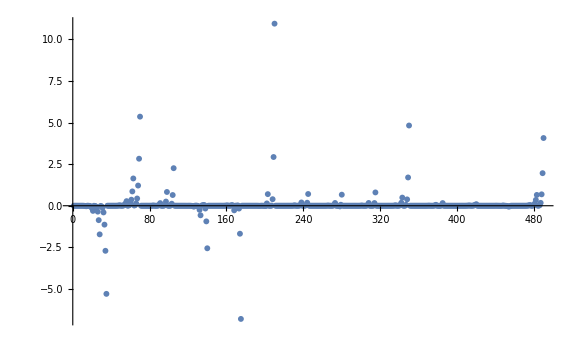
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
orderedEVSYHe3=Sort[Transpose[Eigensystem[{tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2,Transpose[He3Nmhi].He3Norm.He3Nmhi}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0=orderedEVSYHe3[[1,1]];v0=orderedEVSYHe3[[1,2]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]

fullv0=He3Nmh.v0;
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm-Eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{1.1 e0,3}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

N_final = {420}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

J=0.5:  E_0=12.1879

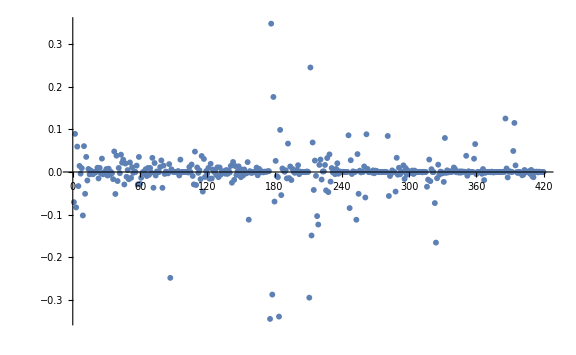
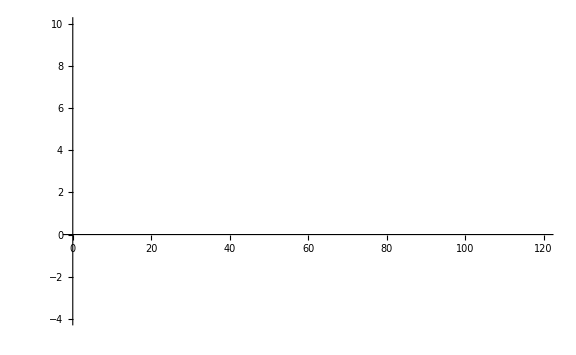
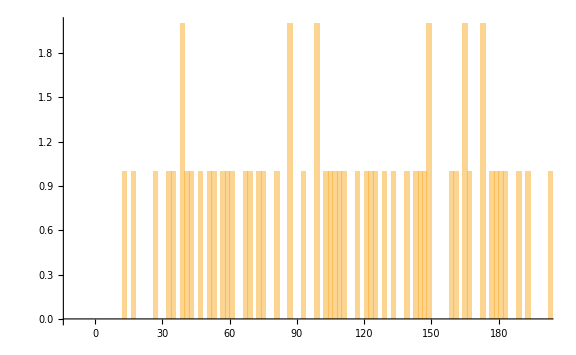
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
orderedEVbareOut=Sort[Transpose[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVbareOut[[1,1]];v0l=orderedEVbareOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,v0l];
AppendTo[LitEigSys,orderedEVbareOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,120},{-4,10}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

```mathematica
SymmetricMatrixQ[evv]
SymmetricMatrixQ[evm]
```

False

False

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in Norm-Eigen-Vector Basis

min/max: {6.6167×10^-13,1478.03}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

Min[Re] = 0.999854

Max[Im] = 7.68264×10^-12

{{1,1}→1.,{1,2}→-2.05684×10^-6,{1,5}→-0.0000453651,{1,6}→8.92912×10^-6,{1,8}→0.0000491219,{1,11}→-0.0000443991,{1,13}→0.0000109821,{1,14}→2.15395×10^-6,{1,15}→-0.000025908,{1,16}→2.94607×10^-6,{1,17}→8.8216×10^-6,{1,18}→-0.0000261021,{1,19}→-0.0000403269,{1,20}→-4.93261×10^-6,{1,24}→-0.0000210244,{1,25}→-0.0000119357,{1,26}→1.73922×10^-6,{1,27}→0.0000207722,{1,30}→-0.0000294447,{1,33}→-7.44811×10^-6,{1,43}→1.69238×10^-6,{1,44}→-1.35967×10^-6,{1,45}→7.1002×10^-6,{1,49}→-1.15257×10^-6,{1,51}→3.89865×10^-6,{1,53}→-1.52212×10^-6,{1,55}→-2.27101×10^-6,{1,60}→2.18484×10^-6,{1,67}→3.75437×10^-6,{1,71}→1.16635×10^-6,{1,73}→-1.78039×10^-6,{1,79}→1.04371×10^-6,{1,81}→1.70733×10^-6,{2,1}→-2.05684×10^-6,{2,2}→1.00032,{2,3}→4.22474×10^-6,{2,4}→-0.000581954,{2,5}→-2.76474×10^-6,{2,6}→1.8022×10^-6,{2,7}→0.000130464,{2,8}→3.74346×10^-6,{2,9}→-0.0000188736,{2,11}→1.60473×10^-6,{2,12}→0.0000421971,{2,14}→0.000026049,{2,15}→1.07883×10^-6,{2,16}→-0.0000450691,{2,20}→-0.0000124881,{2,23}→-6.12299×10^-6,{2,26}→-0.0000311898,{2,31}→-5.50861×10^-6,{2,35}→3.64516×10^-6,{2,36}→0.0000124499,{2,44}→7.99114×10^-6,{2,46}→-3.53142×10^-6,{2,47}→7.96432×10^-6,{2,57}→-1.19359×10^-6,{2,59}→-1.11687×10^-6,{2,62}→-5.22541×10^-6,{2,68}→2.3103×10^-6,{2,84}→1.1802×10^-6,{2,88}→-1.77627×10^-6,{2,108}→-1.03351×10^-6,{2,109}→-1.77203×10^-6,{3,2}→4.22474×10^-6,{3,3}→0.999991,{3,4}→-5.7549×10^-6,{3,5}→0.0000305347,{3,6}→-0.0000105122,{3,8}→-0.0000363234,{3,11}→0.0000200583,{3,12}→1.18701×10^-6,{3,13}→-3.71301×10^-6,{3,14}→-1.00171×10^-6,{3,15}→9.91595×10^-6,{3,17}→-3.45681×10^-6,{3,18}→0.0000130252,{3,19}→0.0000161522,{3,24}→8.98569×10^-6,{3,25}→3.54713×10^-6,{3,27}→-7.83655×10^-6,{3,30}→0.0000129267,{3,33}→2.22631×10^-6,{3,34}→1.43345×10^-6,{3,40}→-1.10583×10^-6,{3,43}→-2.17195×10^-6,{3,45}→-2.31849×10^-6,{4,2}→-0.000581954,{4,3}→-5.7549×10^-6,{4,4}→1.00104,{4,5}→3.78136×10^-6,{4,6}→-3.10138×10^-6,{4,7}→-0.000208706,{4,8}→-4.29432×10^-6,{4,9}→0.0000271696,{4,11}→-3.00185×10^-6,{4,12}→-0.0000612595,{4,13}→1.65216×10^-6,{4,14}→-0.00005034,{4,15}→-1.69406×10^-6,{4,16}→0.0000872166,{4,19}→-1.45935×10^-6,{4,20}→0.000026279,{4,23}→7.47892×10^-6,{4,24}→-1.66098×10^-6,{4,26}→0.0000236406,{4,30}→-1.23074×10^-6,{4,31}→6.07049×10^-6,{4,35}→-5.43636×10^-6,{4,36}→-0.0000209104,{4,44}→-0.0000104388,{4,46}→-3.35439×10^-6,{4,47}→-0.0000122206,{4,57}→4.4903×10^-6,{4,59}→-1.0262×10^-6,{4,62}→0.0000101768,{4,66}→-1.98201×10^-6,{4,68}→-8.41919×10^-6,{4,84}→-3.14364×10^-6,{4,88}→4.43878×10^-6,{4,91}→-1.46087×10^-6,{4,93}→1.48609×10^-6,{4,97}→1.91176×10^-6,{4,108}→3.74572×10^-6,{4,109}→5.7321×10^-6,{4,129}→-1.1929×10^-6,{4,138}→-1.2174×10^-6,{5,1}→-0.0000453651,{5,2}→-2.76474×10^-6,{5,3}→0.0000305349,{5,4}→3.78136×10^-6,{5,5}→0.999987,{5,6}→3.41194×10^-6,{5,8}→0.0000291686,{5,11}→3.36255×10^-6,{5,13}→-4.74221×10^-6,{5,15}→0.0000106257,{5,17}→-1.19772×10^-6,{5,18}→-1.64025×10^-6,{5,19}→2.31504×10^-6,{5,20}→1.09865×10^-6,{5,24}→2.86923×10^-6,{5,25}→1.26453×10^-6,{5,27}→-1.88066×10^-6,{5,33}→1.51087×10^-6,{5,34}→-1.44962×10^-6,{5,37}→2.37796×10^-6,{5,41}→1.39907×10^-6,{5,43}→1.95051×10^-6,{5,51}→-1.05012×10^-6,{5,55}→1.23834×10^-6,{5,60}→-1.18927×10^-6,{6,1}→8.92912×10^-6,{6,2}→1.8022×10^-6,{6,3}→-0.0000105122,{6,4}→-3.10138×10^-6,{6,5}→3.41196×10^-6,{6,6}→0.999997,{6,8}→-7.49992×10^-6,{6,11}→-5.82659×10^-6,{6,13}→2.67632×10^-6,{6,15}→-5.34809×10^-6,{6,17}→1.65944×10^-6,{6,18}→-1.89751×10^-6,{6,19}→-5.5318×10^-6,{6,20}→-1.27428×10^-6,{6,24}→-3.15825×10^-6,{6,25}→-2.11657×10^-6,{6,27}→3.11284×10^-6,{6,30}→-3.28033×10^-6,{6,33}→-1.47849×10^-6,{6,37}→-1.19587×10^-6,{6,45}→1.12455×10^-6,{7,2}→0.000130464,{7,4}→-0.000208706,{7,7}→1.00004,{7,9}→-7.39429×10^-6,{7,12}→-0.000017244,{7,14}→-7.62601×10^-6,{7,20}→-4.83661×10^-6,{7,23}→-3.53772×10^-6,{7,26}→4.95042×10^-6,{7,31}→-1.75293×10^-6,{7,36}→-1.38632×10^-6,{7,44}→1.54737×10^-6,{7,47}→5.2358×10^-6,{7,57}→-4.06457×10^-6,{7,66}→1.18533×10^-6,{7,68}→2.41362×10^-6,{7,91}→1.13053×10^-6,{7,108}→-1.14106×10^-6,{7,109}→-1.31742×10^-6,{8,1}→0.000049122,{8,2}→3.74346×10^-6,{8,3}→-0.0000363234,{8,4}→-4.29432×10^-6,{8,5}→0.0000291687,{8,6}→-7.49992×10^-6,{8,8}→0.999952,{8,11}→7.48478×10^-6,{8,12}→1.05878×10^-6,{8,13}→2.66765×10^-6,{8,15}→-4.93389×10^-6,{8,18}→9.01357×10^-6,{8,19}→8.454×10^-6,{8,24}→2.19466×10^-6,{8,25}→1.98895×10^-6,{8,27}→-3.65238×10^-6,{8,30}→8.3207×10^-6,{8,34}→1.66167×10^-6,{8,37}→-2.48688×10^-6,{8,40}→-1.02627×10^-6,{8,41}→-1.37571×10^-6,{8,43}→-2.51381×10^-6,{8,45}→-1.43862×10^-6,{8,58}→1.09206×10^-6,{9,2}→-0.0000188736,{9,4}→0.0000271696,{9,7}→-7.39429×10^-6,{9,9}→0.999981,{9,12}→-0.0000213904,{9,14}→-0.000029199,{9,16}→0.0000166782,{9,23}→-2.03261×10^-6,{9,36}→-3.31836×10^-6,{9,46}→-3.33004×10^-6,{9,47}→3.319×10^-6,{9,57}→-1.50126×10^-6,{9,62}→1.03301×10^-6,{9,68}→-1.07827×10^-6,{9,82}→-1.24317×10^-6,{9,88}→1.06359×10^-6,{10,10}→1.,{11,1}→-0.0000443991,{11,2}→1.60473×10^-6,{11,3}→0.0000200584,{11,4}→-3.00185×10^-6,{11,5}→3.36245×10^-6,{11,6}→-5.8266×10^-6,{11,8}→7.48476×10^-6,{11,11}→1.00001,{11,13}→-4.74852×10^-6,{11,15}→0.0000108914,{11,18}→1.72072×10^-6,{11,19}→2.59032×10^-6,{11,24}→3.77597×10^-6,{11,27}→-1.52727×10^-6,{11,29}→1.06006×10^-6,{11,30}→1.34994×10^-6,{12,2}→0.0000421971,{12,3}→1.18701×10^-6,{12,4}→-0.0000612595,{12,7}→-0.000017244,{12,8}→1.05878×10^-6,{12,9}→-0.0000213904,{12,12}→1.00001,{12,14}→5.41818×10^-6,{12,16}→-0.000012068,{12,20}→-1.05698×10^-6,{12,23}→2.70482×10^-6,{12,26}→3.81555×10^-6,{12,31}→3.59885×10^-6,{12,35}→1.7354×10^-6,{12,36}→4.24633×10^-6,{12,44}→1.60524×10^-6,{12,57}→1.25063×10^-6,{12,62}→-1.85358×10^-6,{12,66}→-1.12216×10^-6,{12,93}→-1.09729×10^-6,{13,1}→0.0000109821,{13,3}→-3.71308×10^-6,{13,4}→1.65216×10^-6,{13,5}→-4.74223×10^-6,{13,6}→2.67633×10^-6,{13,8}→2.66763×10^-6,{13,11}→-4.74849×10^-6,{13,13}→1.,{13,15}→-3.95804×10^-6,{13,17}→1.16068×10^-6,{13,18}→-2.47183×10^-6,{13,19}→-3.13423×10^-6,{13,24}→-2.3442×10^-6,{13,27}→1.50596×10^-6,{13,30}→-2.28552×10^-6,{14,1}→2.15395×10^-6,{14,2}→0.000026049,{14,3}→-1.00171×10^-6,{14,4}→-0.00005034,{14,7}→-7.62601×10^-6,{14,9}→-0.000029199,{14,12}→5.41818×10^-6,{14,14}→0.999988,{14,20}→2.76018×10^-6,{14,23}→-1.00311×10^-6,{14,26}→-1.78737×10^-6,{14,35}→-3.17986×10^-6,{14,46}→-1.52396×10^-6,{14,47}→1.69903×10^-6,{14,68}→-1.39194×10^-6,{15,1}→-0.000025908,{15,2}→1.07883×10^-6,{15,3}→9.91594×10^-6,{15,4}→-1.69406×10^-6,{15,5}→0.0000106257,{15,6}→-5.34809×10^-6,{15,8}→-4.93388×10^-6,{15,11}→0.0000108914,{15,13}→-3.95804×10^-6,{15,15}→1.00001,{15,17}→-2.03583×10^-6,{15,18}→5.5287×10^-6,{15,19}→8.55805×10^-6,{15,24}→5.61131×10^-6,{15,25}→2.01206×10^-6,{15,27}→-4.52359×10^-6,{15,30}→5.69393×10^-6,{15,33}→1.78518×10^-6,{15,45}→-1.3545×10^-6,{16,1}→2.94607×10^-6,{16,2}→-0.0000450691,{16,4}→0.0000872166,{16,9}→0.0000166782,{16,12}→-0.000012068,{16,16}→1.00001,{16,20}→1.05352×10^-6,{16,36}→-1.33614×10^-6,{16,46}→-1.71738×10^-6,{16,62}→1.12359×10^-6,{17,1}→8.82159×10^-6,{17,3}→-3.45678×10^-6,{17,5}→-1.19771×10^-6,{17,6}→1.65944×10^-6,{17,13}→1.16067×10^-6,{17,15}→-2.03582×10^-6,{17,17}→1.,{18,1}→-0.0000261021,{18,3}→0.0000130252,{18,5}→-1.64024×10^-6,{18,6}→-1.89751×10^-6,{18,8}→9.01357×10^-6,{18,11}→1.7207×10^-6,{18,13}→-2.47185×10^-6,{18,15}→5.5287×10^-6,{18,18}→1.,{18,24}→1.25421×10^-6,{19,1}→-0.0000403269,{19,3}→0.0000161522,{19,4}→-1.45935×10^-6,{19,5}→2.31504×10^-6,{19,6}→-5.5318×10^-6,{19,8}→8.454×10^-6,{19,11}→2.59031×10^-6,{19,13}→-3.13424×10^-6,{19,15}→8.55805×10^-6,{19,19}→1.,{19,24}→2.00889×10^-6,{20,1}→-4.93261×10^-6,{20,2}→-0.0000124881,{20,4}→0.000026279,{20,5}→1.09865×10^-6,{20,6}→-1.27428×10^-6,{20,7}→-4.83661×10^-6,{20,12}→-1.05698×10^-6,{20,14}→2.76018×10^-6,{20,16}→1.05352×10^-6,{20,20}→1.,{20,35}→1.28256×10^-6,{21,21}→1.,{22,22}→1.,{23,2}→-6.12299×10^-6,{23,4}→7.47892×10^-6,{23,7}→-3.53772×10^-6,{23,9}→-2.03261×10^-6,{23,12}→2.70482×10^-6,{23,14}→-1.00311×10^-6,{23,23}→1.,{23,26}→-1.48792×10^-6,{24,1}→-0.0000210244,{24,3}→8.98565×10^-6,{24,4}→-1.66098×10^-6,{24,5}→2.86923×10^-6,{24,6}→-3.15825×10^-6,{24,8}→2.19465×10^-6,{24,11}→3.776×10^-6,{24,13}→-2.34416×10^-6,{24,15}→5.61131×10^-6,{24,18}→1.25421×10^-6,{24,19}→2.00891×10^-6,{24,24}→1.,{24,27}→-1.15047×10^-6,{24,30}→1.07353×10^-6,{25,1}→-0.0000119357,{25,3}→3.54719×10^-6,{25,5}→1.2645×10^-6,{25,6}→-2.11659×10^-6,{25,8}→1.989×10^-6,{25,15}→2.01207×10^-6,{25,25}→1.,{26,1}→1.73922×10^-6,{26,2}→-0.0000311898,{26,4}→0.0000236406,{26,7}→4.95042×10^-6,{26,12}→3.81555×10^-6,{26,14}→-1.78737×10^-6,{26,23}→-1.48792×10^-6,{26,26}→0.999997,{26,35}→-1.02717×10^-6,{27,1}→0.0000207722,{27,3}→-7.83655×10^-6,{27,5}→-1.88069×10^-6,{27,6}→3.11283×10^-6,{27,8}→-3.65238×10^-6,{27,11}→-1.52727×10^-6,{27,13}→1.50597×10^-6,{27,15}→-4.52359×10^-6,{27,24}→-1.15047×10^-6,{27,27}→1.,{28,28}→1.,{29,11}→1.06006×10^-6,{29,29}→1.,{30,1}→-0.0000294447,{30,3}→0.0000129267,{30,4}→-1.23074×10^-6,{30,6}→-3.28033×10^-6,{30,8}→8.32069×10^-6,{30,11}→1.34994×10^-6,{30,13}→-2.28552×10^-6,{30,15}→5.69393×10^-6,{30,24}→1.07353×10^-6,{30,30}→0.999999,{31,2}→-5.50861×10^-6,{31,4}→6.07049×10^-6,{31,7}→-1.75293×10^-6,{31,12}→3.59885×10^-6,{31,31}→1.,{32,32}→1.,{33,1}→-7.44811×10^-6,{33,3}→2.22629×10^-6,{33,5}→1.51086×10^-6,{33,6}→-1.47849×10^-6,{33,15}→1.78518×10^-6,{33,33}→1.,{34,3}→1.43347×10^-6,{34,5}→-1.44964×10^-6,{34,8}→1.66167×10^-6,{34,34}→1.,{35,2}→3.64516×10^-6,{35,4}→-5.43636×10^-6,{35,12}→1.7354×10^-6,{35,14}→-3.17986×10^-6,{35,20}→1.28255×10^-6,{35,26}→-1.02717×10^-6,{35,35}→0.999999,{36,2}→0.0000124499,{36,4}→-0.0000209104,{36,7}→-1.38632×10^-6,{36,9}→-3.31836×10^-6,{36,12}→4.24633×10^-6,{36,16}→-1.33614×10^-6,{36,36}→1.,{37,5}→2.37795×10^-6,{37,6}→-1.19587×10^-6,{37,8}→-2.48689×10^-6,{37,37}→1.,{38,38}→1.,{39,39}→1.,{40,3}→-1.10581×10^-6,{40,8}→-1.02627×10^-6,{40,40}→1.,{41,5}→1.39907×10^-6,{41,8}→-1.37571×10^-6,{41,41}→1.,{42,42}→1.,{43,1}→1.69238×10^-6,{43,3}→-2.17195×10^-6,{43,5}→1.95052×10^-6,{43,8}→-2.51381×10^-6,{43,43}→1.,{44,1}→-1.35967×10^-6,{44,2}→7.99114×10^-6,{44,4}→-0.0000104388,{44,7}→1.54737×10^-6,{44,12}→1.60524×10^-6,{44,44}→1.,{45,1}→7.10021×10^-6,{45,3}→-2.3185×10^-6,{45,6}→1.12455×10^-6,{45,8}→-1.43862×10^-6,{45,15}→-1.3545×10^-6,{45,45}→1.,{46,2}→-3.53142×10^-6,{46,4}→-3.35439×10^-6,{46,9}→-3.33004×10^-6,{46,14}→-1.52396×10^-6,{46,16}→-1.71739×10^-6,{46,46}→1.,{47,2}→7.96432×10^-6,{47,4}→-0.0000122206,{47,7}→5.2358×10^-6,{47,9}→3.319×10^-6,{47,14}→1.69903×10^-6,{47,47}→1.,{48,48}→1.,{49,1}→-1.15257×10^-6,{49,49}→1.,{50,50}→1.,{51,1}→3.89865×10^-6,{51,5}→-1.05013×10^-6,{51,51}→1.,{52,52}→1.,{53,1}→-1.52212×10^-6,{53,53}→1.,{54,54}→1.,{55,1}→-2.27101×10^-6,{55,5}→1.23835×10^-6,{55,55}→1.,{56,56}→1.,{57,2}→-1.19359×10^-6,{57,4}→4.4903×10^-6,{57,7}→-4.06457×10^-6,{57,9}→-1.50126×10^-6,{57,12}→1.25063×10^-6,{57,57}→1.,{58,8}→1.09207×10^-6,{58,58}→1.,{59,2}→-1.11687×10^-6,{59,4}→-1.02619×10^-6,{59,59}→1.,{60,1}→2.18484×10^-6,{60,5}→-1.18925×10^-6,{60,60}→1.,{61,61}→1.,{62,2}→-5.22541×10^-6,{62,4}→0.0000101768,{62,9}→1.03301×10^-6,{62,12}→-1.85358×10^-6,{62,16}→1.12359×10^-6,{62,62}→1.,{63,63}→1.,{64,64}→1.,{65,65}→1.,{66,4}→-1.98201×10^-6,{66,7}→1.18533×10^-6,{66,12}→-1.12216×10^-6,{66,66}→1.,{67,1}→3.75437×10^-6,{67,67}→1.,{68,2}→2.3103×10^-6,{68,4}→-8.41919×10^-6,{68,7}→2.41362×10^-6,{68,9}→-1.07827×10^-6,{68,14}→-1.39194×10^-6,{68,68}→1.,{69,69}→1.,{70,70}→1.,{71,1}→1.16635×10^-6,{71,71}→1.,{72,72}→1.,{73,1}→-1.7804×10^-6,{73,73}→1.,{74,74}→1.,{75,75}→1.,{76,76}→1.,{77,77}→1.,{78,78}→1.,{79,1}→1.04371×10^-6,{79,79}→1.,{80,80}→1.,{81,1}→1.70733×10^-6,{81,81}→1.,{82,9}→-1.24317×10^-6,{82,82}→1.,{83,83}→1.,{84,2}→1.1802×10^-6,{84,4}→-3.14364×10^-6,{84,84}→1.,{85,85}→1.,{86,86}→1.,{87,87}→1.,{88,2}→-1.77627×10^-6,{88,4}→4.43878×10^-6,{88,9}→1.06359×10^-6,{88,88}→1.,{89,89}→1.,{90,90}→1.,{91,4}→-1.46087×10^-6,{91,7}→1.13053×10^-6,{91,91}→1.,{92,92}→1.,{93,4}→1.48609×10^-6,{93,12}→-1.09729×10^-6,{93,93}→1.,{94,94}→1.,{95,95}→1.,{96,96}→1.,{97,4}→1.91176×10^-6,{97,97}→1.,{98,98}→1.,{99,99}→1.,{100,100}→1.,{101,101}→1.,{102,102}→1.,{103,103}→1.,{104,104}→1.,{105,105}→1.,{106,106}→1.,{107,107}→1.,{108,2}→-1.03351×10^-6,{108,4}→3.74572×10^-6,{108,7}→-1.14106×10^-6,{108,108}→1.,{109,2}→-1.77203×10^-6,{109,4}→5.7321×10^-6,{109,7}→-1.31742×10^-6,{109,109}→1.,{110,110}→1.,{111,111}→1.,{112,112}→1.,{113,113}→1.,{114,114}→1.,{115,115}→1.,{116,116}→1.,{117,117}→1.,{118,118}→1.,{119,119}→1.,{120,120}→1.,{121,121}→1.,{122,122}→1.,{123,123}→1.,{124,124}→1.,{125,125}→1.,{126,126}→1.,{127,127}→1.,{128,128}→1.,{129,4}→-1.1929×10^-6,{129,129}→1.,{130,130}→1.,{131,131}→1.,{132,132}→1.,{133,133}→1.,{134,134}→1.,{135,135}→1.,{136,136}→1.,{137,137}→1.,{138,4}→-1.2174×10^-6,{138,138}→1.,{139,139}→1.,{140,140}→1.,{141,141}→1.,{142,142}→1.,{143,143}→1.,{144,144}→1.,{145,145}→1.,{146,146}→1.,{147,147}→1.,{148,148}→1.,{149,149}→1.,{150,150}→1.,{151,151}→1.,{152,152}→1.,{153,153}→1.,{154,154}→1.,{155,155}→1.,{156,156}→1.,{157,157}→1.,{158,158}→1.,{159,159}→1.,{160,160}→1.,{161,161}→1.,{162,162}→1.,{163,163}→1.,{164,164}→1.,{165,165}→1.,{166,166}→1.,{167,167}→1.,{168,168}→1.,{169,169}→1.,{170,170}→1.,{171,171}→1.,{172,172}→1.,{173,173}→1.,{174,174}→1.,{175,175}→1.,{176,176}→1.,{177,177}→1.,{178,178}→1.,{179,179}→1.,{180,180}→1.,{181,181}→1.,{182,182}→1.,{183,183}→1.,{184,184}→1.,{185,185}→1.,{186,186}→1.,{187,187}→1.,{188,188}→1.,{189,189}→1.,{190,190}→1.,{191,191}→1.,{192,192}→1.,{193,193}→1.,{194,194}→1.,{195,195}→1.,{196,196}→1.,{197,197}→1.,{198,198}→1.,{199,199}→1.,{200,200}→1.,{201,201}→1.,{202,202}→1.,{203,203}→1.,{204,204}→1.,{205,205}→1.,{206,206}→1.,{207,207}→1.,{208,208}→1.,{209,209}→1.,{210,210}→1.,{211,211}→1.,{212,212}→1.,{213,213}→1.,{214,214}→1.,{215,215}→1.,{216,216}→1.,{217,217}→1.,{218,218}→1.,{219,219}→1.,{220,220}→1.,{221,221}→1.,{222,222}→1.,{223,223}→1.,{224,224}→1.,{225,225}→1.,{226,226}→1.,{227,227}→1.,{228,228}→1.,{229,229}→1.,{230,230}→1.,{231,231}→1.,{232,232}→1.,{233,233}→1.,{234,234}→1.,{235,235}→1.,{236,236}→1.,{237,237}→1.,{238,238}→1.,{239,239}→1.,{240,240}→1.,{241,241}→1.,{242,242}→1.,{243,243}→1.,{244,244}→1.,{245,245}→1.,{246,246}→1.,{247,247}→1.,{248,248}→1.,{249,249}→1.,{250,250}→1.,{251,251}→1.,{252,252}→1.,{253,253}→1.,{254,254}→1.,{255,255}→1.,{256,256}→1.,{257,257}→1.,{258,258}→1.,{259,259}→1.,{260,260}→1.,{261,261}→1.,{262,262}→1.,{263,263}→1.,{264,264}→1.,{265,265}→1.,{266,266}→1.,{267,267}→1.,{268,268}→1.,{269,269}→1.,{270,270}→1.,{271,271}→1.,{272,272}→1.,{273,273}→1.,{274,274}→1.,{275,275}→1.,{276,276}→1.,{277,277}→1.,{278,278}→1.,{279,279}→1.,{280,280}→1.,{281,281}→1.,{282,282}→1.,{283,283}→1.,{284,284}→1.,{285,285}→1.,{286,286}→1.,{287,287}→1.,{288,288}→1.,{289,289}→1.,{290,290}→1.,{291,291}→1.,{292,292}→1.,{293,293}→1.,{294,294}→1.,{295,295}→1.,{296,296}→1.,{297,297}→1.,{298,298}→1.,{299,299}→1.,{300,300}→1.,{301,301}→1.,{302,302}→1.,{303,303}→1.,{304,304}→1.,{305,305}→1.,{306,306}→1.,{307,307}→1.,{308,308}→1.,{309,309}→1.,{310,310}→1.,{311,311}→1.,{312,312}→1.,{313,313}→1.,{314,314}→1.,{315,315}→1.,{316,316}→1.,{317,317}→1.,{318,318}→1.,{319,319}→1.,{320,320}→1.,{321,321}→1.,{322,322}→1.,{323,323}→1.,{324,324}→1.,{325,325}→1.,{326,326}→1.,{327,327}→1.,{328,328}→1.,{329,329}→1.,{330,330}→1.,{331,331}→1.,{332,332}→1.,{333,333}→1.,{334,334}→1.,{335,335}→1.,{336,336}→1.,{337,337}→1.,{338,338}→1.,{339,339}→1.,{340,340}→1.,{341,341}→1.,{342,342}→1.,{343,343}→1.,{344,344}→1.,{345,345}→1.,{346,346}→1.,{347,347}→1.,{348,348}→1.,{349,349}→1.,{350,350}→1.,{351,351}→1.,{352,352}→1.,{353,353}→1.,{354,354}→1.,{355,355}→1.,{356,356}→1.,{357,357}→1.,{358,358}→1.,{359,359}→1.,{360,360}→1.,{361,361}→1.,{362,362}→1.,{363,363}→1.,{364,364}→1.,{365,365}→1.,{366,366}→1.,{367,367}→1.,{368,368}→1.,{369,369}→1.,{370,370}→1.,{371,371}→1.,{372,372}→1.,{373,373}→1.,{374,374}→1.,{375,375}→1.,{376,376}→1.,{377,377}→1.,{378,378}→1.,{379,379}→1.,{380,380}→1.,{381,381}→1.,{382,382}→1.,{383,383}→1.,{384,384}→1.,{385,385}→1.,{386,386}→1.,{387,387}→1.,{388,388}→1.,{389,389}→1.,{390,390}→1.,{391,391}→1.,{392,392}→1.,{393,393}→1.,{394,394}→1.,{395,395}→1.,{396,396}→1.,{397,397}→1.,{398,398}→1.,{399,399}→1.,{400,400}→1.,{401,401}→1.,{402,402}→1.,{403,403}→1.,{404,404}→1.,{405,405}→1.,{406,406}→1.,{407,407}→1.,{408,408}→1.,{409,409}→1.,{410,410}→1.,{411,411}→1.,{412,412}→1.,{413,413}→1.,{414,414}→1.,{415,415}→1.,{416,416}→1.,{417,417}→1.,{418,418}→1.,{419,419}→1.,{420,420}→1.,{_,_}→0}

J=0.5:  E_0=12.1879

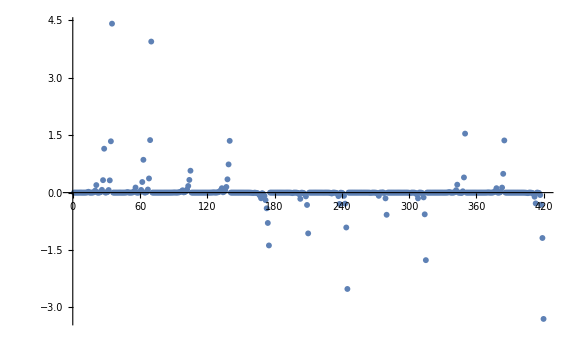
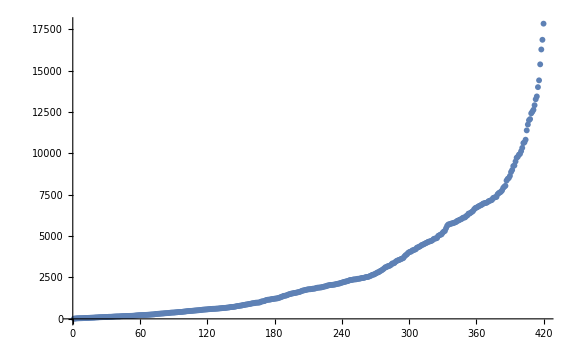
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYOut=Sort[Transpose[Eigensystem[{tst=(Transpose[LitNmhi].LitHam[[nj]]).LitNmhi;tst=(tst+Transpose[tst])/2,Transpose[LitNmhi].LitNorm[[nj]].LitNmhi}]],Re[#1[[1]]]<Re[#2[[1]]]&];

e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,LitNmh.v0l];
AppendTo[LitEigSys,orderedEVSYOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,Automatic},{-4,Automatic}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

tmp =BinaryReadList["InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|helion⟩) = {1,420,490}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,420,420}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,420,420}

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};

{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};

Do[
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];

OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB]];
AppendTo[inhomoEB,Transpose[OμLHSEB].((tmp.OμRHSEB).evgsEB)];

{λfinal,trfLit}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
AppendTo[inhomo,tmp.evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

# of 2-1 states ≥ 0

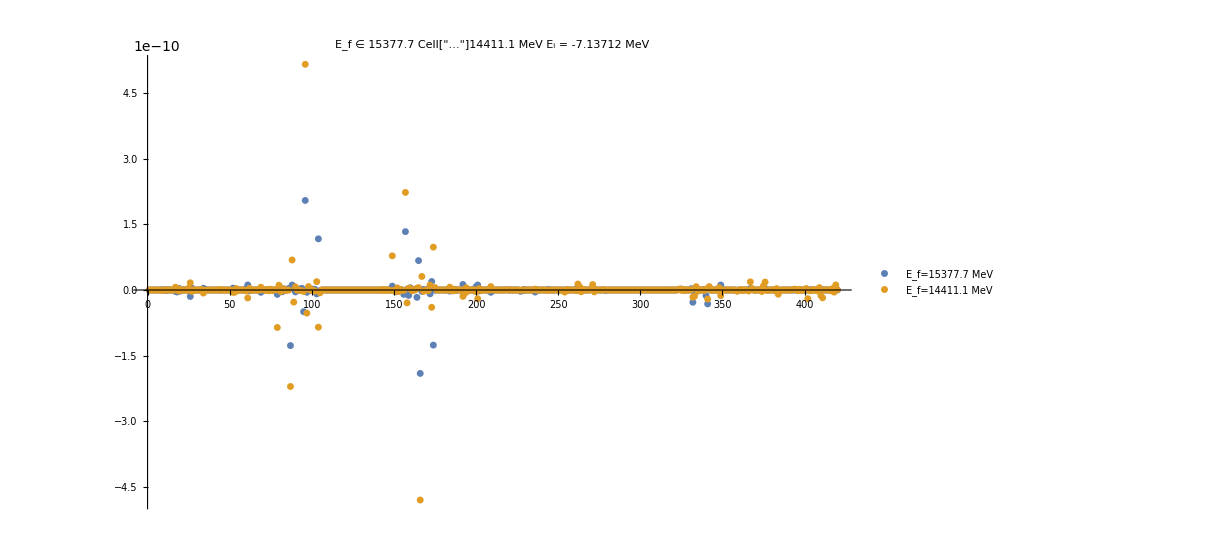
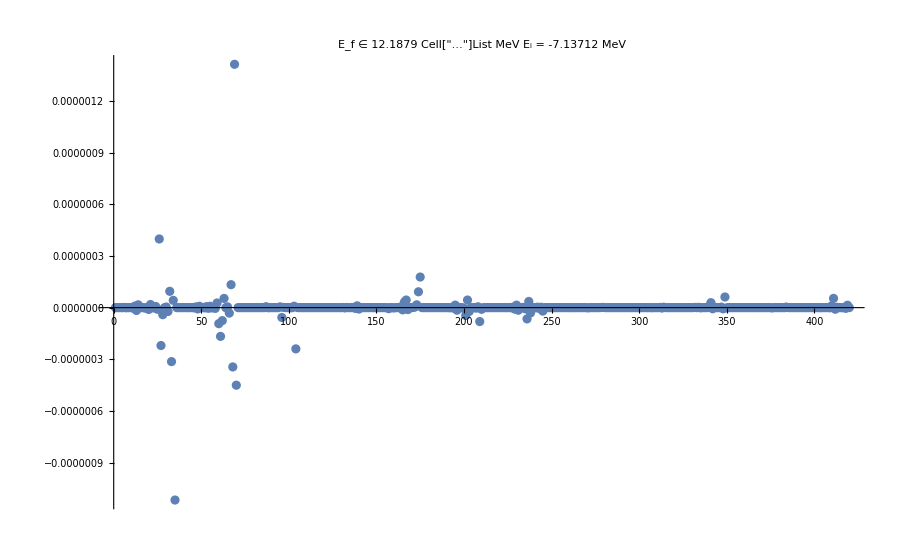
-Graphics- | -Graphics-

-Graphics-2.74674×10^-30  ,  E_f=15377.7 MeV

-Graphics-1.54201×10^-29  ,  E_f=14411.1 MeV

```mathematica
OneTwoConti=Flatten[Position[λfinal,n_/;n<0]];
OrderedSpectF=Join[Delete[λfinal,{#}&/@OneTwoConti],Reverse[λfinal[[OneTwoConti]]]];
OrderedEvecsF=Join[Delete[trfLit,{#}&/@OneTwoConti],Reverse[trfLit[[OneTwoConti]]]];

Print["# of 2-1 states ≥ ",Length[OneTwoConti]]

contin=4;
evrng111={contin,contin+1};(*IntegerPart[Subdivide[1,Length[λfinal]-Length[OneTwoConti],20]];*)
evrng21=IntegerPart[Subdivide[1,Length[OneTwoConti],1]];
inhomo111=(inhomo[[1]]  OrderedEvecsF[[#]])&/@evrng111;
inhomo21=(inhomo[[1]]  OrderedEvecsF[[-#]])&/@evrng21;

Grid[{{
ListPlot[inhomo111,AxesLabel->{MaTeX["\\text{RGM basis vector}~m",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f ∈ "<>ToString[OrderedSpectF[[evrng111[[1]]]]]<>" Cell["…",ExpressionUUID->"eb896d0b-fc31-48e9-ad56-82f8690216ee"]"<>ToString[OrderedSpectF[[evrng111[[-1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV",PlotLegends->{"E_f="<>ToString[OrderedSpectF[[evrng111[[1]]]]]<>" MeV","E_f="<>ToString[OrderedSpectF[[evrng111[[-1]]]]]<>" MeV"}],
ListPlot[inhomo21,AxesLabel->{MaTeX["\\text{RGM basis vector}~m",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f ∈ "<>ToString[OrderedSpectF[[-evrng21[[1]]]]]<>" Cell["…",ExpressionUUID->"5a3996a2-0b62-4225-8ab0-4fa885bb50d3"]"<>ToString[OrderedSpectF[[-evrng21[[-1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV"]
}}
]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo111)^2)[[1]],"  ,  E_f=",OrderedSpectF[[evrng111[[1]]]]," MeV"]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo111)^2)[[-1]],"  ,  E_f=",OrderedSpectF[[evrng111[[-1]]]]," MeV"]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0^initial = -7.13712    dim(initial) = {490}

E_0^final  = 12.1879    dim(final)   = {420}

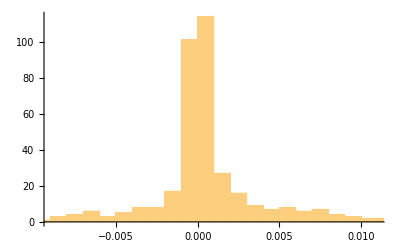

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[{(Transpose[OμRHSEV].He3Ham).OμRHSEV,(Transpose[OμRHSEV].He3Norm).OμRHSEV}];
EvecGSiEV=Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];

Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[{(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV,(Transpose[OμLHSEV].(LitNorm[[nj]])).OμLHSEV}];
EvecGSfEV=Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=(Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].OμRHSEV)).EvecGSiEV;
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsisEV,Re[Transpose[{EvalsFEV,tmplEV}]]];
AppendTo[CumStrengthsEV,Re[Transpose[{Sort[lpsisEV[[nj]]][[All,1]],Accumulate[Sort[lpsisEV[[nj]]][[All,2]]]}]]];

,{nj,Range[1,Length[Subscript[I, n]]]}
]
Histogram[Sort[EvecsFEV[[3]]]]
```

E_0^initial = -7.13712    dim(initial) = {490}

E_0^final  = 12.1879    dim(final)   = {420}

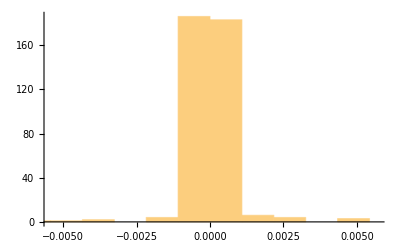

```mathematica
lpsisRGM={};CumStrengthsRGM={};

{EvalsIRGM,EvecsIRGM}=Re[Eigensystem[{He3Ham,He3Norm}]];
EvecGSiRGM=Flatten[EvecsIRGM[[TakeSmallest[EvalsIRGM->"Index",1]]]];
EvalGSiRGM=Min[EvalsIRGM];

Do[

{EvalsFRGM,EvecsFRGM}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
EvecGSfRGM=Flatten[EvecsFRGM[[TakeSmallest[EvalsFRGM->"Index",1]]]];
EvalGSfRGM=Min[EvalsFRGM];

Print["E_0^initial = ",EvalGSiRGM,"    dim(initial) = ",Dimensions[EvalsIRGM]];
Print["E_0^final  = ",EvalGSfRGM,"    dim(final)   = ",Dimensions[EvalsFRGM]];
tmplRGM=0;

Do[
(*inhomoRGM=(Transpose[LitNorm[[nj]]].(CouplingBlockj[[nj]][[mm]][[2]].He3Norm)).EvecGSiRGM;*)
inhomoRGM=CouplingBlockj[[nj]][[mm]][[2]].EvecGSiRGM;
tmplRGM=tmplRGM+(EvecsFRGM.inhomoRGM)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsisRGM,Re[Transpose[{EvalsFRGM,tmplRGM}]]];
AppendTo[CumStrengthsRGM,Re[Transpose[{Sort[lpsisRGM[[nj]]][[All,1]],Accumulate[Sort[lpsisRGM[[nj]]][[All,2]]]}]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]
Histogram[Sort[EvecsFRGM[[1]]]]
```

{490}

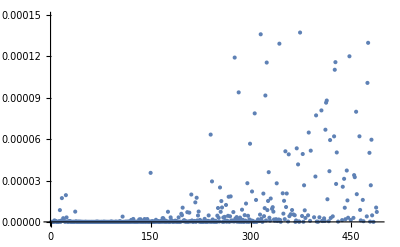

```mathematica
Dimensions[EvecGSiEV]
ListPlot[EvecGSiEV^2]
```

{490}

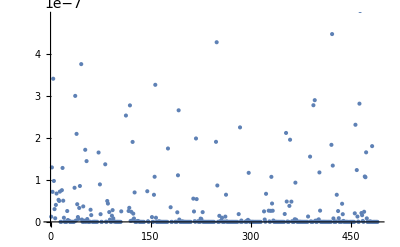

```mathematica
Dimensions[EvecGSiRGM]
ListPlot[EvecGSiRGM^2]
```

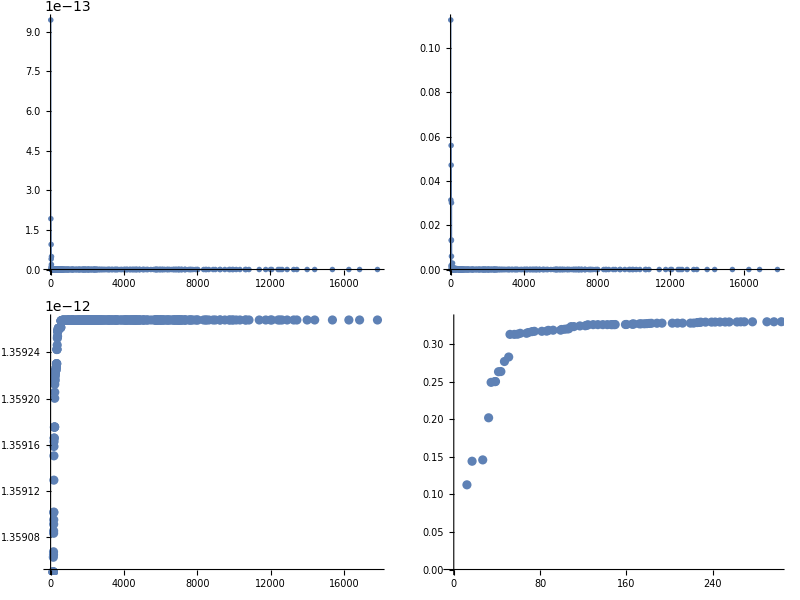

Defficient LHS ME's: {176086}

Defficient RHS ME's: {240100}

```mathematica
plote3=Grid[{{
ListPlot[Reverse[lpsisRGM[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize],
ListPlot[Reverse[lpsisEV[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
},{
ListPlot[CumStrengthsRGM,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,Automatic},Automatic},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{RGM order}",Magnification->2]],
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,300},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
}}]
Print["Defficient LHS ME's: ",Dimensions[Select[Flatten[Chop[OμLHSEV.Transpose[OμLHSEV]]],#≠0.&&#≠1.&]]];
Print["Defficient RHS ME's: ",Dimensions[Select[Flatten[Chop[OμRHSEV.Transpose[OμRHSEV]]],#≠0.&&#≠1.&]]];
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengthsEV,LocalObject["CumHelionStrengths_"<>StringTake[resultsDir,{-11,-9}]]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths_v23]

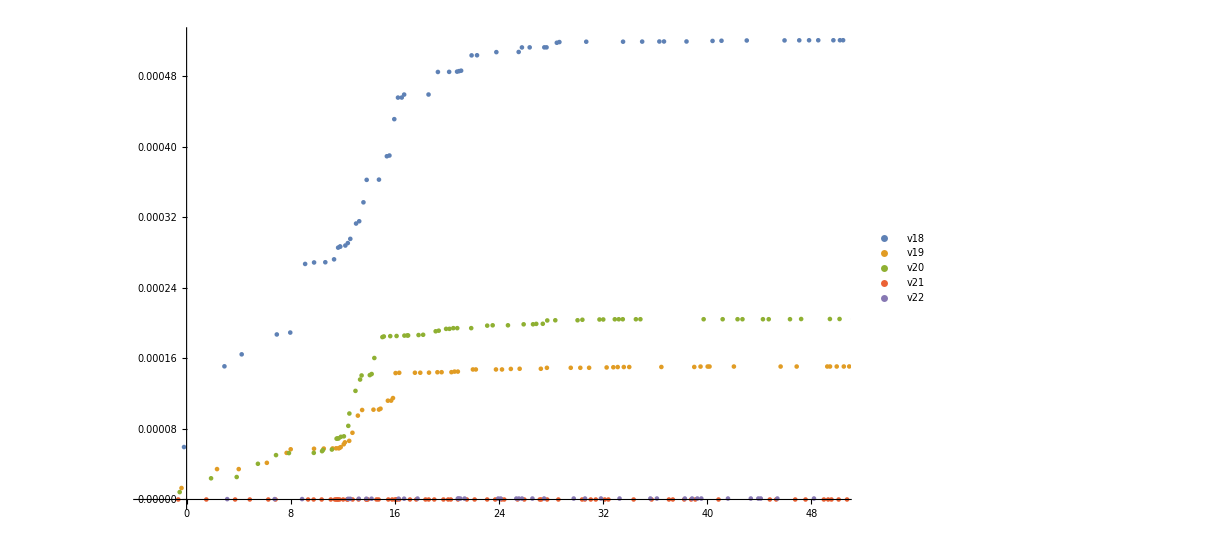

```mathematica
suffies={"v18","v19","v20","v21","v22"};
CumStrengthS={};
Do[
AppendTo[CumStrengthS,Flatten[Get[LocalObject["CumHelionStrengths_"<>suff]],1]];
,{suff,suffies}
]

ListPlot[CumStrengthS,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,50},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotLegends->suffies]
```